# Custom Curve Generator

## Image definition

Change your image link in the line below, and re-evaluate the whole notebook.

```mathematica
image=Import["http://www.mearso.co.uk/logospotter/images/37.jpg"]
```

-Graphics-

## Function Definition

```mathematica
pointListToLines[pointList_, neighborhoodSize_:6]:= 
Module[{L = DeleteDuplicates[pointList], NF, λ,lineBag, counter, seenQ, sLB, nearest,  
            nearest1, nextPoint,couldReverseQ,  𝒹, 𝓃, 𝓈},
NF = Nearest[L] ;
     λ = Length[L];
Monitor[
(* list of segments *)
lineBag = {};
counter = 0; 
While[counter < λ,
(* new segment *)
sLB = {RandomChoice[DeleteCases[L, _?seenQ]]}; 
seenQ[sLB[[1]]]=True;
counter++;
couldReverseQ= True;
(* complete segment *)
While[(nearest = NF[Last[sLB], {Infinity, neighborhoodSize}];
           nearest1 = SortBy[DeleteCases[nearest, _?seenQ], 1.EuclideanDistance[Last[sLB],#]&];
           nearest1 =!= {} || couldReverseQ),
             If[nearest1 === {},
             (* extend the other end; penalize sharp edges *)
             sLB = Reverse[sLB]; couldReverseQ = False,
            (* prefer straight continuation *)
             nextPoint = If[Length[sLB] ≤ 3, nearest1[[1]],
                                         𝒹 = 1.Normalize[(sLB[[-1]]-sLB[[-2]]) + 1/2 (sLB[[-2]]-sLB[[-3]])];
                                         𝓃 = {-1, 1}Reverse[𝒹];
                                        𝓈 = Sort[{Sqrt[(𝒹.(# - sLB[[-1]]))^2 + 
                                                           (* perpendicular *) 2 (𝓃.(# - sLB[[-1]]))^2], # }& /@ nearest1]; 
                                        𝓈[[1,2]]];
             AppendTo[sLB, nextPoint];
            seenQ[nextPoint]=True;
           counter++ ]];
AppendTo[lineBag, sLB]];
(* return segments sorted by length *)
Reverse[SortBy[Select[lineBag , Length[#] > 12&], Length]],
(* monitor progress *)
Grid[{{Text[Style["progress point joining", Darker[Green, 0.66]]], ProgressIndicator[counter/λ]},
          {Text[Style["number of segments", Darker[Green, 0.66]]],  Length[lineBag] + 1}}, 
        Alignment -> Left, Dividers -> Center]]]
```

```mathematica
edgeImage=Thinning[EdgeDetect[ColorConvert[
ImagePad[Image[Map[Most, ImageData[image],{2}]],20, White], "Grayscale"]]]
```

-Graphics-

```mathematica
edgePoints = {#2, -#1}&@@@ Position[ImageData[edgeImage],1,{2}];
```

```mathematica
SeedRandom[2];
hLines = pointListToLines[edgePoints,16];
Length[hLines]
```

12

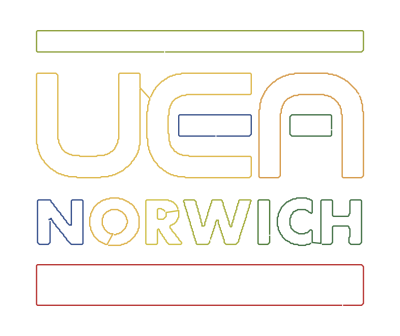

```mathematica
Graphics[{ColorData["DarkRainbow"][RandomReal[]],Line[#]}&  /@ hLines]
```

```mathematica
Options[fourierComponents] = {"MaxOrder" -> 180, "OpenClose" -> 0.025};

fourierComponents[pointLists_,OptionsPattern[]] := 
Monitor[Table[fourierComponentData[pointLists[[k]],                           
                                                                      If[Head[#]===List, #[[k]], #]&[ OptionValue["MaxOrder"]],
                                                                      If[Head[#]===List, #[[k]], #]&[ OptionValue["OpenClose"]]],
                         {k, Length[pointLists]}],
Grid[{{Text[Style["progress calculating Fourier coefficients", Darker[Green, 0.66]]], ProgressIndicator[k/Length[pointLists]]} }, 
        Alignment -> Left, Dividers -> Center]]/; Depth[pointLists] === 4
```

```mathematica
fCs=fourierComponents[hLines];
```

```mathematica
sinAmplitudeForm[kt_, {cF_, sF_}] := With[{φ = phase[cF, sF]}, Sqrt[cF^2+sF^2] Sin[kt+ φ]]

phase[cF_, sF_] := With[{T = Sqrt[cF^2+sF^2]},
With[{g = Total[Abs[Table[cF Cos[x] +sF Sin[x]-  T Sin[x+#1 ArcSin[cF/T]+#2],{x, 0, 1, 0.1}]]]&}, 
          If[g[1, 0]<   g[-1, Pi],  ArcSin[cF/T],Pi-ArcSin[cF/T]]]]
```

```mathematica
singleParametrization[fCs_, t_, n_] :=
 UnitStep[Sign[ Sqrt[Sin[t/2]]]] *
 Sum[UnitStep[t-((m -1)4Pi-Pi)]UnitStep[(m -1)4Pi + 3 Pi-t]*
({+fCs[[m,2, 1, 1, 1]]/2+Sum[sinAmplitudeForm[k t, {fCs[[m,2, 1, 1, k+1]], fCs[[m,2, 1, 2, k+1]]}], 
{k,Min[If[Head[n]===List, n[[m]],n], Length[fCs[[1 ,2, 1, 1]]]]}],   
 +fCs[[m,2, 2, 1, 1]]/2+Sum[sinAmplitudeForm[k t, {fCs[[m,2, 2, 1, k+1]], fCs[[m,2, 2, 2, k+1]]}], 
{k,Min[If[Head[n]===List, n[[m]],n], Length[fCs[[1 ,2, 1, 1]]]]}]} ),
{m, Length[fCs]}]
```

## Mathematica final output

The number of terms in the final Fourier Series, note that the maximum number might be limited by “MaxOrder” at the top (which is 180) :

```mathematica
nTerms = 180;
```

```mathematica
finalCurve = Rationalize[singleParametrization[fCs, t,nTerms] ,10^-3];
```

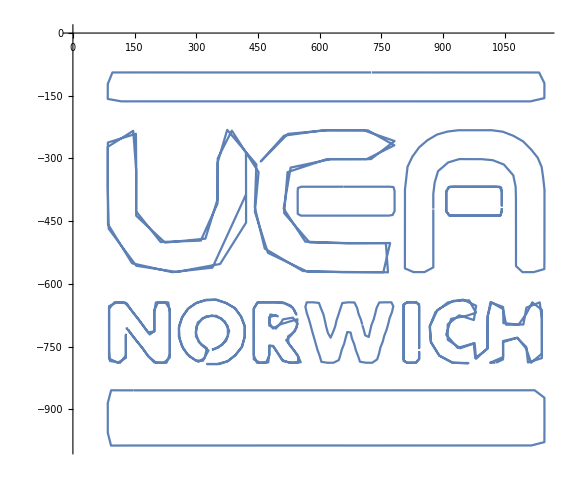

```mathematica
ParametricPlot[Evaluate[finalCurve], {t, 0,24 4Pi }]
```

## Matlab Output

```mathematica
<<ToMatlab`
```

```mathematica
StringReplace[StringReplace[ToMatlab[finalCurve],"UnitStep"->"heaviside"], "Sign"->"sign"]
```

[(((25509/31)+(-1/853).*sin((42/31)+(-143).*t)+(-1/878).*sin(( ...
  70/51)+(-141).*t)+(-1/356).*sin((19/14)+(-140).*t)+(-1/442).*sin(( ...
  23/17)+(-137).*t)+(-1/368).*sin((73/53)+(-119).*t)+(-1/551).*sin(( ...
  38/27)+(-117).*t)+(-1/174).*sin((32/23)+(-116).*t)+(-1/924).*sin(( ...
  49/34)+(-115).*t)+(-1/948).*sin((23/16)+(-114).*t)+(-1/321).*sin(( ...
  7/5)+(-113).*t)+(-1/263).*sin((38/27)+(-108).*t)+(-1/906).*sin(( ...
  54/37)+(-107).*t)+(-1/554).*sin((75/52)+(-106).*t)+(-1/115).*sin(( ...
  31/22)+(-105).*t)+(-1/433).*sin((10/7)+(-104).*t)+(-1/188).*sin(( ...
  94/67)+(-102).*t)+(-1/871).*sin((49/36)+(-95).*t)+(-1/724).*sin(( ...
  37/27)+(-87).*t)+(-1/62).*sin((59/41)+(-84).*t)+(-1/607).*sin(( ...
  55/36)+(-83).*t)+(-1/234).*sin((43/29)+(-82).*t)+(-1/39).*sin(( ...
  55/38)+(-81).*t)+(-1/103).*sin((19/13)+(-80).*t)+(-1/73).*sin(( ...
  45/31)+(-78).*t)+(-1/300).*sin((60/41)+(-77).*t)+(-1/243).*sin(( ...
  60/41)+(-73).*t)+(-1/225).*sin((25/17)+(-72).*t)+(-1/56).*sin(( ...
  19/13)+(-70).*t)+(-1/111).*sin((19/13)+(-69).*t)+(-1/315).*sin(( ...
  17/12)+(-67).*t)+(-1/56).*sin((22/15)+(-60).*t)+(-1/56).*sin(( ...
  37/25)+(-57).*t)+(-1/260).*sin((49/33)+(-56).*t)+(-1/68).*sin(( ...
  49/33)+(-52).*t)+(-1/14).*sin((136/91)+(-49).*t)+(-1/26).*sin(( ...
  146/97)+(-48).*t)+(-1/10).*sin((3/2)+(-46).*t)+(-2/31).*sin(( ...
  152/101)+(-45).*t)+(-1/26).*sin((155/103)+(-43).*t)+(-1/40).*sin(( ...
  3/2)+(-42).*t)+(-1/37).*sin((62/41)+(-35).*t)+(-1/29).*sin((68/45) ...
  +(-34).*t)+(-1/29).*sin((200/133)+(-28).*t)+(-7/32).*sin((49/32)+( ...
  -25).*t)+(-1/11).*sin((43/28)+(-24).*t)+(-11/40).*sin((63/41)+( ...
  -22).*t)+(-3/17).*sin((57/37)+(-21).*t)+(-1/24).*sin((65/42)+(-19) ...
  .*t)+(-3/28).*sin((17/11)+(-17).*t)+(-1/14).*sin((59/38)+(-16).*t) ...
  +(-26/33).*sin((31/20)+(-14).*t)+(-8/9).*sin((45/29)+(-13).*t)+( ...
  -41/31).*sin((73/47)+(-11).*t)+(-59/35).*sin((14/9)+(-10).*t)+( ...
  -26/25).*sin((81/52)+(-7).*t)+(-1/41).*sin((37/27)+(-4).*t)+( ...
  -498/37).*sin((69/44)+(-1).*t)+(389/24).*sin((74/47)+2.*t)+( ...
  167/17).*sin((52/33)+3.*t)+(96/17).*sin((30/19)+5.*t)+(116/23).* ...
  sin((30/19)+6.*t)+(5/14).*sin((49/31)+8.*t)+(31/24).*sin((46/29)+ ...
  9.*t)+(1/30).*sin((38/23)+12.*t)+(2/25).*sin((37/23)+15.*t)+(1/31) ...
  .*sin((37/23)+18.*t)+(1/107).*sin((33/20)+20.*t)+(1/53).*sin(( ...
  64/39)+23.*t)+(5/31).*sin((50/31)+26.*t)+(3/17).*sin((29/18)+27.* ...
  t)+(11/56).*sin((50/31)+29.*t)+(9/38).*sin((21/13)+30.*t)+(2/35).* ...
  sin((50/31)+32.*t)+(2/21).*sin((47/29)+33.*t)+(1/210).*sin((73/45) ...
  +36.*t)+(1/327).*sin((45/28)+37.*t)+(1/32).*sin((57/35)+38.*t)+( ...
  1/419).*sin((45/29)+39.*t)+(1/34).*sin((44/27)+40.*t)+(1/14).*sin( ...
  (18/11)+41.*t)+(1/35).*sin((43/26)+44.*t)+(1/157).*sin((80/17)+ ...
  47.*t)+(1/103).*sin((67/40)+50.*t)+(1/68).*sin((73/44)+51.*t)+( ...
  1/68).*sin((43/26)+53.*t)+(1/70).*sin((48/29)+54.*t)+(1/867).*sin( ...
  (17/10)+58.*t)+(1/169).*sin((273/164)+59.*t)+(1/53).*sin((83/50)+ ...
  61.*t)+(1/24).*sin((273/164)+62.*t)+(1/380).*sin((48/31)+63.*t)+( ...
  1/45).*sin((73/44)+64.*t)+(1/22).*sin((117/70)+65.*t)+(1/528).* ...
  sin((87/56)+66.*t)+(1/55).*sin((42/25)+68.*t)+(1/136).*sin((73/43) ...
  +76.*t)+(1/470).*sin((43/25)+85.*t)+(1/86).*sin((41/24)+86.*t)+( ...
  1/213).*sin((61/36)+88.*t)+(1/99).*sin((41/24)+89.*t)+(1/720).* ...
  sin((268/161)+90.*t)+(1/368).*sin((65/38)+94.*t)+(1/354).*sin(( ...
  39/23)+96.*t)+(1/91).*sin((43/25)+97.*t)+(1/350).*sin((27/16)+98.* ...
  t)+(1/475).*sin((52/31)+99.*t)+(1/91).*sin((88/51)+100.*t)+(1/752) ...
  .*sin((39/23)+101.*t)+(1/371).*sin((142/81)+103.*t)+(1/590).*sin(( ...
  57/32)+118.*t)+(1/193).*sin((44/25)+121.*t)+(1/881).*sin((67/39)+ ...
  122.*t)+(1/244).*sin((44/25)+124.*t)+(1/851).*sin((40/23)+125.*t)+ ...
  (1/493).*sin((39/22)+132.*t)+(1/968).*sin((37/21)+133.*t)+(1/552) ...
  .*sin((66/37)+135.*t)+(1/732).*sin((67/37)+156.*t)).*heaviside(47.* ...
  pi+(-1).*t).*heaviside((-43).*pi+t)+((53698/55)+(-1/824).*sin(( ...
  37/28)+(-169).*t)+(-1/938).*sin((89/67)+(-164).*t)+(-1/456).*sin(( ...
  41/30)+(-139).*t)+(-1/335).*sin((48/35)+(-135).*t)+(-1/853).*sin(( ...
  70/51)+(-134).*t)+(-1/525).*sin((40/29)+(-130).*t)+(-1/194).*sin(( ...
  47/34)+(-128).*t)+(-1/174).*sin((25/18)+(-124).*t)+(-1/184).*sin(( ...
  25/18)+(-123).*t)+(-1/861).*sin((46/33)+(-120).*t)+(-1/146).*sin(( ...
  53/38)+(-119).*t)+(-1/311).*sin((109/78)+(-117).*t)+(-1/359).*sin( ...
  (59/42)+(-113).*t)+(-1/172).*sin((45/32)+(-112).*t)+(-1/162).*sin( ...
  (24/17)+(-108).*t)+(-1/952).*sin((27/19)+(-101).*t)+(-1/660).*sin( ...
  (67/47)+(-98).*t)+(-1/219).*sin((53/37)+(-94).*t)+(-1/94).*sin(( ...
  62/43)+(-87).*t)+(-1/55).*sin((42/29)+(-83).*t)+(-1/67).*sin(( ...
  29/20)+(-82).*t)+(-1/278).*sin((16/11)+(-79).*t)+(-1/38).*sin(( ...
  67/46)+(-78).*t)+(-1/58).*sin((35/24)+(-76).*t)+(-1/433).*sin(( ...
  54/37)+(-75).*t)+(-1/95).*sin((19/13)+(-74).*t)+(-1/667).*sin(( ...
  60/41)+(-73).*t)+(-1/45).*sin((41/28)+(-72).*t)+(-1/32).*sin(( ...
  22/15)+(-71).*t)+(-1/168).*sin((25/17)+(-68).*t)+(-1/22).*sin(( ...
  53/36)+(-67).*t)+(-1/647).*sin((31/21)+(-64).*t)+(-1/150).*sin(( ...
  34/23)+(-63).*t)+(-1/88).*sin((37/25)+(-62).*t)+(-1/46).*sin(( ...
  40/27)+(-60).*t)+(-1/36).*sin((61/41)+(-56).*t)+(-1/440).*sin(( ...
  91/61)+(-53).*t)+(-1/248).*sin((142/95)+(-51).*t)+(-1/541).*sin(( ...
  188/125)+(-46).*t)+(-1/22).*sin((77/51)+(-42).*t)+(-1/38).*sin(( ...
  68/45)+(-41).*t)+(-4/47).*sin((44/29)+(-37).*t)+(-1/18).*sin(( ...
  38/25)+(-35).*t)+(-1/15).*sin((35/23)+(-33).*t)+(-3/20).*sin(( ...
  61/40)+(-31).*t)+(-7/39).*sin((29/19)+(-30).*t)+(-1/27).*sin(( ...
  49/32)+(-27).*t)+(-13/30).*sin((23/15)+(-26).*t)+(-1/39).*sin(( ...
  23/15)+(-25).*t)+(-1/16).*sin((43/28)+(-24).*t)+(-1/574).*sin(( ...
  63/41)+(-23).*t)+(-9/32).*sin((20/13)+(-22).*t)+(-4/21).*sin(( ...
  57/37)+(-21).*t)+(-1/9).*sin((37/24)+(-20).*t)+(-19/44).*sin(( ...
  54/35)+(-19).*t)+(-1/14).*sin((17/11)+(-17).*t)+(-1/24).*sin(( ...
  65/42)+(-16).*t)+(-100/99).*sin((48/31)+(-15).*t)+(-1/123).*sin(( ...
  59/38)+(-12).*t)+(-14/27).*sin((14/9)+(-11).*t)+(-51/64).*sin(( ...
  14/9)+(-10).*t)+(-12/59).*sin((39/25)+(-8).*t)+(-11/20).*sin(( ...
  36/23)+(-4).*t)+(-512/37).*sin((80/51)+(-1).*t)+(1288/19).*sin(( ...
  74/47)+2.*t)+(964/107).*sin((52/33)+3.*t)+(40/21).*sin((30/19)+5.* ...
  t)+(28/31).*sin((30/19)+6.*t)+(55/24).*sin((49/31)+7.*t)+(69/32).* ...
  sin((19/12)+9.*t)+(34/41).*sin((35/22)+13.*t)+(5/26).*sin((35/22)+ ...
  14.*t)+(5/23).*sin((91/57)+18.*t)+(1/26).*sin((29/18)+28.*t)+( ...
  1/107).*sin((50/31)+29.*t)+(2/31).*sin((55/34)+32.*t)+(1/29).*sin( ...
  (47/29)+34.*t)+(1/50).*sin((99/61)+36.*t)+(1/51).*sin((83/51)+38.* ...
  t)+(3/28).*sin((57/35)+39.*t)+(1/937).*sin((44/27)+40.*t)+(8/63).* ...
  sin((49/30)+43.*t)+(1/32).*sin((18/11)+44.*t)+(1/56).*sin((18/11)+ ...
  45.*t)+(1/28).*sin((41/25)+47.*t)+(1/23).*sin((64/39)+48.*t)+( ...
  1/83).*sin((23/14)+49.*t)+(1/13).*sin((51/31)+50.*t)+(1/129).*sin( ...
  (28/17)+52.*t)+(2/27).*sin((33/20)+54.*t)+(1/32).*sin((38/23)+55.* ...
  t)+(1/374).*sin((43/26)+57.*t)+(1/70).*sin((53/32)+58.*t)+(1/24).* ...
  sin((58/35)+59.*t)+(1/90).*sin((83/50)+61.*t)+(1/131).*sin((5/3)+ ...
  65.*t)+(1/157).*sin((237/142)+66.*t)+(1/82).*sin((72/43)+70.*t)+( ...
  1/182).*sin((49/29)+80.*t)+(1/67).*sin((61/36)+84.*t)+(1/985).* ...
  sin((56/33)+86.*t)+(1/182).*sin((17/10)+88.*t)+(1/521).*sin(( ...
  63/37)+89.*t)+(1/769).*sin((46/27)+90.*t)+(1/87).*sin((75/44)+91.* ...
  t)+(1/724).*sin((41/24)+93.*t)+(1/55).*sin((65/38)+95.*t)+(1/131) ...
  .*sin((89/52)+96.*t)+(1/153).*sin((79/46)+99.*t)+(1/79).*sin(( ...
  55/32)+100.*t)+(1/159).*sin((74/43)+102.*t)+(1/241).*sin((50/29)+ ...
  104.*t)+(1/138).*sin((19/11)+106.*t)+(1/205).*sin((83/48)+107.*t)+ ...
  (1/498).*sin((26/15)+110.*t)+(1/128).*sin((59/34)+111.*t)+(1/750) ...
  .*sin((7/4)+122.*t)+(1/815).*sin((79/45)+125.*t)+(1/300).*sin(( ...
  62/35)+136.*t)+(1/999).*sin((39/22)+137.*t)+(1/729).*sin((16/9)+ ...
  140.*t)+(1/400).*sin((16/9)+141.*t)+(1/817).*sin((57/32)+143.*t)+( ...
  1/646).*sin((66/37)+145.*t)+(1/392).*sin((59/33)+147.*t)+(1/665).* ...
  sin((34/19)+148.*t)+(1/943).*sin((52/29)+151.*t)+(1/351).*sin(( ...
  61/34)+152.*t)+(1/789).*sin((9/5)+156.*t)+(1/941).*sin((67/37)+ ...
  163.*t)).*heaviside(43.*pi+(-1).*t).*heaviside((-39).*pi+t)+(( ...
  20580/31)+(-1/676).*sin((27/19)+(-113).*t)+(-1/752).*sin((39/35)+( ...
  -112).*t)+(-1/852).*sin((30/41)+(-109).*t)+(-1/517).*sin((28/83)+( ...
  -106).*t)+(-1/484).*sin((39/35)+(-99).*t)+(-1/362).*sin((16/17)+( ...
  -96).*t)+(-1/289).*sin((5/24)+(-90).*t)+(-1/268).*sin((39/28)+( ...
  -89).*t)+(-1/235).*sin((53/107)+(-85).*t)+(-1/216).*sin((73/72)+( ...
  -80).*t)+(-1/156).*sin((75/74)+(-75).*t)+(-1/208).*sin((1/34)+( ...
  -74).*t)+(-1/136).*sin((25/29)+(-64).*t)+(-1/84).*sin((87/61)+( ...
  -54).*t)+(-1/43).*sin((6/19)+(-51).*t)+(-1/61).*sin((9/19)+(-48).* ...
  t)+(-1/31).*sin((9/34)+(-47).*t)+(-1/24).*sin((6/7)+(-41).*t)+( ...
  -1/42).*sin((14/13)+(-38).*t)+(-1/18).*sin((10/11)+(-37).*t)+( ...
  -1/34).*sin((14/37)+(-32).*t)+(-4/45).*sin((23/17)+(-31).*t)+( ...
  -6/55).*sin((35/24)+(-27).*t)+(-1/24).*sin((81/59)+(-22).*t)+( ...
  -1/36).*sin((10/19)+(-16).*t)+(1137/10).*sin((285/89)+t)+(25/26).* ...
  sin((95/27)+2.*t)+(191/24).*sin((7/41)+3.*t)+(14/41).*sin((68/29)+ ...
  4.*t)+(9/23).*sin((5/27)+5.*t)+(5/36).*sin((100/23)+6.*t)+(77/54) ...
  .*sin((151/42)+7.*t)+(7/29).*sin((97/31)+8.*t)+(38/25).*sin(( ...
  38/75)+9.*t)+(1/17).*sin((49/30)+10.*t)+(37/44).*sin((119/31)+11.* ...
  t)+(3/26).*sin((1031/258)+12.*t)+(11/28).*sin((47/71)+13.*t)+( ...
  3/29).*sin((47/18)+14.*t)+(2/21).*sin((61/92)+15.*t)+(7/27).*sin(( ...
  175/41)+17.*t)+(2/25).*sin((79/22)+18.*t)+(13/40).*sin((15/14)+ ...
  19.*t)+(1/22).*sin((65/37)+20.*t)+(5/23).*sin((71/16)+21.*t)+( ...
  2/21).*sin((33/28)+23.*t)+(1/21).*sin((89/30)+24.*t)+(1/26).*sin(( ...
  56/37)+25.*t)+(1/33).*sin((21/38)+26.*t)+(1/28).*sin((131/30)+28.* ...
  t)+(1/8).*sin((12/7)+29.*t)+(1/33).*sin((57/28)+30.*t)+(1/29).* ...
  sin((43/24)+33.*t)+(1/43).*sin((18/5)+34.*t)+(1/38).*sin((61/25)+ ...
  35.*t)+(1/40).*sin((12/11)+36.*t)+(2/31).*sin((54/23)+39.*t)+( ...
  1/54).*sin((47/18)+40.*t)+(1/47).*sin((7/25)+42.*t)+(1/63).*sin(( ...
  82/37)+43.*t)+(1/62).*sin((459/106)+44.*t)+(1/54).*sin((71/23)+ ...
  45.*t)+(1/61).*sin((16/9)+46.*t)+(1/29).*sin((90/31)+49.*t)+(1/70) ...
  .*sin((107/32)+50.*t)+(1/75).*sin((439/440)+52.*t)+(1/132).*sin(( ...
  115/51)+53.*t)+(1/89).*sin((186/49)+55.*t)+(1/79).*sin((44/17)+ ...
  56.*t)+(1/48).*sin((13/37)+57.*t)+(1/102).*sin((2/11)+58.*t)+( ...
  1/56).*sin((80/23)+59.*t)+(1/87).*sin((47/12)+60.*t)+(1/70).*sin(( ...
  5/38)+61.*t)+(1/103).*sin((57/31)+62.*t)+(1/229).*sin((31/14)+63.* ...
  t)+(1/125).*sin((181/39)+65.*t)+(1/98).*sin((119/37)+66.*t)+(1/77) ...
  .*sin((15/17)+67.*t)+(1/148).*sin((113/112)+68.*t)+(1/101).*sin(( ...
  78/19)+69.*t)+(1/133).*sin((130/29)+70.*t)+(1/115).*sin((16/35)+ ...
  71.*t)+(1/132).*sin((52/21)+72.*t)+(1/301).*sin((131/49)+73.*t)+( ...
  1/151).*sin((129/34)+76.*t)+(1/140).*sin((31/21)+77.*t)+(1/182).* ...
  sin((28/17)+78.*t)+(1/161).*sin((78/17)+79.*t)+(1/203).*sin(( ...
  71/89)+81.*t)+(1/203).*sin((277/92)+82.*t)+(1/293).*sin((43/13)+ ...
  83.*t)+(1/250).*sin((53/74)+84.*t)+(1/254).*sin((191/42)+86.*t)+( ...
  1/246).*sin((42/19)+87.*t)+(1/263).*sin((43/20)+88.*t)+(1/329).* ...
  sin((43/34)+91.*t)+(1/357).*sin((122/33)+92.*t)+(1/316).*sin(( ...
  125/33)+93.*t)+(1/344).*sin((14/11)+94.*t)+(1/405).*sin((6/35)+ ...
  95.*t)+(1/388).*sin((235/83)+97.*t)+(1/450).*sin((64/23)+98.*t)+( ...
  1/411).*sin((9/23)+100.*t)+(1/430).*sin((64/37)+101.*t)+(1/538).* ...
  sin((742/165)+102.*t)+(1/432).*sin((77/18)+103.*t)+(1/598).*sin(( ...
  78/41)+104.*t)+(1/611).*sin((48/49)+105.*t)+(1/684).*sin((400/123) ...
  +107.*t)+(1/724).*sin((169/47)+108.*t)+(1/714).*sin((19/20)+110.* ...
  t)+(1/539).*sin((152/71)+111.*t)+(1/856).*sin((65/38)+115.*t)+( ...
  1/823).*sin((13/64)+116.*t)+(1/695).*sin((76/29)+121.*t)+(1/880).* ...
  sin((25/8)+131.*t)).*heaviside(39.*pi+(-1).*t).*heaviside((-35).*pi+ ...
  t)+((57535/117)+(-1/26).*sin((3/17)+(-180).*t)+(-1/27).*sin(( ...
  33/23)+(-175).*t)+(-1/23).*sin((15/28)+(-173).*t)+(-1/20).*sin(( ...
  41/30)+(-168).*t)+(-1/37).*sin((1/252)+(-166).*t)+(-2/39).*sin(( ...
  22/89)+(-164).*t)+(-1/20).*sin((27/20)+(-161).*t)+(-2/35).*sin(( ...
  33/50)+(-159).*t)+(-1/29).*sin((1/26)+(-157).*t)+(-1/25).*sin(( ...
  38/33)+(-154).*t)+(-1/18).*sin((37/35)+(-152).*t)+(-1/15).*sin(( ...
  55/36)+(-147).*t)+(-3/38).*sin((6/19)+(-138).*t)+(-1/20).*sin(( ...
  54/49)+(-133).*t)+(-2/29).*sin((7/41)+(-131).*t)+(-1/12).*sin(( ...
  10/11)+(-126).*t)+(-3/37).*sin((16/13)+(-119).*t)+(-3/37).*sin(( ...
  1/11)+(-117).*t)+(-2/25).*sin((20/13)+(-114).*t)+(-3/37).*sin(( ...
  22/15)+(-112).*t)+(-4/41).*sin((66/43)+(-107).*t)+(-3/34).*sin(( ...
  61/44)+(-105).*t)+(-5/42).*sin((16/25)+(-98).*t)+(-5/46).*sin(( ...
  1/31)+(-96).*t)+(-6/43).*sin((5/9)+(-91).*t)+(-3/19).*sin((42/31)+ ...
  (-86).*t)+(-1/10).*sin((4/15)+(-84).*t)+(-5/36).*sin((9/31)+(-82) ...
  .*t)+(-1/4).*sin((81/56)+(-79).*t)+(-6/29).*sin((53/52)+(-77).*t)+ ...
  (-3/26).*sin((8/7)+(-72).*t)+(-2/17).*sin((35/37)+(-70).*t)+( ...
  -7/36).*sin((71/46)+(-65).*t)+(-9/32).*sin((11/23)+(-63).*t)+( ...
  -6/25).*sin((1/98)+(-61).*t)+(-15/34).*sin((10/27)+(-56).*t)+( ...
  -4/21).*sin((24/17)+(-53).*t)+(-13/42).*sin((67/66)+(-51).*t)+( ...
  -7/27).*sin((2/15)+(-47).*t)+(-11/23).*sin((16/11)+(-44).*t)+( ...
  -21/64).*sin((16/19)+(-42).*t)+(-4/17).*sin((2/25)+(-40).*t)+( ...
  -10/33).*sin((13/20)+(-35).*t)+(-10/59).*sin((12/59)+(-28).*t)+( ...
  -8/25).*sin((49/36)+(-23).*t)+(-25/14).*sin((3/13)+(-21).*t)+( ...
  -34/25).*sin((14/15)+(-17).*t)+(-190/23).*sin((25/28)+(-11).*t)+( ...
  -635/24).*sin((34/23)+(-1).*t)+(96/25).*sin((133/67)+2.*t)+( ...
  695/17).*sin((23/13)+3.*t)+(493/74).*sin((78/37)+4.*t)+(139/14).* ...
  sin((59/32)+5.*t)+(731/117).*sin((58/27)+6.*t)+(91/18).*sin(( ...
  44/21)+7.*t)+(23/25).*sin((89/50)+8.*t)+(79/44).*sin((52/19)+9.*t) ...
  +(181/27).*sin((13/6)+10.*t)+(151/75).*sin((35/22)+12.*t)+(31/15) ...
  .*sin((283/81)+13.*t)+(83/38).*sin((7/20)+14.*t)+(65/19).*sin(( ...
  79/25)+15.*t)+(24/17).*sin((7/12)+16.*t)+(65/34).*sin((71/27)+18.* ...
  t)+(14/15).*sin((98/27)+19.*t)+(6/5).*sin((78/29)+20.*t)+(7/13).* ...
  sin((57/25)+22.*t)+(5/17).*sin((31/32)+24.*t)+(21/46).*sin((97/27) ...
  +25.*t)+(37/62).*sin((8/23)+26.*t)+(11/50).*sin((124/39)+27.*t)+( ...
  41/47).*sin((266/71)+29.*t)+(8/29).*sin((37/41)+30.*t)+(3/11).* ...
  sin((79/17)+31.*t)+(21/52).*sin((112/33)+32.*t)+(12/17).*sin(( ...
  17/31)+33.*t)+(7/15).*sin((148/43)+34.*t)+(25/41).*sin((34/21)+ ...
  36.*t)+(6/11).*sin((75/16)+37.*t)+(23/47).*sin((61/44)+38.*t)+( ...
  14/43).*sin((113/27)+39.*t)+(3/11).*sin((53/15)+41.*t)+(8/25).* ...
  sin((33/17)+43.*t)+(10/21).*sin((52/33)+45.*t)+(2/9).*sin((27/7)+ ...
  46.*t)+(5/23).*sin((22/7)+48.*t)+(5/46).*sin((20/21)+49.*t)+(4/21) ...
  .*sin((71/30)+50.*t)+(3/23).*sin((31/30)+52.*t)+(5/36).*sin(( ...
  11/28)+54.*t)+(11/30).*sin((91/32)+55.*t)+(1/6).*sin((77/29)+57.* ...
  t)+(3/41).*sin((53/12)+58.*t)+(1/11).*sin((27/16)+59.*t)+(8/39).* ...
  sin((106/31)+60.*t)+(11/49).*sin((141/50)+62.*t)+(2/9).*sin(( ...
  99/46)+64.*t)+(6/25).*sin((17/18)+66.*t)+(7/32).*sin((104/27)+67.* ...
  t)+(8/39).*sin((23/54)+68.*t)+(5/33).*sin((158/49)+69.*t)+(2/15).* ...
  sin((73/26)+71.*t)+(1/5).*sin((46/39)+73.*t)+(5/19).*sin((86/21)+ ...
  74.*t)+(7/34).*sin((25/36)+75.*t)+(4/29).*sin((71/28)+76.*t)+(2/7) ...
  .*sin((31/17)+78.*t)+(5/28).*sin((61/43)+80.*t)+(3/31).*sin((29/8) ...
  +81.*t)+(6/47).*sin((64/19)+83.*t)+(5/26).*sin((87/43)+85.*t)+( ...
  4/43).*sin((4/3)+87.*t)+(2/21).*sin((87/26)+88.*t)+(3/28).*sin(( ...
  7/30)+89.*t)+(7/37).*sin((68/25)+90.*t)+(1/16).*sin((47/23)+92.*t) ...
  +(1/12).*sin((159/35)+93.*t)+(1/10).*sin((17/16)+94.*t)+(3/32).* ...
  sin((371/99)+95.*t)+(6/43).*sin((97/35)+97.*t)+(3/37).*sin((64/33) ...
  +99.*t)+(1/9).*sin((111/28)+100.*t)+(2/21).*sin((79/66)+101.*t)+( ...
  2/21).*sin((109/28)+102.*t)+(6/55).*sin((5/37)+103.*t)+(4/43).* ...
  sin((69/26)+104.*t)+(4/37).*sin((41/27)+106.*t)+(5/49).*sin(( ...
  36/31)+108.*t)+(3/23).*sin((101/26)+109.*t)+(2/23).*sin((16/35)+ ...
  110.*t)+(1/18).*sin((136/45)+111.*t)+(3/40).*sin((13/7)+113.*t)+( ...
  3/44).*sin((46/43)+115.*t)+(2/27).*sin((157/45)+116.*t)+(3/40).* ...
  sin((91/38)+118.*t)+(2/23).*sin((68/41)+120.*t)+(1/23).*sin(( ...
  101/22)+121.*t)+(1/23).*sin((18/29)+122.*t)+(1/13).*sin((323/81)+ ...
  123.*t)+(1/15).*sin((11/40)+124.*t)+(2/23).*sin((161/67)+125.*t)+( ...
  1/20).*sin((83/42)+127.*t)+(1/27).*sin((154/41)+128.*t)+(3/43).* ...
  sin((10/13)+129.*t)+(1/12).*sin((81/25)+130.*t)+(3/34).*sin(( ...
  52/21)+132.*t)+(1/22).*sin((19/23)+134.*t)+(1/16).*sin((147/38)+ ...
  135.*t)+(1/17).*sin((73/61)+136.*t)+(1/20).*sin((347/99)+137.*t)+( ...
  3/43).*sin((157/61)+139.*t)+(1/26).*sin((125/29)+140.*t)+(1/21).* ...
  sin((61/43)+141.*t)+(1/16).*sin((155/36)+142.*t)+(2/31).*sin(( ...
  17/20)+143.*t)+(1/12).*sin((39/11)+144.*t)+(1/19).*sin((1/37)+ ...
  145.*t)+(1/24).*sin((59/30)+146.*t)+(1/14).*sin((26/17)+148.*t)+( ...
  2/29).*sin((30/7)+149.*t)+(1/19).*sin((33/53)+150.*t)+(1/21).*sin( ...
  (73/24)+151.*t)+(2/41).*sin((99/40)+153.*t)+(1/42).*sin((52/35)+ ...
  155.*t)+(1/25).*sin((160/41)+156.*t)+(1/21).*sin((72/25)+158.*t)+( ...
  1/20).*sin((46/19)+160.*t)+(1/29).*sin((29/25)+162.*t)+(2/41).* ...
  sin((149/38)+163.*t)+(1/24).*sin((99/29)+165.*t)+(1/71).*sin(( ...
  32/13)+167.*t)+(1/34).*sin((19/16)+169.*t)+(1/32).*sin((115/31)+ ...
  170.*t)+(1/28).*sin((11/32)+171.*t)+(1/31).*sin((133/39)+172.*t)+( ...
  1/29).*sin((68/33)+174.*t)+(1/28).*sin(1+176.*t)+(1/32).*sin(( ...
  100/23)+177.*t)+(1/34).*sin((25/49)+178.*t)+(1/35).*sin((71/22)+ ...
  179.*t)).*heaviside(35.*pi+(-1).*t).*heaviside((-31).*pi+t)+(( ...
  11811/35)+(-1/22).*sin((17/22)+(-174).*t)+(-1/34).*sin((31/35)+( ...
  -173).*t)+(-1/31).*sin((18/17)+(-172).*t)+(-1/43).*sin((4/17)+( ...
  -171).*t)+(-2/33).*sin((25/43)+(-169).*t)+(-1/82).*sin((41/35)+( ...
  -167).*t)+(-1/17).*sin((61/73)+(-166).*t)+(-1/38).*sin((58/41)+( ...
  -165).*t)+(-1/19).*sin((17/21)+(-164).*t)+(-1/49).*sin((68/91)+( ...
  -162).*t)+(-1/58).*sin((31/33)+(-161).*t)+(-1/563).*sin((31/26)+( ...
  -160).*t)+(-1/34).*sin((7/13)+(-155).*t)+(-1/43).*sin((29/44)+( ...
  -150).*t)+(-1/16).*sin((36/37)+(-148).*t)+(-1/73).*sin((46/35)+( ...
  -146).*t)+(-1/38).*sin((46/91)+(-145).*t)+(-1/35).*sin((11/23)+( ...
  -141).*t)+(-1/98).*sin((1/13)+(-139).*t)+(-1/24).*sin((25/26)+( ...
  -138).*t)+(-1/24).*sin((9/10)+(-136).*t)+(-1/26).*sin((5/6)+(-134) ...
  .*t)+(-1/28).*sin((8/9)+(-131).*t)+(-2/27).*sin((13/12)+(-130).*t) ...
  +(-1/32).*sin((29/26)+(-129).*t)+(-1/77).*sin((37/38)+(-128).*t)+( ...
  -1/40).*sin((34/31)+(-126).*t)+(-1/29).*sin((25/29)+(-123).*t)+( ...
  -1/19).*sin((13/11)+(-122).*t)+(-2/33).*sin((15/14)+(-118).*t)+( ...
  -1/33).*sin((29/23)+(-112).*t)+(-1/43).*sin((34/31)+(-111).*t)+( ...
  -2/21).*sin((41/36)+(-110).*t)+(-1/43).*sin((31/23)+(-109).*t)+( ...
  -1/47).*sin((4/41)+(-107).*t)+(-1/86).*sin((31/41)+(-105).*t)+( ...
  -1/20).*sin((38/33)+(-104).*t)+(-3/38).*sin((11/10)+(-102).*t)+( ...
  -1/17).*sin((20/17)+(-100).*t)+(-1/43).*sin((7/17)+(-97).*t)+( ...
  -1/16).*sin((31/24)+(-92).*t)+(-1/23).*sin((36/29)+(-91).*t)+( ...
  -1/58).*sin((17/22)+(-90).*t)+(-1/22).*sin((41/37)+(-88).*t)+( ...
  -1/59).*sin((403/404)+(-87).*t)+(-3/37).*sin((17/14)+(-86).*t)+( ...
  -1/15).*sin((27/20)+(-85).*t)+(-4/33).*sin((14/11)+(-84).*t)+( ...
  -2/25).*sin((33/32)+(-83).*t)+(-4/37).*sin((56/43)+(-80).*t)+( ...
  -4/33).*sin((31/25)+(-79).*t)+(-1/29).*sin((41/28)+(-78).*t)+( ...
  -2/25).*sin((32/25)+(-72).*t)+(-1/20).*sin((41/39)+(-67).*t)+( ...
  -1/11).*sin((25/17)+(-66).*t)+(-1/34).*sin((41/32)+(-65).*t)+( ...
  -2/33).*sin((27/22)+(-64).*t)+(-1/12).*sin((31/23)+(-62).*t)+( ...
  -1/15).*sin((31/23)+(-61).*t)+(-2/15).*sin((41/30)+(-60).*t)+( ...
  -1/12).*sin((27/22)+(-59).*t)+(-1/12).*sin((41/28)+(-58).*t)+( ...
  -1/115).*sin((1/581)+(-57).*t)+(-3/38).*sin((40/31)+(-56).*t)+( ...
  -3/17).*sin((53/37)+(-54).*t)+(-2/23).*sin((79/59)+(-53).*t)+( ...
  -5/51).*sin((29/21)+(-52).*t)+(-2/13).*sin((91/61)+(-48).*t)+( ...
  -2/9).*sin((81/58)+(-47).*t)+(-1/5).*sin((29/20)+(-46).*t)+(-8/29) ...
  .*sin((23/16)+(-42).*t)+(-7/45).*sin((37/29)+(-41).*t)+(-13/38).* ...
  sin((32/21)+(-40).*t)+(-4/13).*sin((20/13)+(-36).*t)+(-8/29).*sin( ...
  (47/34)+(-35).*t)+(-17/36).*sin((286/191)+(-34).*t)+(-1/27).*sin(( ...
  44/31)+(-32).*t)+(-17/44).*sin((19/13)+(-30).*t)+(-11/28).*sin(( ...
  68/47)+(-29).*t)+(-11/18).*sin((97/65)+(-28).*t)+(-1/18).*sin(( ...
  15/11)+(-26).*t)+(-11/26).*sin((10/7)+(-24).*t)+(-5/27).*sin(( ...
  44/29)+(-23).*t)+(-24/25).*sin((173/115)+(-22).*t)+(-12/17).*sin(( ...
  28/19)+(-20).*t)+(-11/15).*sin((38/25)+(-18).*t)+(-2/33).*sin(( ...
  43/36)+(-17).*t)+(-49/24).*sin((59/38)+(-16).*t)+(-29/26).*sin(( ...
  31/22)+(-15).*t)+(-248/37).*sin((25/16)+(-10).*t)+(-99/14).*sin(( ...
  41/27)+(-9).*t)+(-389/33).*sin((45/29)+(-8).*t)+(-345/13).*sin(( ...
  31/20)+(-4).*t)+(-474/19).*sin((25/16)+(-1).*t)+(617/13).*sin(( ...
  30/19)+2.*t)+(338/17).*sin((19/12)+3.*t)+(175/8).*sin((51/32)+5.* ...
  t)+(12/29).*sin((3/2)+6.*t)+(12/31).*sin((25/16)+7.*t)+(5/38).* ...
  sin((1/48)+11.*t)+(24/35).*sin((101/22)+12.*t)+(62/63).*sin(( ...
  49/32)+13.*t)+(51/26).*sin((193/41)+14.*t)+(16/29).*sin((23/14)+ ...
  19.*t)+(3/41).*sin((112/25)+21.*t)+(9/35).*sin((71/41)+25.*t)+( ...
  1/354).*sin((123/124)+27.*t)+(4/19).*sin((28/17)+31.*t)+(1/9).* ...
  sin((23/15)+33.*t)+(1/22).*sin((5/7)+37.*t)+(1/16).*sin((33/16)+ ...
  38.*t)+(1/30).*sin((67/101)+39.*t)+(4/31).*sin((70/41)+43.*t)+( ...
  1/42).*sin((82/39)+44.*t)+(2/25).*sin((57/37)+45.*t)+(1/14).*sin(( ...
  53/33)+49.*t)+(1/32).*sin((17/10)+50.*t)+(3/31).*sin((41/25)+51.* ...
  t)+(1/60).*sin((242/161)+55.*t)+(1/15).*sin((82/47)+63.*t)+(1/73) ...
  .*sin((131/39)+68.*t)+(1/21).*sin((32/23)+69.*t)+(1/46).*sin(( ...
  81/35)+70.*t)+(1/33).*sin((16/11)+71.*t)+(1/16).*sin((54/29)+73.* ...
  t)+(1/60).*sin((639/137)+74.*t)+(1/56).*sin((27/23)+75.*t)+(1/122) ...
  .*sin((96/31)+76.*t)+(2/31).*sin((215/123)+77.*t)+(1/22).*sin(( ...
  59/35)+81.*t)+(2/27).*sin((52/25)+82.*t)+(3/32).*sin((75/38)+89.* ...
  t)+(1/117).*sin((47/44)+93.*t)+(1/75).*sin((109/26)+94.*t)+(1/49) ...
  .*sin((1/19)+95.*t)+(1/38).*sin((47/17)+96.*t)+(1/41).*sin((37/15) ...
  +98.*t)+(1/72).*sin((28/19)+99.*t)+(1/62).*sin((60/31)+101.*t)+( ...
  1/69).*sin((77/17)+103.*t)+(1/31).*sin((191/85)+106.*t)+(1/175).* ...
  sin((180/53)+108.*t)+(1/121).*sin((4/17)+113.*t)+(1/85).*sin(( ...
  118/27)+114.*t)+(1/55).*sin((21/17)+115.*t)+(1/82).*sin((116/43)+ ...
  116.*t)+(1/117).*sin((74/49)+117.*t)+(1/33).*sin((86/47)+119.*t)+( ...
  1/28).*sin((13/6)+120.*t)+(1/69).*sin((60/41)+121.*t)+(1/21).*sin( ...
  (67/29)+124.*t)+(1/41).*sin((11/7)+125.*t)+(1/27).*sin((70/31)+ ...
  132.*t)+(1/43).*sin((25/14)+133.*t)+(1/67).*sin((157/36)+135.*t)+( ...
  1/36).*sin((40/17)+137.*t)+(1/78).*sin((107/29)+140.*t)+(1/58).* ...
  sin((211/49)+142.*t)+(1/56).*sin((46/93)+143.*t)+(1/64).*sin(( ...
  23/6)+144.*t)+(1/329).*sin((187/41)+147.*t)+(1/86).*sin((71/16)+ ...
  149.*t)+(1/33).*sin((142/63)+151.*t)+(1/66).*sin((72/35)+152.*t)+( ...
  1/92).*sin((25/49)+153.*t)+(1/39).*sin((99/35)+154.*t)+(1/66).* ...
  sin((247/55)+156.*t)+(1/152).*sin((86/69)+157.*t)+(1/113).*sin(( ...
  27/13)+158.*t)+(1/34).*sin((33/16)+159.*t)+(1/168).*sin((83/27)+ ...
  163.*t)+(1/33).*sin((61/13)+168.*t)+(1/36).*sin((51/16)+170.*t)+( ...
  1/22).*sin((18/7)+175.*t)+(1/85).*sin((31/34)+176.*t)+(1/51).*sin( ...
  (70/31)+177.*t)+(1/52).*sin((113/45)+178.*t)+(1/224).*sin((71/59)+ ...
  179.*t)+(1/82).*sin((95/34)+180.*t)).*heaviside(31.*pi+(-1).*t).* ...
  heaviside((-27).*pi+t)+((9578/59)+(-1/66).*sin((11/39)+(-179).*t)+( ...
  -1/47).*sin((14/25)+(-175).*t)+(-1/56).*sin((53/47)+(-157).*t)+( ...
  -1/101).*sin((13/27)+(-153).*t)+(-1/121).*sin((11/17)+(-147).*t)+( ...
  -1/78).*sin((60/61)+(-146).*t)+(-1/67).*sin((27/22)+(-143).*t)+( ...
  -1/24).*sin((47/32)+(-140).*t)+(-1/42).*sin((99/79)+(-137).*t)+( ...
  -1/23).*sin((31/21)+(-135).*t)+(-1/35).*sin((39/31)+(-134).*t)+( ...
  -1/62).*sin((47/35)+(-133).*t)+(-1/21).*sin((26/23)+(-131).*t)+( ...
  -1/50).*sin((31/33)+(-130).*t)+(-1/25).*sin((33/28)+(-128).*t)+( ...
  -1/28).*sin((11/24)+(-121).*t)+(-1/25).*sin((31/24)+(-118).*t)+( ...
  -1/69).*sin((3/8)+(-116).*t)+(-1/14).*sin((20/23)+(-111).*t)+( ...
  -1/17).*sin((19/56)+(-107).*t)+(-1/69).*sin((25/22)+(-104).*t)+( ...
  -2/25).*sin((13/42)+(-100).*t)+(-1/19).*sin((24/35)+(-96).*t)+( ...
  -1/69).*sin((62/45)+(-90).*t)+(-1/101).*sin((31/28)+(-86).*t)+( ...
  -2/21).*sin((17/11)+(-70).*t)+(-2/31).*sin((25/27)+(-55).*t)+( ...
  -1/15).*sin((29/33)+(-51).*t)+(-2/23).*sin((21/29)+(-43).*t)+( ...
  -3/7).*sin((13/21)+(-32).*t)+(-17/22).*sin((42/29)+(-23).*t)+( ...
  -8/11).*sin((20/29)+(-21).*t)+(-5/14).*sin((49/33)+(-17).*t)+( ...
  -51/37).*sin((11/21)+(-12).*t)+(1631/29).*sin((45/29)+t)+(681/28) ...
  .*sin((107/23)+2.*t)+(436/11).*sin((157/34)+3.*t)+(42/13).*sin(( ...
  19/7)+4.*t)+(243/16).*sin((97/21)+5.*t)+(121/29).*sin((31/7)+6.*t) ...
  +(66/47).*sin((86/47)+7.*t)+(10/31).*sin((12/17)+8.*t)+(101/35).* ...
  sin((181/40)+9.*t)+(7/11).*sin((110/31)+10.*t)+(159/55).*sin(( ...
  37/30)+11.*t)+(69/40).*sin((65/31)+13.*t)+(234/47).*sin((228/53)+ ...
  14.*t)+(37/30).*sin((51/14)+15.*t)+(5/16).*sin((34/27)+16.*t)+( ...
  14/19).*sin((107/28)+18.*t)+(11/17).*sin((122/33)+19.*t)+(9/29).* ...
  sin((117/88)+20.*t)+(57/40).*sin((104/83)+22.*t)+(4/9).*sin(( ...
  1183/394)+24.*t)+(8/11).*sin((106/31)+25.*t)+(50/99).*sin((75/19)+ ...
  26.*t)+(5/24).*sin((29/33)+27.*t)+(1/26).*sin((183/46)+28.*t)+( ...
  13/25).*sin((79/24)+29.*t)+(21/47).*sin((125/33)+30.*t)+(13/31).* ...
  sin((340/341)+31.*t)+(3/22).*sin((68/29)+33.*t)+(5/16).*sin(( ...
  95/32)+34.*t)+(9/55).*sin((196/53)+35.*t)+(2/19).*sin((175/72)+ ...
  36.*t)+(6/31).*sin((101/33)+37.*t)+(5/32).*sin((250/77)+38.*t)+( ...
  1/16).*sin((52/35)+39.*t)+(1/20).*sin((179/38)+40.*t)+(4/41).*sin( ...
  (72/23)+41.*t)+(1/16).*sin((51/25)+42.*t)+(1/23).*sin((46/13)+44.* ...
  t)+(2/11).*sin((41/16)+45.*t)+(7/46).*sin((74/31)+46.*t)+(4/45).* ...
  sin((171/46)+47.*t)+(7/27).*sin((61/29)+48.*t)+(2/21).*sin((72/19) ...
  +49.*t)+(1/17).*sin((19/17)+50.*t)+(1/21).*sin((68/21)+52.*t)+( ...
  9/46).*sin((64/31)+53.*t)+(1/53).*sin((57/14)+54.*t)+(1/28).*sin(( ...
  16/5)+56.*t)+(4/11).*sin((60/31)+57.*t)+(2/33).*sin((130/37)+58.* ...
  t)+(1/18).*sin((27/19)+59.*t)+(1/100).*sin((85/19)+60.*t)+(1/21).* ...
  sin((56/13)+61.*t)+(1/14).*sin((37/23)+62.*t)+(1/181).*sin(( ...
  208/47)+63.*t)+(1/18).*sin((44/21)+64.*t)+(1/37).*sin((262/57)+ ...
  65.*t)+(1/17).*sin((35/24)+66.*t)+(1/58).*sin((191/44)+67.*t)+( ...
  4/19).*sin((33/20)+68.*t)+(2/19).*sin((45/31)+69.*t)+(1/36).*sin(( ...
  89/26)+71.*t)+(1/15).*sin((42/29)+72.*t)+(3/41).*sin((41/35)+73.* ...
  t)+(1/55).*sin((178/43)+74.*t)+(1/41).*sin((96/37)+75.*t)+(3/40).* ...
  sin((35/32)+76.*t)+(5/41).*sin((50/43)+77.*t)+(1/15).*sin((35/27)+ ...
  78.*t)+(1/11).*sin((52/45)+79.*t)+(3/22).*sin(1+80.*t)+(1/13).* ...
  sin((32/29)+81.*t)+(1/181).*sin((97/48)+82.*t)+(1/12).*sin((20/19) ...
  +83.*t)+(2/25).*sin((59/98)+84.*t)+(1/20).*sin((97/65)+85.*t)+( ...
  2/35).*sin((29/86)+87.*t)+(2/27).*sin((32/25)+88.*t)+(1/22).*sin(( ...
  21/5)+89.*t)+(1/33).*sin((29/34)+91.*t)+(1/21).*sin((34/15)+92.*t) ...
  +(3/28).*sin((43/10)+93.*t)+(1/22).*sin((103/42)+94.*t)+(1/31).* ...
  sin((63/37)+95.*t)+(1/23).*sin((19/33)+97.*t)+(1/115).*sin((75/31) ...
  +98.*t)+(1/46).*sin((19/16)+99.*t)+(1/20).*sin((11/20)+101.*t)+( ...
  1/52).*sin((115/28)+102.*t)+(1/33).*sin((55/36)+103.*t)+(1/26).* ...
  sin((107/29)+105.*t)+(1/22).*sin((35/23)+106.*t)+(1/38).*sin(( ...
  77/18)+108.*t)+(2/41).*sin((71/26)+109.*t)+(1/21).*sin((19/20)+ ...
  110.*t)+(1/41).*sin((86/21)+112.*t)+(1/20).*sin((41/24)+113.*t)+( ...
  1/54).*sin((25/34)+114.*t)+(1/22).*sin((1111/247)+115.*t)+(2/37).* ...
  sin((13/27)+117.*t)+(1/20).*sin((89/19)+119.*t)+(1/21).*sin(( ...
  53/107)+120.*t)+(1/18).*sin((860/191)+122.*t)+(1/60).*sin((35/44)+ ...
  123.*t)+(1/30).*sin((7/33)+124.*t)+(1/61).*sin((117/31)+125.*t)+( ...
  1/71).*sin((69/19)+126.*t)+(1/36).*sin((9/23)+127.*t)+(1/76).*sin( ...
  (64/21)+129.*t)+(1/215).*sin((56/23)+132.*t)+(1/243).*sin((47/63)+ ...
  136.*t)+(1/41).*sin((89/20)+138.*t)+(1/22).*sin((173/37)+139.*t)+( ...
  1/118).*sin((221/79)+141.*t)+(1/54).*sin((79/17)+142.*t)+(1/66).* ...
  sin((244/53)+144.*t)+(1/70).*sin((56/27)+145.*t)+(1/66).*sin(( ...
  25/16)+148.*t)+(1/470).*sin((103/34)+149.*t)+(1/30).*sin((74/17)+ ...
  150.*t)+(1/48).*sin((109/26)+151.*t)+(1/33).*sin((29/22)+152.*t)+( ...
  1/31).*sin((293/69)+154.*t)+(1/77).*sin((70/29)+155.*t)+(1/50).* ...
  sin((15/23)+156.*t)+(1/72).*sin((13/4)+158.*t)+(1/218).*sin(( ...
  115/39)+159.*t)+(1/90).*sin((188/41)+160.*t)+(1/40).*sin((19/5)+ ...
  161.*t)+(1/44).*sin((74/23)+162.*t)+(1/78).*sin((103/24)+163.*t)+( ...
  1/96).*sin((67/19)+164.*t)+(1/40).*sin((136/39)+165.*t)+(1/42).* ...
  sin((139/39)+166.*t)+(1/85).*sin((103/37)+167.*t)+(1/66).*sin(( ...
  104/25)+168.*t)+(1/42).*sin((88/29)+169.*t)+(1/46).*sin((114/35)+ ...
  170.*t)+(1/150).*sin((100/33)+171.*t)+(1/128).*sin((131/31)+172.* ...
  t)+(1/50).*sin((62/23)+173.*t)+(1/153).*sin((259/72)+174.*t)+( ...
  1/83).*sin((17/27)+176.*t)+(1/95).*sin((88/21)+177.*t)+(1/438).* ...
  sin((48/145)+180.*t)).*heaviside(27.*pi+(-1).*t).*heaviside((-23).* ...
  pi+t)+((8732/13)+(-1/268).*sin((30/43)+(-171).*t)+(-1/92).*sin(( ...
  35/29)+(-167).*t)+(-1/119).*sin((34/25)+(-162).*t)+(-1/93).*sin(( ...
  9/13)+(-160).*t)+(-1/103).*sin((7/37)+(-156).*t)+(-1/86).*sin(( ...
  29/24)+(-155).*t)+(-1/186).*sin((48/41)+(-153).*t)+(-1/755).*sin(( ...
  8/37)+(-151).*t)+(-1/406).*sin((17/16)+(-144).*t)+(-1/131).*sin(( ...
  40/67)+(-137).*t)+(-1/51).*sin((11/26)+(-128).*t)+(-1/15).*sin(( ...
  29/34)+(-125).*t)+(-1/228).*sin((49/39)+(-124).*t)+(-1/68).*sin(( ...
  8/15)+(-119).*t)+(-1/77).*sin((3/25)+(-116).*t)+(-1/23).*sin(( ...
  26/19)+(-111).*t)+(-1/18).*sin((34/31)+(-106).*t)+(-2/33).*sin(( ...
  1/6)+(-104).*t)+(-3/34).*sin((14/31)+(-100).*t)+(-2/21).*sin(( ...
  19/40)+(-99).*t)+(-5/46).*sin((11/8)+(-95).*t)+(-1/22).*sin((2/9)+ ...
  (-90).*t)+(-1/13).*sin((6/49)+(-89).*t)+(-1/26).*sin((20/41)+(-78) ...
  .*t)+(-1/26).*sin((133/132)+(-77).*t)+(-1/14).*sin((488/489)+(-71) ...
  .*t)+(-1/17).*sin((27/22)+(-67).*t)+(-1/40).*sin((3/13)+(-66).*t)+ ...
  (-2/27).*sin((11/24)+(-60).*t)+(-1/164).*sin((1/260)+(-55).*t)+( ...
  -1/15).*sin((17/37)+(-48).*t)+(-4/35).*sin((16/31)+(-46).*t)+( ...
  -2/23).*sin((9/44)+(-44).*t)+(-7/62).*sin((23/47)+(-43).*t)+( ...
  -3/22).*sin((38/29)+(-40).*t)+(-1/53).*sin((26/19)+(-36).*t)+( ...
  -1/26).*sin((8/25)+(-29).*t)+(-11/49).*sin((5/12)+(-23).*t)+( ...
  -1/26).*sin((25/24)+(-22).*t)+(-1/50).*sin((1/41)+(-17).*t)+( ...
  -7/31).*sin((8/13)+(-16).*t)+(-14/17).*sin((61/41)+(-10).*t)+( ...
  -251/59).*sin((14/19)+(-9).*t)+(-199/21).*sin((19/15)+(-3).*t)+( ...
  -56/17).*sin((50/57)+(-2).*t)+(2192/25).*sin((65/24)+t)+(85/14).* ...
  sin((61/43)+4.*t)+(83/29).*sin((29/31)+5.*t)+(25/8).*sin((11/19)+ ...
  6.*t)+(67/27).*sin((151/46)+7.*t)+(38/31).*sin((111/38)+8.*t)+( ...
  10/17).*sin((109/24)+11.*t)+(32/33).*sin((61/48)+12.*t)+(3/22).* ...
  sin((49/19)+13.*t)+(59/31).*sin((125/37)+14.*t)+(6/35).*sin((2/13) ...
  +15.*t)+(7/16).*sin((102/65)+18.*t)+(25/26).*sin((40/33)+19.*t)+( ...
  3/22).*sin((681/146)+20.*t)+(2/39).*sin((27/35)+21.*t)+(3/46).* ...
  sin((129/64)+24.*t)+(1/40).*sin((65/64)+25.*t)+(1/20).*sin((14/3)+ ...
  26.*t)+(3/16).*sin((81/22)+27.*t)+(3/25).*sin((78/23)+28.*t)+(1/7) ...
  .*sin((39/25)+30.*t)+(1/12).*sin((65/27)+31.*t)+(3/19).*sin(( ...
  131/28)+32.*t)+(3/38).*sin((148/39)+33.*t)+(9/31).*sin((65/16)+ ...
  34.*t)+(7/31).*sin((25/23)+35.*t)+(5/44).*sin((97/31)+37.*t)+( ...
  3/29).*sin((59/19)+38.*t)+(3/26).*sin((127/27)+39.*t)+(1/35).*sin( ...
  (40/27)+41.*t)+(1/4).*sin((18/23)+42.*t)+(3/26).*sin((38/11)+45.* ...
  t)+(1/21).*sin((11/13)+47.*t)+(4/45).*sin((16/35)+49.*t)+(3/41).* ...
  sin((91/29)+50.*t)+(1/16).*sin((61/30)+51.*t)+(2/25).*sin((83/48)+ ...
  52.*t)+(1/19).*sin((43/60)+53.*t)+(1/16).*sin((89/51)+54.*t)+( ...
  1/30).*sin((87/23)+56.*t)+(5/34).*sin((90/23)+57.*t)+(2/29).*sin(( ...
  17/16)+58.*t)+(1/24).*sin((101/51)+59.*t)+(1/12).*sin((53/17)+61.* ...
  t)+(1/343).*sin((167/39)+62.*t)+(1/15).*sin((85/21)+63.*t)+(4/35) ...
  .*sin((160/61)+64.*t)+(3/32).*sin((17/27)+65.*t)+(1/64).*sin((7/2) ...
  +68.*t)+(1/53).*sin((89/27)+69.*t)+(1/26).*sin((89/36)+70.*t)+( ...
  1/12).*sin((1/29)+72.*t)+(1/31).*sin((160/41)+73.*t)+(1/37).*sin(( ...
  68/37)+74.*t)+(1/14).*sin((68/47)+75.*t)+(1/49).*sin((164/91)+76.* ...
  t)+(2/29).*sin((131/29)+79.*t)+(3/32).*sin((37/13)+80.*t)+(1/28).* ...
  sin((20/9)+81.*t)+(2/27).*sin((11/15)+82.*t)+(5/54).*sin((103/24)+ ...
  83.*t)+(3/26).*sin((141/41)+84.*t)+(1/42).*sin((91/30)+85.*t)+( ...
  1/20).*sin((127/52)+86.*t)+(1/20).*sin((66/17)+87.*t)+(2/31).*sin( ...
  (159/35)+88.*t)+(7/34).*sin((1/23)+91.*t)+(1/12).*sin((6/23)+92.* ...
  t)+(8/65).*sin((148/45)+93.*t)+(1/9).*sin((43/30)+94.*t)+(4/23).* ...
  sin((27/25)+96.*t)+(1/17).*sin((40/49)+97.*t)+(1/15).*sin((212/47) ...
  +98.*t)+(1/54).*sin((100/23)+101.*t)+(1/24).*sin((10/33)+102.*t)+( ...
  1/39).*sin((141/37)+103.*t)+(1/20).*sin((12/5)+105.*t)+(1/29).* ...
  sin((19/36)+107.*t)+(1/78).*sin((5/29)+108.*t)+(1/25).*sin((5/26)+ ...
  109.*t)+(1/77).*sin((109/29)+110.*t)+(1/100).*sin((42/17)+112.*t)+ ...
  (1/36).*sin((114/29)+113.*t)+(1/79).*sin((193/43)+114.*t)+(1/30).* ...
  sin((44/87)+115.*t)+(1/59).*sin((94/67)+117.*t)+(1/38).*sin(( ...
  123/28)+118.*t)+(1/27).*sin((30/7)+120.*t)+(1/70).*sin((63/22)+ ...
  121.*t)+(1/84).*sin((90/41)+122.*t)+(1/32).*sin((139/32)+123.*t)+( ...
  1/57).*sin((37/24)+126.*t)+(1/29).*sin((34/23)+127.*t)+(1/53).* ...
  sin((33/13)+129.*t)+(1/51).*sin((3/7)+130.*t)+(1/54).*sin((7/9)+ ...
  131.*t)+(1/81).*sin((11/19)+132.*t)+(1/95).*sin((23/32)+133.*t)+( ...
  1/42).*sin((23/7)+134.*t)+(1/64).*sin((11/16)+135.*t)+(1/198).* ...
  sin((6/5)+136.*t)+(1/72).*sin(3+138.*t)+(1/223).*sin((74/17)+139.* ...
  t)+(1/75).*sin((49/36)+140.*t)+(1/47).*sin((109/26)+141.*t)+( ...
  1/101).*sin((249/53)+142.*t)+(1/70).*sin((121/35)+143.*t)+(1/173) ...
  .*sin((71/28)+145.*t)+(1/190).*sin((107/35)+146.*t)+(1/189).*sin(( ...
  55/24)+147.*t)+(1/100).*sin((156/37)+148.*t)+(1/274).*sin((43/32)+ ...
  149.*t)+(1/123).*sin((67/28)+150.*t)+(1/76).*sin((81/25)+152.*t)+( ...
  1/101).*sin((10/13)+154.*t)+(1/82).*sin((149/32)+157.*t)+(1/155).* ...
  sin((80/31)+158.*t)+(1/95).*sin((22/19)+159.*t)+(1/171).*sin(( ...
  191/52)+161.*t)+(1/181).*sin((152/39)+163.*t)+(1/223).*sin((78/35) ...
  +164.*t)+(1/226).*sin((20/39)+165.*t)+(1/203).*sin((99/26)+166.*t) ...
  +(1/149).*sin((99/37)+168.*t)+(1/189).*sin((43/22)+169.*t)+(1/113) ...
  .*sin((66/67)+170.*t)+(1/290).*sin((233/50)+172.*t)+(1/168).*sin(( ...
  111/29)+173.*t)+(1/137).*sin((115/82)+174.*t)+(1/130).*sin((39/35) ...
  +175.*t)+(1/149).*sin((4/35)+176.*t)+(1/235).*sin((49/18)+178.*t)+ ...
  (1/394).*sin((30/17)+179.*t)+(1/248).*sin((78/19)+180.*t)).* ...
  heaviside(23.*pi+(-1).*t).*heaviside((-19).*pi+t)+((152409/151)+( ...
  -4/39).*sin((31/21)+(-154).*t)+(-1/13).*sin((47/33)+(-151).*t)+( ...
  -3/31).*sin((31/25)+(-150).*t)+(-5/42).*sin((78/67)+(-147).*t)+( ...
  -2/31).*sin((26/21)+(-143).*t)+(-3/35).*sin((24/25)+(-140).*t)+( ...
  -2/35).*sin((7/9)+(-139).*t)+(-6/49).*sin((39/47)+(-136).*t)+( ...
  -1/16).*sin((22/17)+(-133).*t)+(-2/19).*sin((2/9)+(-132).*t)+( ...
  -3/19).*sin((4/7)+(-129).*t)+(-1/11).*sin((9/20)+(-126).*t)+( ...
  -15/76).*sin((9/44)+(-125).*t)+(-10/79).*sin((5/26)+(-122).*t)+( ...
  -8/49).*sin((10/37)+(-121).*t)+(-1/46).*sin((61/73)+(-119).*t)+( ...
  -1/27).*sin((23/26)+(-117).*t)+(-1/10).*sin((5/19)+(-115).*t)+( ...
  -7/26).*sin((74/49)+(-77).*t)+(-6/25).*sin((5/4)+(-76).*t)+( ...
  -12/61).*sin((19/14)+(-73).*t)+(-14/55).*sin((97/73)+(-69).*t)+( ...
  -7/38).*sin((28/55)+(-66).*t)+(-3/17).*sin((47/36)+(-65).*t)+( ...
  -6/37).*sin((1/31)+(-58).*t)+(-15/38).*sin((35/61)+(-55).*t)+( ...
  -7/22).*sin((27/31)+(-51).*t)+(-59/117).*sin((9/26)+(-48).*t)+( ...
  -9/46).*sin((11/35)+(-47).*t)+(-50/101).*sin((4/35)+(-37).*t)+( ...
  -14/47).*sin((43/39)+(-33).*t)+(-239/21).*sin((17/11)+(-7).*t)+( ...
  2897/27).*sin((23/15)+t)+(790/81).*sin((173/37)+2.*t)+(1183/41).* ...
  sin((87/19)+3.*t)+(857/35).*sin((173/38)+4.*t)+(724/49).*sin(( ...
  155/34)+5.*t)+(41/10).*sin((123/31)+6.*t)+(548/27).*sin((41/28)+ ...
  8.*t)+(789/41).*sin((114/25)+9.*t)+(88/17).*sin((97/58)+10.*t)+( ...
  74/19).*sin((20/21)+11.*t)+(223/41).*sin((133/31)+12.*t)+(22/39).* ...
  sin((83/21)+13.*t)+(73/29).*sin((61/47)+14.*t)+(91/27).*sin(( ...
  185/41)+15.*t)+(205/88).*sin((47/32)+16.*t)+(79/63).*sin((132/29)+ ...
  17.*t)+(5/32).*sin((107/42)+18.*t)+(40/33).*sin((25/34)+19.*t)+( ...
  23/21).*sin((36/35)+20.*t)+(27/23).*sin((103/24)+21.*t)+(22/21).* ...
  sin((16/13)+22.*t)+(51/26).*sin((8/21)+23.*t)+(37/33).*sin(( ...
  118/117)+24.*t)+(51/23).*sin((89/23)+25.*t)+(50/17).*sin((168/47)+ ...
  26.*t)+(30/11).*sin((107/29)+27.*t)+(37/24).*sin((94/27)+28.*t)+( ...
  7/30).*sin((212/47)+29.*t)+(1/4).*sin((29/13)+30.*t)+(65/28).*sin( ...
  (93/26)+31.*t)+(35/17).*sin((194/59)+32.*t)+(29/32).*sin((9/17)+ ...
  34.*t)+(6/19).*sin((140/33)+35.*t)+(9/41).*sin((101/43)+36.*t)+( ...
  11/37).*sin((1346/449)+38.*t)+(30/29).*sin((179/56)+39.*t)+(41/55) ...
  .*sin((116/39)+40.*t)+(22/67).*sin((465/133)+41.*t)+(20/43).*sin(( ...
  96/37)+42.*t)+(16/49).*sin((97/26)+43.*t)+(11/35).*sin((30/59)+ ...
  44.*t)+(16/47).*sin((89/27)+45.*t)+(21/26).*sin((171/61)+46.*t)+( ...
  5/31).*sin((89/29)+49.*t)+(9/22).*sin((37/15)+50.*t)+(9/62).*sin(( ...
  19/30)+52.*t)+(11/17).*sin((179/65)+53.*t)+(7/23).*sin((26/11)+ ...
  54.*t)+(13/59).*sin((107/39)+56.*t)+(13/40).*sin((12/5)+57.*t)+( ...
  5/24).*sin((40/9)+59.*t)+(11/24).*sin((167/84)+60.*t)+(5/46).*sin( ...
  (159/67)+61.*t)+(3/28).*sin((73/17)+62.*t)+(3/14).*sin((31/19)+ ...
  63.*t)+(20/59).*sin((61/27)+64.*t)+(7/25).*sin((63/26)+67.*t)+( ...
  15/43).*sin((31/18)+68.*t)+(2/23).*sin((179/39)+70.*t)+(5/28).* ...
  sin((29/21)+71.*t)+(2/25).*sin((218/77)+72.*t)+(3/20).*sin(( ...
  131/105)+74.*t)+(3/26).*sin((45/17)+75.*t)+(7/55).*sin((163/82)+ ...
  78.*t)+(1/17).*sin((11/28)+79.*t)+(13/46).*sin((50/11)+80.*t)+( ...
  4/25).*sin((778/173)+81.*t)+(3/19).*sin((57/49)+82.*t)+(1/25).* ...
  sin((52/17)+83.*t)+(1/12).*sin((14/13)+84.*t)+(4/17).*sin((56/45)+ ...
  85.*t)+(6/55).*sin((52/33)+86.*t)+(5/36).*sin((103/22)+87.*t)+( ...
  1/23).*sin((96/29)+88.*t)+(4/19).*sin((16/15)+89.*t)+(3/28).*sin(( ...
  40/41)+90.*t)+(4/17).*sin((168/41)+91.*t)+(1/31).*sin((11/14)+92.* ...
  t)+(2/13).*sin((9/11)+93.*t)+(2/33).*sin((43/14)+94.*t)+(3/17).* ...
  sin((61/14)+95.*t)+(5/31).*sin((11/10)+96.*t)+(11/50).*sin((17/23) ...
  +97.*t)+(1/15).*sin((13/18)+98.*t)+(1/28).*sin((16/25)+99.*t)+( ...
  3/19).*sin((4/5)+100.*t)+(1/13).*sin((62/15)+101.*t)+(9/64).*sin(( ...
  353/98)+102.*t)+(10/71).*sin((76/153)+103.*t)+(7/33).*sin((29/52)+ ...
  104.*t)+(5/37).*sin((139/37)+105.*t)+(3/34).*sin((62/19)+106.*t)+( ...
  9/55).*sin((6/25)+107.*t)+(1/20).*sin((43/60)+108.*t)+(5/31).*sin( ...
  (99/28)+109.*t)+(3/37).*sin((21/47)+110.*t)+(7/33).*sin((4/25)+ ...
  111.*t)+(1/36).*sin((52/19)+112.*t)+(5/39).*sin((161/47)+113.*t)+( ...
  1/14).*sin((16/35)+114.*t)+(4/35).*sin((117/41)+116.*t)+(5/23).* ...
  sin((1/28)+118.*t)+(1/19).*sin((85/32)+120.*t)+(4/41).*sin((97/36) ...
  +123.*t)+(1/29).*sin((2401/600)+124.*t)+(7/43).*sin((97/35)+127.* ...
  t)+(1/63).*sin((10/27)+128.*t)+(1/12).*sin((69/29)+130.*t)+(1/32) ...
  .*sin((17/4)+131.*t)+(3/28).*sin((51/23)+134.*t)+(1/138).*sin(( ...
  232/53)+135.*t)+(1/25).*sin(2+137.*t)+(1/8).*sin((88/37)+138.*t)+( ...
  2/19).*sin((61/28)+141.*t)+(1/122).*sin((55/41)+142.*t)+(1/29).* ...
  sin((35/22)+144.*t)+(2/29).*sin((76/35)+145.*t)+(1/47).*sin(( ...
  36/19)+146.*t)+(2/29).*sin((37/19)+148.*t)+(3/40).*sin((40/21)+ ...
  149.*t)+(2/35).*sin((35/19)+152.*t)+(1/52).*sin((50/41)+153.*t)+( ...
  1/43).*sin((273/68)+155.*t)+(1/26).*sin((10/9)+156.*t)+(1/63).* ...
  sin((142/33)+157.*t)+(1/23).*sin((212/47)+158.*t)+(3/32).*sin(( ...
  39/28)+159.*t)+(4/45).*sin((11/8)+160.*t)+(6/53).*sin((427/95)+ ...
  161.*t)+(1/57).*sin((97/27)+162.*t)+(2/29).*sin((36/41)+163.*t)+( ...
  1/33).*sin((161/47)+164.*t)+(3/23).*sin((101/23)+165.*t)+(1/23).* ...
  sin((34/35)+166.*t)+(2/37).*sin((19/16)+167.*t)+(2/29).*sin(4+ ...
  168.*t)+(2/23).*sin((337/75)+169.*t)+(1/12).*sin((45/37)+170.*t)+( ...
  1/32).*sin((19/18)+171.*t)+(1/31).*sin((78/17)+172.*t)+(1/34).* ...
  sin((23/19)+173.*t)+(3/34).*sin((21/23)+174.*t)+(1/37).*sin(( ...
  167/37)+175.*t)+(3/32).*sin((104/27)+176.*t)+(1/33).*sin((23/19)+ ...
  177.*t)+(1/25).*sin((1/54)+178.*t)+(4/37).*sin((101/28)+179.*t)+( ...
  1/30).*sin((172/45)+180.*t)).*heaviside(19.*pi+(-1).*t).*heaviside(( ...
  -15).*pi+t)+((60565/62)+(-1/76).*sin((24/25)+(-178).*t)+(-1/63).* ...
  sin((31/21)+(-172).*t)+(-1/54).*sin((27/20)+(-166).*t)+(-1/81).* ...
  sin((11/7)+(-162).*t)+(-1/92).*sin((14/23)+(-158).*t)+(-1/35).* ...
  sin((10/37)+(-147).*t)+(-1/38).*sin((22/23)+(-143).*t)+(-1/36).* ...
  sin((3/25)+(-139).*t)+(-1/59).*sin((7/10)+(-135).*t)+(-1/22).*sin( ...
  (94/73)+(-124).*t)+(-1/28).*sin((8/29)+(-122).*t)+(-1/55).*sin(( ...
  17/13)+(-120).*t)+(-1/31).*sin((21/32)+(-118).*t)+(-1/96).*sin(( ...
  4/19)+(-117).*t)+(-1/41).*sin((1/16)+(-116).*t)+(-1/50).*sin(( ...
  7/22)+(-112).*t)+(-1/60).*sin((28/37)+(-106).*t)+(-1/39).*sin(( ...
  22/41)+(-100).*t)+(-1/82).*sin((38/31)+(-99).*t)+(-1/47).*sin(( ...
  7/5)+(-96).*t)+(-1/40).*sin((35/24)+(-95).*t)+(-1/18).*sin((7/25)+ ...
  (-89).*t)+(-1/22).*sin((29/38)+(-83).*t)+(-1/27).*sin((23/42)+( ...
  -80).*t)+(-1/47).*sin((221/220)+(-77).*t)+(-1/22).*sin((29/34)+( ...
  -72).*t)+(-1/29).*sin((17/38)+(-68).*t)+(-2/23).*sin((19/34)+(-66) ...
  .*t)+(-1/17).*sin((13/22)+(-57).*t)+(-2/31).*sin((25/39)+(-56).*t) ...
  +(-1/41).*sin((4/23)+(-55).*t)+(-1/26).*sin((17/37)+(-53).*t)+( ...
  -1/21).*sin((2/21)+(-49).*t)+(-3/31).*sin((5/6)+(-34).*t)+(-7/20) ...
  .*sin((19/42)+(-33).*t)+(-7/41).*sin((19/14)+(-30).*t)+(-2/25).* ...
  sin((15/41)+(-20).*t)+(-51/76).*sin((8/23)+(-19).*t)+(-32/27).* ...
  sin((31/22)+(-16).*t)+(-53/42).*sin((13/25)+(-10).*t)+(-2918/17).* ...
  sin((25/37)+(-1).*t)+(229/8).*sin((88/49)+2.*t)+(853/37).*sin(( ...
  115/27)+3.*t)+(282/23).*sin((207/58)+4.*t)+(634/47).*sin((29/10)+ ...
  5.*t)+(166/43).*sin((185/84)+6.*t)+(160/31).*sin((313/67)+7.*t)+( ...
  9/40).*sin((290/63)+8.*t)+(121/40).*sin((6/29)+9.*t)+(7/3).*sin(( ...
  209/105)+11.*t)+(28/9).*sin((58/45)+12.*t)+(9/20).*sin((21/32)+ ...
  13.*t)+(61/51).*sin((105/34)+14.*t)+(2/41).*sin((64/17)+15.*t)+( ...
  17/22).*sin((121/29)+17.*t)+(25/51).*sin((13/27)+18.*t)+(5/36).* ...
  sin((48/29)+21.*t)+(1/23).*sin((99/26)+22.*t)+(9/34).*sin((113/35) ...
  +23.*t)+(6/37).*sin((69/28)+24.*t)+(3/28).*sin((75/44)+25.*t)+( ...
  3/17).*sin((23/20)+26.*t)+(1/23).*sin((8/31)+27.*t)+(4/21).*sin(( ...
  37/12)+28.*t)+(3/31).*sin((50/21)+29.*t)+(2/21).*sin((128/31)+31.* ...
  t)+(5/26).*sin((10/49)+32.*t)+(27/107).*sin((252/151)+35.*t)+( ...
  1/19).*sin((13/37)+36.*t)+(7/32).*sin((103/32)+37.*t)+(2/17).*sin( ...
  (30/13)+38.*t)+(3/31).*sin((128/29)+39.*t)+(7/26).*sin((79/18)+ ...
  40.*t)+(1/17).*sin((113/34)+41.*t)+(2/15).*sin((6/47)+42.*t)+( ...
  1/47).*sin((221/74)+43.*t)+(3/37).*sin((11/8)+44.*t)+(1/15).*sin(( ...
  12/17)+45.*t)+(1/29).*sin((81/32)+46.*t)+(2/29).*sin((82/29)+47.* ...
  t)+(1/33).*sin((87/43)+48.*t)+(1/22).*sin((43/35)+50.*t)+(1/27).* ...
  sin((126/31)+51.*t)+(2/35).*sin((75/26)+52.*t)+(2/33).*sin((71/19) ...
  +54.*t)+(3/37).*sin((77/40)+58.*t)+(4/33).*sin((23/22)+59.*t)+( ...
  1/21).*sin((127/33)+60.*t)+(2/35).*sin((105/53)+61.*t)+(1/76).* ...
  sin((69/19)+62.*t)+(1/16).*sin((148/35)+63.*t)+(1/18).*sin((91/22) ...
  +64.*t)+(3/34).*sin((5/19)+65.*t)+(1/58).*sin((142/41)+67.*t)+( ...
  1/66).*sin((85/27)+69.*t)+(1/34).*sin((99/43)+70.*t)+(1/27).*sin(( ...
  138/43)+71.*t)+(1/22).*sin((103/26)+73.*t)+(1/66).*sin((54/23)+ ...
  74.*t)+(3/38).*sin((358/119)+75.*t)+(1/64).*sin((28/17)+76.*t)+( ...
  1/24).*sin((27/14)+78.*t)+(1/23).*sin((65/16)+79.*t)+(1/19).*sin(( ...
  24/19)+81.*t)+(4/45).*sin((107/67)+82.*t)+(1/45).*sin((35/19)+84.* ...
  t)+(1/30).*sin((83/51)+85.*t)+(1/28).*sin((472/135)+86.*t)+(1/25) ...
  .*sin((14/3)+87.*t)+(1/28).*sin((4/15)+88.*t)+(1/32).*sin((83/20)+ ...
  90.*t)+(1/58).*sin((7/30)+91.*t)+(1/37).*sin((17/40)+92.*t)+(1/52) ...
  .*sin((66/35)+93.*t)+(1/70).*sin((214/57)+94.*t)+(1/36).*sin(( ...
  91/37)+97.*t)+(1/94).*sin((395/94)+98.*t)+(1/22).*sin((206/61)+ ...
  101.*t)+(1/48).*sin((80/19)+102.*t)+(1/368).*sin((173/52)+103.*t)+ ...
  (1/65).*sin((7/22)+104.*t)+(1/43).*sin((60/31)+105.*t)+(1/27).* ...
  sin((90/29)+107.*t)+(1/25).*sin((74/35)+108.*t)+(1/23).*sin(( ...
  93/44)+109.*t)+(1/48).*sin((91/20)+110.*t)+(1/56).*sin((44/59)+ ...
  111.*t)+(1/72).*sin((141/41)+113.*t)+(1/53).*sin((14/19)+114.*t)+( ...
  2/33).*sin((25/24)+115.*t)+(1/47).*sin((81/25)+119.*t)+(1/103).* ...
  sin((47/142)+121.*t)+(1/30).*sin((111/28)+123.*t)+(1/28).*sin(( ...
  111/35)+125.*t)+(1/182).*sin((33/13)+126.*t)+(1/31).*sin((91/25)+ ...
  127.*t)+(1/31).*sin((8/57)+128.*t)+(1/49).*sin((46/17)+129.*t)+( ...
  1/85).*sin((32/9)+130.*t)+(1/25).*sin((52/17)+131.*t)+(1/27).*sin( ...
  (54/37)+132.*t)+(1/46).*sin((47/17)+133.*t)+(1/74).*sin((39/22)+ ...
  134.*t)+(1/60).*sin((3/31)+136.*t)+(1/388).*sin((82/39)+137.*t)+( ...
  1/42).*sin((14/9)+138.*t)+(1/52).*sin((41/32)+140.*t)+(1/55).*sin( ...
  (7/32)+141.*t)+(1/50).*sin((105/26)+142.*t)+(1/73).*sin((55/19)+ ...
  144.*t)+(1/99).*sin((13/31)+145.*t)+(1/55).*sin((136/37)+146.*t)+( ...
  1/90).*sin((47/12)+148.*t)+(1/416).*sin((109/38)+149.*t)+(1/28).* ...
  sin((23/6)+150.*t)+(1/64).*sin((17/35)+151.*t)+(1/49).*sin((48/31) ...
  +152.*t)+(1/87).*sin((69/53)+153.*t)+(1/35).*sin((329/72)+154.*t)+ ...
  (1/54).*sin((17/21)+155.*t)+(1/41).*sin((114/37)+156.*t)+(1/42).* ...
  sin((50/17)+157.*t)+(1/31).*sin((9/19)+159.*t)+(1/51).*sin(( ...
  319/72)+160.*t)+(1/165).*sin((145/32)+161.*t)+(1/34).*sin(( ...
  163/102)+163.*t)+(1/52).*sin((78/31)+164.*t)+(1/50).*sin((1/57)+ ...
  165.*t)+(1/138).*sin((29/11)+167.*t)+(1/37).*sin((59/16)+168.*t)+( ...
  1/63).*sin((31/27)+169.*t)+(1/114).*sin((62/35)+170.*t)+(1/54).* ...
  sin((23/70)+171.*t)+(1/220).*sin((87/23)+173.*t)+(1/58).*sin(( ...
  194/51)+174.*t)+(1/42).*sin((28/19)+175.*t)+(1/129).*sin((17/23)+ ...
  176.*t)+(1/90).*sin((17/60)+177.*t)+(1/112).*sin((57/22)+179.*t)+( ...
  1/68).*sin((326/87)+180.*t)).*heaviside(15.*pi+(-1).*t).*heaviside(( ...
  -11).*pi+t)+((15371/25)+(-1/140).*sin((23/21)+(-175).*t)+(-1/198) ...
  .*sin((21/22)+(-172).*t)+(-1/180).*sin((7/31)+(-168).*t)+(-1/172) ...
  .*sin((17/16)+(-158).*t)+(-1/138).*sin((6/19)+(-154).*t)+(-1/87).* ...
  sin((71/95)+(-153).*t)+(-1/129).*sin((18/19)+(-144).*t)+(-1/67).* ...
  sin((8/13)+(-143).*t)+(-1/119).*sin((5/27)+(-140).*t)+(-1/161).* ...
  sin((25/63)+(-133).*t)+(-1/128).*sin((22/23)+(-130).*t)+(-1/117).* ...
  sin((9/29)+(-126).*t)+(-1/70).*sin((2/19)+(-121).*t)+(-1/98).*sin( ...
  (49/44)+(-116).*t)+(-1/39).*sin((51/37)+(-115).*t)+(-1/93).*sin(( ...
  1/3)+(-112).*t)+(-1/32).*sin((1/45)+(-111).*t)+(-1/32).*sin(( ...
  13/10)+(-105).*t)+(-1/86).*sin((15/14)+(-102).*t)+(-1/100).*sin(( ...
  5/16)+(-98).*t)+(-1/93).*sin((32/31)+(-95).*t)+(-1/79).*sin((4/3)+ ...
  (-88).*t)+(-1/92).*sin((21/37)+(-84).*t)+(-1/24).*sin((7/10)+(-83) ...
  .*t)+(-1/58).*sin((52/37)+(-74).*t)+(-3/37).*sin((23/33)+(-73).*t) ...
  +(-1/89).*sin((19/39)+(-70).*t)+(-1/14).*sin((9/14)+(-63).*t)+( ...
  -1/55).*sin((69/44)+(-60).*t)+(-1/62).*sin((46/33)+(-57).*t)+( ...
  -1/117).*sin((16/19)+(-56).*t)+(-1/14).*sin((4/33)+(-51).*t)+( ...
  -9/55).*sin((15/11)+(-45).*t)+(-1/87).*sin((84/85)+(-42).*t)+( ...
  -11/41).*sin((5/27)+(-41).*t)+(-9/25).*sin((24/17)+(-35).*t)+( ...
  -4/9).*sin((5/24)+(-31).*t)+(-1/180).*sin((29/25)+(-28).*t)+( ...
  -7/18).*sin((67/48)+(-25).*t)+(-7/25).*sin((5/27)+(-21).*t)+( ...
  -41/33).*sin((35/41)+(-13).*t)+(-1083/22).*sin((13/14)+(-3).*t)+( ...
  20845/46).*sin((99/35)+t)+(23/20).*sin((32/11)+2.*t)+(8/29).*sin(( ...
  127/30)+4.*t)+(697/42).*sin((58/37)+5.*t)+(11/38).*sin((59/24)+6.* ...
  t)+(235/31).*sin((70/17)+7.*t)+(4/17).*sin((132/35)+8.*t)+(154/37) ...
  .*sin((13/40)+9.*t)+(3/37).*sin((44/21)+10.*t)+(36/17).*sin(( ...
  224/79)+11.*t)+(2/11).*sin((107/32)+12.*t)+(1/62).*sin((37/9)+14.* ...
  t)+(7/12).*sin((25/17)+15.*t)+(5/39).*sin((59/20)+16.*t)+(4/27).* ...
  sin((107/24)+17.*t)+(1/17).*sin((155/37)+18.*t)+(1/49).*sin(( ...
  211/47)+19.*t)+(3/38).*sin((18/7)+20.*t)+(3/38).*sin((27/7)+22.*t) ...
  +(4/13).*sin((83/39)+23.*t)+(1/29).*sin((54/25)+24.*t)+(2/25).* ...
  sin((45/13)+26.*t)+(4/9).*sin((33/35)+27.*t)+(7/18).*sin((39/11)+ ...
  29.*t)+(2/29).*sin((910/303)+30.*t)+(1/28).*sin((67/15)+32.*t)+( ...
  11/29).*sin((53/24)+33.*t)+(1/22).*sin((99/40)+34.*t)+(2/39).*sin( ...
  (87/22)+36.*t)+(9/26).*sin((37/38)+37.*t)+(1/60).*sin((47/27)+38.* ...
  t)+(9/34).*sin((121/34)+39.*t)+(1/19).*sin((55/16)+40.*t)+(1/5).* ...
  sin((11/5)+43.*t)+(1/25).*sin((108/37)+44.*t)+(1/37).*sin((179/40) ...
  +46.*t)+(10/71).*sin((20/21)+47.*t)+(1/42).*sin((69/29)+48.*t)+( ...
  3/40).*sin((146/41)+49.*t)+(1/30).*sin((91/23)+50.*t)+(1/126).* ...
  sin((71/46)+52.*t)+(1/36).*sin((31/18)+53.*t)+(1/31).*sin((143/41) ...
  +54.*t)+(1/97).*sin((20/59)+55.*t)+(1/39).*sin((1031/344)+58.*t)+( ...
  1/19).*sin((24/49)+59.*t)+(1/21).*sin((159/55)+61.*t)+(1/59).*sin( ...
  (26/11)+62.*t)+(1/42).*sin((179/43)+64.*t)+(2/25).*sin((59/36)+ ...
  65.*t)+(1/113).*sin((20/17)+66.*t)+(3/40).*sin((151/35)+67.*t)+( ...
  1/41).*sin((93/26)+68.*t)+(1/11).*sin((23/47)+69.*t)+(3/38).*sin(( ...
  97/33)+71.*t)+(1/52).*sin((55/19)+72.*t)+(1/13).*sin((67/40)+75.* ...
  t)+(1/81).*sin((117/59)+76.*t)+(1/16).*sin((197/46)+77.*t)+(1/53) ...
  .*sin((121/29)+78.*t)+(2/31).*sin((65/131)+79.*t)+(1/113).*sin(( ...
  8/13)+80.*t)+(2/41).*sin((67/23)+81.*t)+(1/61).*sin((332/95)+82.* ...
  t)+(1/29).*sin((57/35)+85.*t)+(1/86).*sin((333/121)+86.*t)+(1/53) ...
  .*sin((130/31)+87.*t)+(1/66).*sin((6/13)+89.*t)+(1/126).*sin(( ...
  53/30)+90.*t)+(1/177).*sin((37/19)+91.*t)+(1/79).*sin((82/19)+92.* ...
  t)+(1/175).*sin((73/30)+93.*t)+(1/128).*sin((3/5)+94.*t)+(1/91).* ...
  sin((51/14)+96.*t)+(1/48).*sin((48/37)+97.*t)+(1/44).*sin((122/33) ...
  +99.*t)+(1/113).*sin((61/22)+100.*t)+(1/35).*sin((1/22)+101.*t)+( ...
  1/31).*sin((137/56)+103.*t)+(1/123).*sin((49/30)+104.*t)+(1/89).* ...
  sin((209/47)+106.*t)+(1/29).*sin((46/37)+107.*t)+(1/105).*sin(( ...
  6/11)+108.*t)+(1/30).*sin((282/77)+109.*t)+(1/109).*sin((32/9)+ ...
  110.*t)+(1/31).*sin((56/23)+113.*t)+(1/136).*sin((100/41)+114.*t)+ ...
  (1/41).*sin((27/22)+117.*t)+(1/133).*sin((68/53)+118.*t)+(1/48).* ...
  sin((143/40)+119.*t)+(1/124).*sin((136/31)+120.*t)+(1/119).*sin(( ...
  9/23)+122.*t)+(1/75).*sin((40/17)+123.*t)+(1/176).*sin((97/28)+ ...
  124.*t)+(1/143).*sin((76/17)+125.*t)+(1/313).*sin((12/11)+127.*t)+ ...
  (1/204).*sin((51/22)+128.*t)+(1/267).*sin((49/22)+129.*t)+(1/155) ...
  .*sin((95/28)+131.*t)+(1/164).*sin((21/16)+132.*t)+(1/155).*sin(( ...
  179/39)+134.*t)+(1/83).*sin((63/29)+135.*t)+(1/130).*sin((8/15)+ ...
  136.*t)+(1/77).*sin((101/23)+137.*t)+(1/197).*sin((154/43)+138.*t) ...
  +(1/73).*sin((71/85)+139.*t)+(1/57).*sin((115/36)+141.*t)+(1/192) ...
  .*sin((142/61)+142.*t)+(1/57).*sin((163/81)+145.*t)+(1/151).*sin(( ...
  37/29)+146.*t)+(1/60).*sin((147/34)+147.*t)+(1/167).*sin((151/34)+ ...
  148.*t)+(1/70).*sin((17/24)+149.*t)+(1/132).*sin((7/16)+150.*t)+( ...
  1/63).*sin((134/43)+151.*t)+(1/222).*sin((79/24)+152.*t)+(1/87).* ...
  sin((79/41)+155.*t)+(1/219).*sin((56/27)+156.*t)+(1/103).*sin(( ...
  128/31)+157.*t)+(1/173).*sin((10/19)+159.*t)+(1/189).*sin((38/33)+ ...
  160.*t)+(1/160).*sin((20/7)+161.*t)+(1/238).*sin((79/18)+162.*t)+( ...
  1/336).*sin((124/27)+163.*t)+(1/177).*sin((7/16)+164.*t)+(1/816).* ...
  sin((18/17)+165.*t)+(1/302).*sin((77/23)+166.*t)+(1/286).*sin(( ...
  79/32)+167.*t)+(1/223).*sin((70/17)+169.*t)+(1/272).*sin((61/27)+ ...
  170.*t)+(1/223).*sin((12/23)+171.*t)+(1/131).*sin((23/8)+173.*t)+( ...
  1/215).*sin((27/20)+174.*t)+(1/230).*sin((133/30)+176.*t)+(1/119) ...
  .*sin((65/41)+177.*t)+(1/187).*sin((17/32)+178.*t)+(1/106).*sin(( ...
  35/9)+179.*t)+(1/256).*sin((107/32)+180.*t)).*heaviside(11.*pi+(-1) ...
  .*t).*heaviside((-7).*pi+t)+((15389/25)+(-1/149).*sin((11/39)+( ...
  -180).*t)+(-1/184).*sin((35/32)+(-175).*t)+(-1/184).*sin((13/34)+( ...
  -161).*t)+(-1/120).*sin((49/38)+(-150).*t)+(-1/109).*sin((8/9)+( ...
  -149).*t)+(-1/108).*sin((26/27)+(-148).*t)+(-1/101).*sin((16/25)+( ...
  -146).*t)+(-1/98).*sin((13/40)+(-144).*t)+(-1/99).*sin((1/39)+( ...
  -142).*t)+(-1/83).*sin((8/11)+(-137).*t)+(-1/134).*sin((27/19)+( ...
  -125).*t)+(-1/82).*sin((32/23)+(-114).*t)+(-1/77).*sin((21/19)+( ...
  -112).*t)+(-1/48).*sin((43/50)+(-111).*t)+(-1/75).*sin((47/59)+( ...
  -110).*t)+(-1/75).*sin((7/15)+(-108).*t)+(-1/78).*sin((3/26)+( ...
  -106).*t)+(-1/43).*sin((41/35)+(-101).*t)+(-1/30).*sin((33/100)+( ...
  -99).*t)+(-1/111).*sin((23/21)+(-87).*t)+(-1/56).*sin((26/19)+( ...
  -76).*t)+(-1/15).*sin((56/37)+(-75).*t)+(-1/61).*sin((43/40)+(-74) ...
  .*t)+(-2/31).*sin((19/25)+(-73).*t)+(-1/68).*sin((12/17)+(-72).*t) ...
  +(-2/37).*sin((1/31)+(-71).*t)+(-1/78).*sin((7/31)+(-70).*t)+( ...
  -1/30).*sin((62/43)+(-65).*t)+(-3/41).*sin((8/11)+(-63).*t)+( ...
  -4/37).*sin((1/13)+(-61).*t)+(-1/42).*sin((27/19)+(-49).*t)+( ...
  -1/45).*sin((42/29)+(-38).*t)+(-16/49).*sin((58/43)+(-37).*t)+( ...
  -1/69).*sin((43/40)+(-36).*t)+(-21/62).*sin((19/28)+(-35).*t)+( ...
  -1/122).*sin((1/21)+(-34).*t)+(-3/10).*sin((1/28)+(-33).*t)+(-1/5) ...
  .*sin((14/13)+(-27).*t)+(-10/21).*sin((32/63)+(-25).*t)+(9962/21) ...
  .*sin((127/29)+t)+(13/66).*sin((239/52)+2.*t)+(1264/27).*sin(( ...
  89/24)+3.*t)+(11/54).*sin((165/37)+4.*t)+(168/13).*sin((103/34)+ ...
  5.*t)+(6/29).*sin((176/41)+6.*t)+(138/35).*sin((100/43)+7.*t)+( ...
  6/29).*sin((41/10)+8.*t)+(28/47).*sin((29/20)+9.*t)+(1/5).*sin(( ...
  74/19)+10.*t)+(26/31).*sin((218/51)+11.*t)+(8/43).*sin((129/35)+ ...
  12.*t)+(38/27).*sin((172/49)+13.*t)+(12/71).*sin((122/35)+14.*t)+( ...
  91/58).*sin((249/89)+15.*t)+(4/27).*sin((76/23)+16.*t)+(50/33).* ...
  sin((40/19)+17.*t)+(4/31).*sin((91/29)+18.*t)+(185/139).*sin(( ...
  67/47)+19.*t)+(1/9).*sin((131/44)+20.*t)+(29/27).*sin((13/17)+21.* ...
  t)+(2/21).*sin((59/21)+22.*t)+(7/9).*sin((2/17)+23.*t)+(2/25).* ...
  sin((89/34)+24.*t)+(3/47).*sin((67/28)+26.*t)+(2/43).*sin((66/31)+ ...
  28.*t)+(1/25).*sin((9/13)+29.*t)+(1/33).*sin((83/46)+30.*t)+(1/5) ...
  .*sin((17/30)+31.*t)+(1/66).*sin((85/66)+32.*t)+(2/7).*sin(( ...
  182/43)+39.*t)+(1/35).*sin((189/41)+40.*t)+(5/22).*sin((241/69)+ ...
  41.*t)+(1/29).*sin((84/19)+42.*t)+(9/55).*sin((163/60)+43.*t)+( ...
  1/26).*sin((203/48)+44.*t)+(2/19).*sin((66/35)+45.*t)+(1/24).*sin( ...
  (189/47)+46.*t)+(1/20).*sin((35/39)+47.*t)+(1/23).*sin((148/39)+ ...
  48.*t)+(1/23).*sin((57/16)+50.*t)+(2/31).*sin((149/44)+51.*t)+( ...
  1/25).*sin((233/70)+52.*t)+(2/19).*sin((67/26)+53.*t)+(1/28).*sin( ...
  (59/19)+54.*t)+(2/15).*sin((73/39)+55.*t)+(1/32).*sin((26/9)+56.* ...
  t)+(1/7).*sin((29/24)+57.*t)+(1/37).*sin((339/127)+58.*t)+(2/15).* ...
  sin((22/39)+59.*t)+(1/45).*sin((46/19)+60.*t)+(1/55).*sin((40/19)+ ...
  62.*t)+(1/69).*sin((52/31)+64.*t)+(1/83).*sin((12/11)+66.*t)+( ...
  1/143).*sin((57/28)+67.*t)+(1/87).*sin((2/5)+68.*t)+(1/28).*sin(( ...
  19/27)+69.*t)+(1/16).*sin((403/101)+77.*t)+(1/54).*sin((14/3)+78.* ...
  t)+(1/18).*sin((147/46)+79.*t)+(1/52).*sin((71/16)+80.*t)+(2/43).* ...
  sin((175/73)+81.*t)+(1/50).*sin((21/5)+82.*t)+(1/29).*sin((27/17)+ ...
  83.*t)+(1/50).*sin((63/16)+84.*t)+(1/50).*sin((63/94)+85.*t)+( ...
  1/52).*sin((73/20)+86.*t)+(1/56).*sin((10/3)+88.*t)+(1/52).*sin(( ...
  41/12)+89.*t)+(1/63).*sin((629/210)+90.*t)+(1/31).*sin((107/42)+ ...
  91.*t)+(1/72).*sin((124/47)+92.*t)+(1/25).*sin((20/11)+93.*t)+( ...
  1/84).*sin((61/27)+94.*t)+(1/23).*sin((28/25)+95.*t)+(1/95).*sin(( ...
  54/29)+96.*t)+(1/25).*sin((12/29)+97.*t)+(1/101).*sin((45/31)+98.* ...
  t)+(1/99).*sin((26/25)+100.*t)+(1/92).*sin((23/36)+102.*t)+(1/69) ...
  .*sin((89/22)+103.*t)+(1/84).*sin((16/63)+104.*t)+(1/94).*sin(( ...
  80/31)+105.*t)+(1/77).*sin((33/28)+107.*t)+(1/59).*sin((3/34)+ ...
  109.*t)+(1/42).*sin((41/9)+113.*t)+(1/40).*sin((131/35)+115.*t)+( ...
  1/88).*sin((97/21)+116.*t)+(1/41).*sin((92/31)+117.*t)+(1/95).* ...
  sin((152/35)+118.*t)+(1/49).*sin((112/51)+119.*t)+(1/101).*sin(( ...
  109/27)+120.*t)+(1/68).*sin((15/11)+121.*t)+(1/107).*sin((81/22)+ ...
  122.*t)+(1/115).*sin((7/27)+123.*t)+(1/113).*sin((36/11)+124.*t)+( ...
  1/118).*sin((31/11)+126.*t)+(1/86).*sin((123/34)+127.*t)+(1/120).* ...
  sin((75/32)+128.*t)+(1/65).*sin((96/35)+129.*t)+(1/120).*sin(( ...
  66/35)+130.*t)+(1/59).*sin((76/39)+131.*t)+(1/119).*sin((28/19)+ ...
  132.*t)+(1/62).*sin((33/29)+133.*t)+(1/116).*sin((19/17)+134.*t)+( ...
  1/71).*sin((12/47)+135.*t)+(1/112).*sin((17/21)+136.*t)+(1/107).* ...
  sin((17/32)+138.*t)+(1/91).*sin((113/25)+139.*t)+(1/102).*sin(( ...
  7/27)+140.*t)+(1/96).*sin((130/37)+141.*t)+(1/106).*sin((58/23)+ ...
  143.*t)+(1/123).*sin((42/29)+145.*t)+(1/128).*sin((13/53)+147.*t)+ ...
  (1/91).*sin((49/11)+151.*t)+(1/136).*sin((453/97)+152.*t)+(1/84).* ...
  sin((109/30)+153.*t)+(1/156).*sin((243/56)+154.*t)+(1/89).*sin(( ...
  37/13)+155.*t)+(1/174).*sin((299/75)+156.*t)+(1/109).*sin((155/77) ...
  +157.*t)+(1/186).*sin((18/5)+158.*t)+(1/155).*sin((64/65)+159.*t)+ ...
  (1/187).*sin((130/41)+160.*t)+(1/180).*sin((106/39)+162.*t)+( ...
  1/144).*sin((373/80)+163.*t)+(1/168).*sin((59/26)+164.*t)+(1/115) ...
  .*sin((86/23)+165.*t)+(1/157).*sin((24/13)+166.*t)+(1/107).*sin(( ...
  79/27)+167.*t)+(1/150).*sin((51/35)+168.*t)+(1/116).*sin((93/44)+ ...
  169.*t)+(1/147).*sin((31/28)+170.*t)+(1/142).*sin((23/19)+171.*t)+ ...
  (1/147).*sin((63/79)+172.*t)+(1/178).*sin((3/25)+173.*t)+(1/148).* ...
  sin((11/21)+174.*t)+(1/149).*sin((9/34)+176.*t)+(1/163).*sin(( ...
  152/37)+177.*t)+(1/149).*sin((1/412)+178.*t)+(1/150).*sin((193/61) ...
  +179.*t)).*heaviside(7.*pi+(-1).*t).*heaviside((-3).*pi+t)+(( ...
  35889/83)+(-1/15).*sin((32/25)+(-179).*t)+(-9/71).*sin((49/38)+( ...
  -178).*t)+(-1/14).*sin((22/17)+(-174).*t)+(-1/13).*sin((35/27)+( ...
  -171).*t)+(-1/11).*sin((13/10)+(-170).*t)+(-1/18).*sin((13/10)+( ...
  -167).*t)+(-1/21).*sin((38/29)+(-166).*t)+(-1/17).*sin((43/33)+( ...
  -163).*t)+(-3/28).*sin((25/19)+(-162).*t)+(-1/51).*sin((41/32)+( ...
  -159).*t)+(-1/57).*sin((49/36)+(-158).*t)+(-3/35).*sin((59/45)+( ...
  -155).*t)+(-3/20).*sin((177/133)+(-154).*t)+(-2/41).*sin((56/43)+( ...
  -151).*t)+(-1/43).*sin((39/28)+(-150).*t)+(-1/32).*sin((43/31)+( ...
  -148).*t)+(-9/53).*sin((53/40)+(-147).*t)+(-3/22).*sin((27/20)+( ...
  -146).*t)+(-1/14).*sin((21/16)+(-143).*t)+(-4/29).*sin((34/25)+( ...
  -142).*t)+(-5/24).*sin((103/77)+(-139).*t)+(-5/27).*sin((15/11)+( ...
  -138).*t)+(-5/31).*sin((11/8)+(-134).*t)+(-1/12).*sin((45/34)+( ...
  -131).*t)+(-5/19).*sin((11/8)+(-130).*t)+(-1/13).*sin((49/37)+( ...
  -127).*t)+(-5/31).*sin((25/18)+(-126).*t)+(-1/31).*sin((19/15)+( ...
  -125).*t)+(-1/15).*sin((41/31)+(-123).*t)+(-10/61).*sin((60/43)+( ...
  -122).*t)+(-1/52).*sin((6/5)+(-121).*t)+(-25/63).*sin((32/23)+( ...
  -118).*t)+(-7/26).*sin((7/5)+(-114).*t)+(-1/115).*sin((46/43)+( ...
  -111).*t)+(-8/27).*sin((25/18)+(-109).*t)+(-7/24).*sin((31/22)+( ...
  -106).*t)+(-19/58).*sin((24/17)+(-102).*t)+(-1/22).*sin((10/7)+( ...
  -100).*t)+(-14/83).*sin((17/12)+(-98).*t)+(-1/32).*sin((24/17)+( ...
  -97).*t)+(-6/31).*sin((17/12)+(-94).*t)+(-8/37).*sin((67/47)+(-93) ...
  .*t)+(-6/29).*sin((53/37)+(-91).*t)+(-5/17).*sin((27/19)+(-90).*t) ...
  +(-2/7).*sin((47/33)+(-86).*t)+(-8/19).*sin((43/30)+(-82).*t)+( ...
  -3/28).*sin((25/17)+(-81).*t)+(-19/52).*sin((23/16)+(-78).*t)+( ...
  -1/32).*sin((73/47)+(-77).*t)+(-5/26).*sin((56/39)+(-74).*t)+( ...
  -7/11).*sin((35/24)+(-73).*t)+(-1/91).*sin((51/43)+(-72).*t)+( ...
  -9/44).*sin((55/38)+(-70).*t)+(-1/28).*sin((61/40)+(-69).*t)+( ...
  -9/17).*sin((19/13)+(-66).*t)+(-7/16).*sin((47/32)+(-65).*t)+( ...
  -6/19).*sin((22/15)+(-64).*t)+(-3/14).*sin((25/17)+(-61).*t)+( ...
  -17/47).*sin((43/29)+(-58).*t)+(-2/9).*sin((47/32)+(-57).*t)+( ...
  -2/7).*sin((85/57)+(-56).*t)+(-1/7).*sin((45/31)+(-53).*t)+( ...
  -14/29).*sin((134/89)+(-50).*t)+(-16/23).*sin((40/27)+(-49).*t)+( ...
  -19/12).*sin((3/2)+(-48).*t)+(-3/19).*sin((49/34)+(-47).*t)+( ...
  -39/38).*sin((79/53)+(-43).*t)+(-11/20).*sin((32/21)+(-42).*t)+( ...
  -96/95).*sin((38/25)+(-40).*t)+(-3/10).*sin((87/56)+(-38).*t)+( ...
  -113/56).*sin((89/59)+(-35).*t)+(-1/53).*sin((10/17)+(-33).*t)+( ...
  -331/66).*sin((23/15)+(-26).*t)+(-1/52).*sin((24/43)+(-25).*t)+( ...
  -14/17).*sin((45/29)+(-24).*t)+(-7/5).*sin((32/21)+(-23).*t)+( ...
  -97/29).*sin((57/37)+(-22).*t)+(-25/9).*sin((43/28)+(-19).*t)+( ...
  -277/41).*sin((71/46)+(-18).*t)+(-622/79).*sin((37/24)+(-17).*t)+( ...
  -205/36).*sin((31/20)+(-14).*t)+(-311/21).*sin((31/20)+(-13).*t)+( ...
  -71/33).*sin((14/9)+(-12).*t)+(-201/26).*sin((45/29)+(-11).*t)+( ...
  -1788/55).*sin((14/9)+(-10).*t)+(-1651/29).*sin((53/34)+(-8).*t)+( ...
  -4183/17).*sin((80/51)+(-1).*t)+(251/19).*sin((63/40)+2.*t)+( ...
  5789/47).*sin((52/33)+3.*t)+(2111/37).*sin((41/26)+4.*t)+(908/29) ...
  .*sin((30/19)+5.*t)+(1332/35).*sin((49/31)+6.*t)+(670/23).*sin(( ...
  68/43)+7.*t)+(2562/43).*sin((65/41)+9.*t)+(225/34).*sin((43/27)+ ...
  15.*t)+(270/47).*sin((139/87)+16.*t)+(105/23).*sin((53/33)+20.*t)+ ...
  (243/41).*sin((117/73)+21.*t)+(115/37).*sin((37/23)+27.*t)+(10/9) ...
  .*sin((44/27)+28.*t)+(124/83).*sin((45/28)+29.*t)+(61/33).*sin(( ...
  70/43)+30.*t)+(35/24).*sin((66/41)+31.*t)+(13/29).*sin((48/29)+ ...
  32.*t)+(4/33).*sin((144/31)+34.*t)+(51/41).*sin((41/25)+36.*t)+( ...
  13/14).*sin((21/13)+37.*t)+(15/17).*sin((34/21)+39.*t)+(5/22).* ...
  sin((19/12)+41.*t)+(1/15).*sin((115/64)+44.*t)+(24/19).*sin(( ...
  67/41)+45.*t)+(4/5).*sin((48/29)+46.*t)+(9/37).*sin((57/35)+51.*t) ...
  +(21/38).*sin((143/86)+52.*t)+(7/26).*sin((82/49)+54.*t)+(59/119) ...
  .*sin((38/23)+55.*t)+(11/36).*sin((78/47)+59.*t)+(5/22).*sin(( ...
  107/64)+60.*t)+(8/19).*sin((132/79)+62.*t)+(25/56).*sin((87/52)+ ...
  63.*t)+(11/17).*sin((42/25)+67.*t)+(35/106).*sin((77/46)+68.*t)+( ...
  19/39).*sin((49/29)+71.*t)+(1/17).*sin((75/43)+75.*t)+(13/25).* ...
  sin((59/35)+76.*t)+(1/23).*sin((62/35)+79.*t)+(10/33).*sin((27/16) ...
  +80.*t)+(6/17).*sin((65/38)+83.*t)+(11/65).*sin((49/29)+84.*t)+( ...
  1/97).*sin((354/77)+85.*t)+(7/31).*sin((43/25)+87.*t)+(1/42).*sin( ...
  (57/35)+88.*t)+(1/85).*sin((127/27)+89.*t)+(27/41).*sin((91/53)+ ...
  92.*t)+(3/23).*sin((69/40)+95.*t)+(3/26).*sin((50/29)+96.*t)+( ...
  1/10).*sin((31/18)+99.*t)+(2/23).*sin((43/25)+101.*t)+(3/34).*sin( ...
  (43/25)+103.*t)+(6/23).*sin((61/35)+104.*t)+(1/26).*sin((71/42)+ ...
  105.*t)+(1/9).*sin((31/18)+107.*t)+(3/11).*sin((149/85)+108.*t)+( ...
  1/191).*sin((25/11)+110.*t)+(12/61).*sin((30/17)+112.*t)+(2/33).* ...
  sin((46/27)+113.*t)+(1/236).*sin((37/40)+115.*t)+(2/13).*sin(( ...
  16/9)+116.*t)+(1/29).*sin((98/59)+117.*t)+(5/19).*sin((166/95)+ ...
  119.*t)+(7/30).*sin((16/9)+120.*t)+(2/19).*sin((173/96)+124.*t)+( ...
  15/41).*sin((66/37)+128.*t)+(3/25).*sin((7/4)+129.*t)+(3/28).*sin( ...
  (38/21)+132.*t)+(2/41).*sin((31/18)+133.*t)+(1/19).*sin((26/15)+ ...
  135.*t)+(2/31).*sin((75/41)+136.*t)+(7/33).*sin((16/9)+137.*t)+( ...
  1/7).*sin((67/37)+140.*t)+(1/16).*sin((44/25)+141.*t)+(5/27).*sin( ...
  (29/16)+144.*t)+(5/34).*sin((34/19)+145.*t)+(3/28).*sin((61/34)+ ...
  149.*t)+(1/9).*sin((73/40)+152.*t)+(4/25).*sin((47/26)+153.*t)+( ...
  1/35).*sin((50/27)+156.*t)+(1/16).*sin((47/26)+157.*t)+(1/10).* ...
  sin((11/6)+160.*t)+(1/10).*sin((31/17)+161.*t)+(1/30).*sin((59/32) ...
  +164.*t)+(1/15).*sin((75/41)+165.*t)+(3/31).*sin((35/19)+168.*t)+( ...
  1/24).*sin((79/43)+169.*t)+(1/99).*sin((54/29)+172.*t)+(1/29).* ...
  sin((35/19)+173.*t)+(1/167).*sin((20/11)+175.*t)+(2/27).*sin(( ...
  89/48)+176.*t)+(1/22).*sin((61/33)+177.*t)+(1/41).*sin((15/8)+ ...
  180.*t)).*heaviside(3.*pi+(-1).*t).*heaviside(pi+t)).*heaviside(sign( ...
  sin((1/2).*t)).^(1/2)),(((-14309/20)+(-1/563).*sin((43/28)+(-178) ...
  .*t)+(-1/496).*sin((26/17)+(-174).*t)+(-1/465).*sin((32/21)+(-172) ...
  .*t)+(-1/530).*sin((58/37)+(-168).*t)+(-1/466).*sin((53/34)+(-160) ...
  .*t)+(-1/397).*sin((45/29)+(-150).*t)+(-1/341).*sin((26/17)+(-148) ...
  .*t)+(-1/310).*sin((68/45)+(-136).*t)+(-1/406).*sin((45/29)+(-130) ...
  .*t)+(-1/288).*sin((47/31)+(-126).*t)+(-1/213).*sin((52/35)+(-124) ...
  .*t)+(-1/214).*sin((79/53)+(-122).*t)+(-1/183).*sin((37/25)+(-112) ...
  .*t)+(-1/153).*sin((49/32)+(-100).*t)+(-1/102).*sin((3/2)+(-98).* ...
  t)+(-1/106).*sin((86/57)+(-88).*t)+(-1/91).*sin((23/15)+(-76).*t)+ ...
  (-1/38).*sin((70/47)+(-74).*t)+(-1/64).*sin((65/43)+(-70).*t)+( ...
  -1/51).*sin((110/73)+(-64).*t)+(-2/29).*sin((38/25)+(-50).*t)+( ...
  -1/86).*sin((93/70)+(-49).*t)+(-1/130).*sin((47/39)+(-47).*t)+( ...
  -1/19).*sin((43/28)+(-46).*t)+(-7/26).*sin((57/37)+(-26).*t)+( ...
  -2/23).*sin((3/2)+(-25).*t)+(-2/23).*sin((281/187)+(-23).*t)+( ...
  -13/42).*sin((54/35)+(-22).*t)+(-2/29).*sin((31/20)+(-16).*t)+( ...
  -7/43).*sin((25/16)+(-4).*t)+(-1937/40).*sin((47/30)+(-2).*t)+( ...
  -877/21).*sin((80/51)+(-1).*t)+(661/29).*sin((52/33)+3.*t)+(60/19) ...
  .*sin((41/26)+5.*t)+(89/24).*sin((30/19)+6.*t)+(111/22).*sin(( ...
  49/31)+7.*t)+(7/27).*sin((102/65)+8.*t)+(104/41).*sin((19/12)+9.* ...
  t)+(1/2).*sin((65/41)+10.*t)+(37/31).*sin((46/29)+11.*t)+(1/21).* ...
  sin((62/39)+12.*t)+(22/37).*sin((46/29)+13.*t)+(24/73).*sin(( ...
  51/32)+14.*t)+(26/29).*sin((35/22)+15.*t)+(39/47).*sin((43/27)+ ...
  17.*t)+(11/21).*sin((125/78)+18.*t)+(4/21).*sin((30/19)+19.*t)+( ...
  1/15).*sin((57/35)+20.*t)+(21/41).*sin((131/82)+21.*t)+(1/43).* ...
  sin((58/33)+24.*t)+(5/27).*sin((123/77)+27.*t)+(1/89).*sin(( ...
  374/83)+28.*t)+(2/27).*sin((47/30)+29.*t)+(3/26).*sin((41/25)+30.* ...
  t)+(7/33).*sin((101/63)+31.*t)+(3/46).*sin((48/29)+32.*t)+(6/37).* ...
  sin((8/5)+33.*t)+(1/26).*sin((32/19)+34.*t)+(2/15).*sin((8/5)+35.* ...
  t)+(1/57).*sin((30/17)+36.*t)+(1/26).*sin((20/13)+37.*t)+(1/20).* ...
  sin((47/28)+38.*t)+(3/25).*sin((45/28)+39.*t)+(1/34).*sin((113/24) ...
  +40.*t)+(7/55).*sin((29/18)+41.*t)+(3/31).*sin((68/41)+42.*t)+( ...
  1/26).*sin((67/43)+43.*t)+(1/59).*sin((58/33)+44.*t)+(3/26).*sin(( ...
  47/29)+45.*t)+(1/394).*sin((196/53)+48.*t)+(1/28).*sin((93/58)+ ...
  51.*t)+(1/60).*sin((61/13)+52.*t)+(1/37).*sin((65/41)+53.*t)+( ...
  1/78).*sin((37/21)+54.*t)+(2/35).*sin((13/8)+55.*t)+(1/44).*sin(( ...
  41/24)+56.*t)+(1/19).*sin((70/43)+57.*t)+(1/548).*sin((51/23)+58.* ...
  t)+(1/18).*sin((18/11)+59.*t)+(1/305).*sin((55/28)+60.*t)+(1/88).* ...
  sin((23/15)+61.*t)+(1/83).*sin((131/75)+62.*t)+(1/22).*sin((64/39) ...
  +63.*t)+(1/23).*sin((51/31)+65.*t)+(1/33).*sin((80/47)+66.*t)+( ...
  1/54).*sin((69/43)+67.*t)+(1/249).*sin((119/64)+68.*t)+(2/43).* ...
  sin((58/35)+69.*t)+(1/240).*sin((36/25)+71.*t)+(1/254).*sin((32/7) ...
  +72.*t)+(1/113).*sin((43/27)+75.*t)+(1/81).*sin((50/31)+77.*t)+( ...
  1/717).*sin((203/48)+78.*t)+(1/51).*sin((41/25)+79.*t)+(1/91).* ...
  sin((30/17)+80.*t)+(1/47).*sin((51/31)+81.*t)+(1/614).*sin(( ...
  207/47)+82.*t)+(1/39).*sin((78/47)+83.*t)+(1/348).*sin((75/38)+ ...
  84.*t)+(1/298).*sin((26/19)+85.*t)+(1/202).*sin((58/31)+86.*t)+( ...
  1/54).*sin((38/23)+87.*t)+(1/60).*sin((61/37)+89.*t)+(1/84).*sin(( ...
  105/59)+90.*t)+(1/118).*sin((46/29)+91.*t)+(1/459).*sin((37/18)+ ...
  92.*t)+(1/51).*sin((147/88)+93.*t)+(1/257).*sin((14/3)+94.*t)+( ...
  1/243).*sin((368/245)+95.*t)+(1/407).*sin((140/31)+96.*t)+(1/576) ...
  .*sin((5/4)+97.*t)+(1/496).*sin((31/23)+99.*t)+(1/161).*sin(( ...
  37/23)+101.*t)+(1/309).*sin((373/80)+102.*t)+(1/142).*sin((47/29)+ ...
  103.*t)+(1/211).*sin((28/15)+104.*t)+(1/103).*sin((48/29)+105.*t)+ ...
  (1/435).*sin((172/37)+106.*t)+(1/78).*sin((32/19)+107.*t)+(1/915) ...
  .*sin((61/27)+108.*t)+(1/421).*sin((33/23)+109.*t)+(1/964).*sin(( ...
  71/31)+110.*t)+(1/110).*sin((57/34)+111.*t)+(1/130).*sin((5/3)+ ...
  113.*t)+(1/317).*sin((61/32)+114.*t)+(1/186).*sin((49/30)+115.*t)+ ...
  (1/106).*sin((61/36)+117.*t)+(1/505).*sin((289/62)+118.*t)+(1/237) ...
  .*sin((96/59)+119.*t)+(1/375).*sin((179/38)+120.*t)+(1/372).*sin(( ...
  11/7)+121.*t)+(1/660).*sin((83/58)+123.*t)+(1/240).*sin((28/17)+ ...
  125.*t)+(1/292).*sin((37/23)+127.*t)+(1/192).*sin((173/104)+129.* ...
  t)+(1/148).*sin((61/36)+131.*t)+(1/443).*sin((47/31)+133.*t)+( ...
  1/209).*sin((263/158)+135.*t)+(1/257).*sin((77/47)+137.*t)+(1/298) ...
  .*sin((29/18)+139.*t)+(1/837).*sin((256/57)+140.*t)+(1/223).*sin(( ...
  123/74)+141.*t)+(1/706).*sin((155/34)+142.*t)+(1/324).*sin((37/23) ...
  +143.*t)+(1/477).*sin((131/28)+144.*t)+(1/447).*sin((48/31)+145.* ...
  t)+(1/422).*sin((127/27)+146.*t)+(1/725).*sin((39/28)+147.*t)+( ...
  1/383).*sin((75/47)+149.*t)+(1/509).*sin((41/27)+151.*t)+(1/348).* ...
  sin((71/44)+153.*t)+(1/501).*sin((169/36)+154.*t)+(1/287).*sin(( ...
  43/26)+155.*t)+(1/849).*sin((1112/247)+156.*t)+(1/509).*sin(( ...
  26/17)+157.*t)+(1/709).*sin((55/12)+158.*t)+(1/365).*sin((60/37)+ ...
  159.*t)+(1/420).*sin((75/47)+161.*t)+(1/729).*sin((133/29)+162.*t) ...
  +(1/429).*sin((83/52)+163.*t)+(1/650).*sin((116/25)+164.*t)+( ...
  1/394).*sin((86/53)+165.*t)+(1/648).*sin((172/37)+166.*t)+(1/429) ...
  .*sin((50/31)+167.*t)+(1/505).*sin((19/12)+169.*t)+(1/549).*sin(( ...
  113/24)+170.*t)+(1/622).*sin((43/28)+171.*t)+(1/496).*sin((66/41)+ ...
  173.*t)+(1/585).*sin((11/7)+175.*t)+(1/676).*sin((117/25)+176.*t)+ ...
  (1/499).*sin((60/37)+177.*t)+(1/468).*sin((28/17)+179.*t)+(1/673) ...
  .*sin((113/24)+180.*t)).*heaviside(47.*pi+(-1).*t).*heaviside((-43) ...
  .*pi+t)+((-6835/17)+(-1/470).*sin((54/35)+(-172).*t)+(-1/451).* ...
  sin((57/37)+(-168).*t)+(-1/335).*sin((55/37)+(-166).*t)+(-1/389).* ...
  sin((41/27)+(-162).*t)+(-1/468).*sin((25/16)+(-154).*t)+(-1/350).* ...
  sin((68/45)+(-150).*t)+(-1/373).*sin((43/28)+(-140).*t)+(-1/307).* ...
  sin((53/35)+(-136).*t)+(-1/304).*sin((41/27)+(-134).*t)+(-1/961).* ...
  sin((7/8)+(-129).*t)+(-1/292).*sin((48/31)+(-124).*t)+(-1/161).* ...
  sin((43/29)+(-122).*t)+(-1/99).*sin((35/24)+(-118).*t)+(-1/140).* ...
  sin((67/43)+(-92).*t)+(-1/42).*sin((43/29)+(-86).*t)+(-1/86).*sin( ...
  (49/32)+(-82).*t)+(-1/157).*sin((43/33)+(-81).*t)+(-1/48).*sin(( ...
  56/37)+(-74).*t)+(-1/46).*sin((35/23)+(-70).*t)+(-1/32).*sin(( ...
  97/68)+(-49).*t)+(-6/53).*sin((49/32)+(-42).*t)+(-11/67).*sin(( ...
  49/32)+(-38).*t)+(-1/39).*sin((31/22)+(-31).*t)+(-31/30).*sin(( ...
  67/43)+(-10).*t)+(-149/26).*sin((25/16)+(-6).*t)+(-701/71).*sin(( ...
  58/37)+(-2).*t)+(-977/27).*sin((80/51)+(-1).*t)+(572/31).*sin(( ...
  52/33)+3.*t)+(3/34).*sin((19/12)+4.*t)+(2/17).*sin((11/7)+5.*t)+( ...
  146/25).*sin((49/31)+7.*t)+(1/48).*sin((555/119)+8.*t)+(60/29).* ...
  sin((19/12)+9.*t)+(41/26).*sin((46/29)+11.*t)+(1/24).*sin((75/16)+ ...
  12.*t)+(15/17).*sin((27/17)+13.*t)+(25/23).*sin((43/27)+14.*t)+( ...
  29/41).*sin((35/22)+15.*t)+(1/56).*sin((55/32)+16.*t)+(5/21).*sin( ...
  (46/29)+17.*t)+(29/37).*sin((8/5)+18.*t)+(13/17).*sin((59/37)+19.* ...
  t)+(1/19).*sin((33/20)+20.*t)+(19/42).*sin((67/42)+21.*t)+(1/12).* ...
  sin((67/41)+22.*t)+(29/59).*sin((8/5)+23.*t)+(1/29).*sin((27/16)+ ...
  24.*t)+(18/31).*sin((85/53)+25.*t)+(1/37).*sin((67/39)+26.*t)+( ...
  2/25).*sin((52/33)+27.*t)+(1/47).*sin((198/113)+28.*t)+(7/23).* ...
  sin((69/43)+29.*t)+(4/25).*sin((49/30)+30.*t)+(1/30).*sin((29/17)+ ...
  32.*t)+(2/37).*sin((36/23)+33.*t)+(1/52).*sin((55/31)+34.*t)+( ...
  1/14).*sin((68/43)+35.*t)+(1/30).*sin((41/24)+36.*t)+(1/18).*sin(( ...
  52/33)+37.*t)+(1/12).*sin((59/37)+39.*t)+(1/114).*sin((35/18)+40.* ...
  t)+(1/11).*sin((109/68)+41.*t)+(1/39).*sin((23/15)+43.*t)+(1/120) ...
  .*sin((85/19)+44.*t)+(1/57).*sin((154/103)+45.*t)+(1/51).*sin(( ...
  37/21)+46.*t)+(1/27).*sin((41/26)+47.*t)+(1/333).*sin((55/14)+48.* ...
  t)+(1/38).*sin((69/40)+50.*t)+(4/43).*sin((86/53)+51.*t)+(1/376).* ...
  sin((123/49)+52.*t)+(1/36).*sin((41/26)+53.*t)+(1/65).*sin((14/3)+ ...
  54.*t)+(3/34).*sin((31/19)+55.*t)+(1/147).*sin((77/17)+56.*t)+( ...
  3/37).*sin((49/30)+57.*t)+(1/58).*sin((86/49)+58.*t)+(1/23).*sin(( ...
  34/21)+59.*t)+(1/126).*sin((290/63)+60.*t)+(1/17).*sin((85/52)+ ...
  61.*t)+(1/17).*sin((27/16)+62.*t)+(1/36).*sin((29/18)+63.*t)+( ...
  1/289).*sin((85/41)+64.*t)+(1/31).*sin((13/8)+65.*t)+(1/35).*sin(( ...
  12/7)+66.*t)+(1/27).*sin((67/41)+67.*t)+(1/125).*sin((31/17)+68.* ...
  t)+(1/22).*sin((28/17)+69.*t)+(1/39).*sin((31/19)+71.*t)+(1/720).* ...
  sin((83/32)+72.*t)+(1/20).*sin((53/32)+73.*t)+(1/233).*sin((23/16) ...
  +75.*t)+(1/298).*sin((140/31)+76.*t)+(1/56).*sin((57/35)+77.*t)+( ...
  1/520).*sin((163/38)+78.*t)+(1/188).*sin((206/137)+79.*t)+(1/50).* ...
  sin((51/31)+83.*t)+(1/234).*sin((40/27)+85.*t)+(1/48).*sin((48/29) ...
  +87.*t)+(1/165).*sin((169/36)+88.*t)+(1/65).*sin((51/31)+89.*t)+( ...
  1/152).*sin((179/38)+90.*t)+(1/77).*sin((18/11)+91.*t)+(1/138).* ...
  sin((27/17)+93.*t)+(1/72).*sin((62/35)+94.*t)+(1/75).*sin((28/17)+ ...
  95.*t)+(1/543).*sin((92/21)+96.*t)+(1/265).*sin((73/49)+97.*t)+( ...
  1/103).*sin((9/5)+98.*t)+(1/57).*sin((152/91)+99.*t)+(1/792).*sin( ...
  (99/41)+100.*t)+(1/62).*sin((147/88)+101.*t)+(1/893).*sin((53/13)+ ...
  102.*t)+(1/77).*sin((98/59)+103.*t)+(1/748).*sin((497/117)+104.*t) ...
  +(1/45).*sin((71/42)+105.*t)+(1/418).*sin((43/21)+106.*t)+(1/195) ...
  .*sin((19/12)+107.*t)+(1/839).*sin((139/33)+108.*t)+(1/82).*sin(( ...
  92/55)+109.*t)+(1/170).*sin((63/34)+110.*t)+(1/252).*sin((53/34)+ ...
  111.*t)+(1/486).*sin((56/27)+112.*t)+(1/230).*sin((68/43)+113.*t)+ ...
  (1/380).*sin((236/51)+114.*t)+(1/155).*sin((41/25)+115.*t)+(1/598) ...
  .*sin((49/23)+116.*t)+(1/147).*sin((38/23)+117.*t)+(1/181).*sin(( ...
  18/11)+119.*t)+(1/463).*sin((143/31)+120.*t)+(1/139).*sin(( ...
  217/130)+121.*t)+(1/284).*sin((43/27)+123.*t)+(1/872).*sin((52/41) ...
  +125.*t)+(1/208).*sin((33/20)+127.*t)+(1/493).*sin((79/17)+128.*t) ...
  +(1/517).*sin((209/45)+130.*t)+(1/145).*sin((22/13)+131.*t)+( ...
  1/503).*sin((233/50)+132.*t)+(1/238).*sin((38/23)+133.*t)+(1/164) ...
  .*sin((22/13)+135.*t)+(1/141).*sin((70/41)+137.*t)+(1/236).*sin(( ...
  5/3)+139.*t)+(1/208).*sin((32/19)+141.*t)+(1/406).*sin((55/28)+ ...
  142.*t)+(1/253).*sin((5/3)+143.*t)+(1/262).*sin((243/146)+145.*t)+ ...
  (1/244).*sin((57/34)+147.*t)+(1/179).*sin((41/24)+149.*t)+(1/318) ...
  .*sin((28/17)+151.*t)+(1/683).*sin((157/34)+152.*t)+(1/191).*sin(( ...
  41/24)+153.*t)+(1/455).*sin((46/29)+155.*t)+(1/630).*sin((144/31)+ ...
  156.*t)+(1/434).*sin((107/67)+157.*t)+(1/689).*sin((217/47)+158.* ...
  t)+(1/427).*sin((93/58)+159.*t)+(1/913).*sin((581/129)+160.*t)+( ...
  1/936).*sin((27/20)+161.*t)+(1/366).*sin((18/11)+163.*t)+(1/694).* ...
  sin((157/34)+164.*t)+(1/492).*sin((41/26)+165.*t)+(1/395).*sin(( ...
  70/43)+167.*t)+(1/429).*sin((50/31)+169.*t)+(1/604).*sin((355/76)+ ...
  170.*t)+(1/448).*sin((45/28)+171.*t)+(1/641).*sin((47/31)+173.*t)+ ...
  (1/436).*sin((47/29)+175.*t)+(1/648).*sin((233/50)+176.*t)+(1/599) ...
  .*sin((17/11)+177.*t)+(1/820).*sin((142/31)+178.*t)+(1/430).*sin(( ...
  31/19)+179.*t)+(1/685).*sin((121/26)+180.*t)).*heaviside(43.*pi+( ...
  -1).*t).*heaviside((-39).*pi+t)+((-2815/7)+(-1/809).*sin((6/17)+( ...
  -111).*t)+(-1/328).*sin((28/45)+(-107).*t)+(-1/288).*sin((36/35)+( ...
  -101).*t)+(-1/303).*sin((61/47)+(-97).*t)+(-1/82).*sin((5/27)+( ...
  -67).*t)+(-1/60).*sin((5/11)+(-63).*t)+(-1/38).*sin((31/36)+(-57) ...
  .*t)+(-1/73).*sin((26/23)+(-53).*t)+(-1/92).*sin((19/15)+(-51).*t) ...
  +(-1/23).*sin((43/28)+(-47).*t)+(-4/21).*sin((1/60)+(-23).*t)+( ...
  -1/585).*sin((7/32)+(-20).*t)+(-4/21).*sin((21/73)+(-19).*t)+( ...
  -1/24).*sin((8/19)+(-17).*t)+(-1/362).*sin((5/8)+(-14).*t)+( ...
  -31/44).*sin((9/13)+(-13).*t)+(-1/501).*sin((17/19)+(-10).*t)+( ...
  -6/31).*sin((26/27)+(-9).*t)+(-1/826).*sin((34/33)+(-8).*t)+( ...
  -40/29).*sin((34/31)+(-7).*t)+(-1/95).*sin((13/10)+(-4).*t)+( ...
  -143/12).*sin((26/19)+(-3).*t)+(1248/29).*sin((59/36)+t)+(1/71).* ...
  sin((29/17)+2.*t)+(103/22).*sin((21/11)+5.*t)+(1/173).*sin((81/41) ...
  +6.*t)+(83/111).*sin((81/35)+11.*t)+(1/305).*sin((50/21)+12.*t)+( ...
  7/18).*sin((106/41)+15.*t)+(1/863).*sin((61/23)+16.*t)+(8/31).* ...
  sin((272/91)+21.*t)+(1/549).*sin((107/35)+22.*t)+(1/931).*sin(( ...
  2/39)+24.*t)+(1/17).*sin((75/23)+25.*t)+(1/17).*sin((129/38)+27.* ...
  t)+(3/25).*sin((7/18)+29.*t)+(1/772).*sin((16/35)+30.*t)+(1/9).* ...
  sin((11/3)+31.*t)+(2/37).*sin((27/41)+33.*t)+(1/70).*sin((27/34)+ ...
  35.*t)+(2/33).*sin((57/14)+37.*t)+(2/29).*sin((33/31)+39.*t)+( ...
  1/23).*sin((165/38)+41.*t)+(1/260).*sin((163/122)+43.*t)+(1/33).* ...
  sin((25/17)+45.*t)+(1/29).*sin((47/27)+49.*t)+(1/36).*sin((73/34)+ ...
  55.*t)+(1/78).*sin((29/12)+59.*t)+(1/227).*sin((74/29)+61.*t)+( ...
  1/52).*sin((79/28)+65.*t)+(1/106).*sin((71/22)+71.*t)+(1/74).*sin( ...
  (11/50)+73.*t)+(1/95).*sin((528/151)+75.*t)+(1/324).*sin((26/53)+ ...
  77.*t)+(1/214).*sin((37/59)+79.*t)+(1/110).*sin((121/31)+81.*t)+( ...
  1/118).*sin((26/29)+83.*t)+(1/251).*sin((96/23)+85.*t)+(1/592).* ...
  sin((56/13)+87.*t)+(1/175).*sin((43/33)+89.*t)+(1/156).*sin(( ...
  87/19)+91.*t)+(1/252).*sin((118/75)+93.*t)+(1/219).*sin((87/44)+ ...
  99.*t)+(1/602).*sin((112/47)+105.*t)+(1/361).*sin((69/26)+109.*t)+ ...
  (1/531).*sin((52/17)+115.*t)+(1/489).*sin((1/19)+117.*t)+(1/822).* ...
  sin((243/73)+119.*t)+(1/947).*sin((11/24)+123.*t)+(1/716).*sin(( ...
  127/34)+125.*t)+(1/979).*sin((35/48)+127.*t)).*heaviside(39.*pi+( ...
  -1).*t).*heaviside((-35).*pi+t)+((-27311/38)+(-1/126).*sin((90/89)+ ...
  (-180).*t)+(-1/87).*sin((12/13)+(-178).*t)+(-1/70).*sin((7/26)+( ...
  -177).*t)+(-1/92).*sin((14/23)+(-176).*t)+(-1/101).*sin((21/22)+( ...
  -174).*t)+(-1/54).*sin((19/37)+(-173).*t)+(-1/78).*sin((13/14)+( ...
  -172).*t)+(-1/80).*sin((9/16)+(-171).*t)+(-1/50).*sin((22/35)+( ...
  -169).*t)+(-1/157).*sin((45/37)+(-168).*t)+(-1/60).*sin((16/11)+( ...
  -167).*t)+(-1/44).*sin((26/37)+(-166).*t)+(-1/48).*sin((17/27)+( ...
  -164).*t)+(-1/27).*sin((37/31)+(-161).*t)+(-1/133).*sin((10/19)+( ...
  -159).*t)+(-1/159).*sin((37/24)+(-156).*t)+(-1/102).*sin((26/23)+( ...
  -151).*t)+(-1/45).*sin((4/15)+(-147).*t)+(-1/46).*sin((188/125)+( ...
  -126).*t)+(-1/28).*sin((49/36)+(-122).*t)+(-1/55).*sin((34/23)+( ...
  -119).*t)+(-1/28).*sin((49/34)+(-114).*t)+(-1/43).*sin((59/44)+( ...
  -112).*t)+(-1/113).*sin((23/32)+(-110).*t)+(-1/34).*sin((1/13)+( ...
  -104).*t)+(-1/22).*sin((4/31)+(-100).*t)+(-3/41).*sin((3/29)+(-96) ...
  .*t)+(-1/43).*sin((46/35)+(-95).*t)+(-1/17).*sin((79/53)+(-92).*t) ...
  +(-3/31).*sin((14/57)+(-91).*t)+(-4/47).*sin((46/35)+(-88).*t)+( ...
  -1/18).*sin((19/15)+(-86).*t)+(-1/35).*sin((27/67)+(-77).*t)+( ...
  -1/13).*sin((128/85)+(-74).*t)+(-1/22).*sin((67/43)+(-70).*t)+( ...
  -1/31).*sin((29/23)+(-68).*t)+(-4/29).*sin((13/22)+(-49).*t)+( ...
  -3/10).*sin((16/13)+(-46).*t)+(-5/37).*sin((53/41)+(-41).*t)+( ...
  -3/22).*sin((43/42)+(-34).*t)+(-4/23).*sin((59/89)+(-32).*t)+( ...
  -1/8).*sin((11/41)+(-30).*t)+(-11/36).*sin((1/21)+(-26).*t)+( ...
  -23/25).*sin((37/28)+(-22).*t)+(-21/17).*sin((45/31)+(-20).*t)+( ...
  -122/49).*sin((20/33)+(-18).*t)+(-66/53).*sin((13/21)+(-16).*t)+( ...
  -31/23).*sin((12/29)+(-15).*t)+(-39/29).*sin((4/29)+(-14).*t)+( ...
  -14/11).*sin((32/21)+(-13).*t)+(-221/54).*sin((22/19)+(-11).*t)+( ...
  -73/17).*sin((14/37)+(-10).*t)+(-193/58).*sin((60/43)+(-9).*t)+( ...
  -103/22).*sin((35/27)+(-7).*t)+(-131/7).*sin((19/18)+(-6).*t)+( ...
  -97/26).*sin((29/22)+(-5).*t)+(-23/10).*sin((33/28)+(-4).*t)+( ...
  271/15).*sin((31/19)+t)+(1820/29).*sin((26/15)+2.*t)+(43/13).*sin( ...
  (187/107)+3.*t)+(61/7).*sin((131/65)+8.*t)+(171/31).*sin((91/41)+ ...
  12.*t)+(13/14).*sin((64/33)+17.*t)+(55/38).*sin((25/28)+19.*t)+( ...
  38/31).*sin((50/41)+21.*t)+(38/33).*sin((26/31)+23.*t)+(23/25).* ...
  sin((91/23)+24.*t)+(9/34).*sin((15/8)+25.*t)+(4/31).*sin((49/48)+ ...
  27.*t)+(16/25).*sin((18/31)+28.*t)+(3/34).*sin((77/23)+29.*t)+( ...
  17/24).*sin((29/27)+31.*t)+(21/83).*sin((47/28)+33.*t)+(63/125).* ...
  sin((58/45)+35.*t)+(11/19).*sin((121/27)+36.*t)+(3/44).*sin(( ...
  33/13)+37.*t)+(11/30).*sin((44/35)+38.*t)+(12/49).*sin((75/52)+ ...
  39.*t)+(5/54).*sin((55/13)+40.*t)+(17/43).*sin((61/36)+42.*t)+( ...
  13/41).*sin((101/55)+43.*t)+(1/12).*sin((166/95)+44.*t)+(1/16).* ...
  sin((89/52)+45.*t)+(11/34).*sin((57/29)+47.*t)+(1/13).*sin(( ...
  223/89)+48.*t)+(1/20).*sin((1103/276)+50.*t)+(1/24).*sin((7/6)+ ...
  51.*t)+(1/9).*sin((79/33)+52.*t)+(1/19).*sin((75/22)+53.*t)+(3/28) ...
  .*sin((63/32)+54.*t)+(5/32).*sin((61/19)+55.*t)+(1/15).*sin(( ...
  31/29)+56.*t)+(1/26).*sin((106/23)+57.*t)+(1/27).*sin((82/43)+58.* ...
  t)+(3/31).*sin((61/19)+59.*t)+(1/26).*sin((94/37)+60.*t)+(4/27).* ...
  sin((1/68)+61.*t)+(2/39).*sin((144/41)+62.*t)+(3/29).*sin((146/49) ...
  +63.*t)+(3/28).*sin((93/26)+64.*t)+(1/24).*sin((8/21)+65.*t)+( ...
  3/32).*sin((171/47)+66.*t)+(5/31).*sin((115/33)+67.*t)+(1/15).* ...
  sin((99/31)+69.*t)+(1/21).*sin((97/30)+71.*t)+(1/9).*sin((193/45)+ ...
  72.*t)+(3/26).*sin((11/8)+73.*t)+(1/31).*sin((193/96)+75.*t)+(1/6) ...
  .*sin((257/60)+76.*t)+(1/14).*sin((33/19)+78.*t)+(1/9).*sin(( ...
  117/25)+79.*t)+(1/21).*sin((187/40)+80.*t)+(1/57).*sin((174/53)+ ...
  81.*t)+(1/44).*sin((2/35)+82.*t)+(1/52).*sin((27/8)+83.*t)+(1/33) ...
  .*sin((19/11)+84.*t)+(1/39).*sin((133/67)+85.*t)+(2/39).*sin(( ...
  35/19)+87.*t)+(2/29).*sin((43/27)+89.*t)+(2/37).*sin((38/9)+90.*t) ...
  +(1/34).*sin((38/27)+93.*t)+(1/72).*sin((124/45)+94.*t)+(1/31).* ...
  sin((53/14)+97.*t)+(1/37).*sin((45/46)+98.*t)+(1/84).*sin((122/29) ...
  +99.*t)+(2/33).*sin((7/62)+101.*t)+(1/98).*sin((183/44)+102.*t)+( ...
  1/25).*sin((9/17)+103.*t)+(1/36).*sin((12/23)+105.*t)+(1/60).*sin( ...
  (161/40)+106.*t)+(1/65).*sin((29/28)+107.*t)+(1/66).*sin((1/60)+ ...
  108.*t)+(1/40).*sin((7/2)+109.*t)+(1/86).*sin((41/15)+111.*t)+( ...
  1/20).*sin((43/30)+113.*t)+(1/39).*sin((88/49)+115.*t)+(1/90).* ...
  sin((170/39)+116.*t)+(1/32).*sin((31/44)+117.*t)+(1/51).*sin(( ...
  81/23)+118.*t)+(1/51).*sin((27/20)+120.*t)+(1/63).*sin((23/14)+ ...
  121.*t)+(1/53).*sin((221/92)+123.*t)+(1/22).*sin((37/24)+124.*t)+( ...
  1/24).*sin((49/25)+125.*t)+(1/24).*sin((531/266)+127.*t)+(1/37).* ...
  sin((103/48)+128.*t)+(2/31).*sin((47/23)+129.*t)+(1/45).*sin(( ...
  122/33)+130.*t)+(1/47).*sin((49/74)+131.*t)+(1/20).*sin((113/40)+ ...
  132.*t)+(1/47).*sin((29/18)+133.*t)+(1/53).*sin((83/28)+134.*t)+( ...
  1/34).*sin((49/17)+135.*t)+(1/63).*sin((113/68)+136.*t)+(1/29).* ...
  sin((141/43)+137.*t)+(1/156).*sin((41/30)+138.*t)+(1/30).*sin(( ...
  116/41)+139.*t)+(1/46).*sin((111/32)+140.*t)+(1/96).*sin((5/6)+ ...
  141.*t)+(1/90).*sin((94/23)+142.*t)+(1/75).*sin((25/34)+143.*t)+( ...
  1/266).*sin((64/25)+144.*t)+(1/141).*sin((139/30)+145.*t)+(1/50).* ...
  sin((26/25)+146.*t)+(1/66).*sin((61/33)+148.*t)+(1/51).*sin((29/7) ...
  +149.*t)+(1/51).*sin((31/28)+150.*t)+(1/96).*sin((12/7)+152.*t)+( ...
  1/64).*sin((121/28)+153.*t)+(1/104).*sin((25/22)+154.*t)+(1/205).* ...
  sin((47/25)+155.*t)+(1/85).*sin((91/22)+158.*t)+(1/80).*sin(( ...
  104/33)+160.*t)+(1/74).*sin((221/53)+162.*t)+(1/58).*sin((159/34)+ ...
  163.*t)+(1/41).*sin((181/42)+165.*t)+(1/96).*sin((191/43)+170.*t)+ ...
  (1/556).*sin((21/47)+175.*t)+(1/61).*sin((38/15)+179.*t)).* ...
  heaviside(35.*pi+(-1).*t).*heaviside((-31).*pi+t)+((-23680/33)+( ...
  -1/150).*sin((47/41)+(-178).*t)+(-1/44).*sin((17/21)+(-175).*t)+( ...
  -1/159).*sin((11/21)+(-174).*t)+(-1/84).*sin((10/11)+(-163).*t)+( ...
  -1/62).*sin((51/35)+(-154).*t)+(-1/28).*sin((23/19)+(-150).*t)+( ...
  -1/40).*sin((47/33)+(-148).*t)+(-1/103).*sin((1/11)+(-147).*t)+( ...
  -1/40).*sin((7/10)+(-144).*t)+(-1/202).*sin((7/57)+(-142).*t)+( ...
  -1/57).*sin((51/35)+(-141).*t)+(-1/28).*sin((81/65)+(-137).*t)+( ...
  -1/93).*sin((15/29)+(-133).*t)+(-1/18).*sin((95/94)+(-131).*t)+( ...
  -1/27).*sin((35/38)+(-130).*t)+(-1/33).*sin((29/38)+(-128).*t)+( ...
  -1/57).*sin((26/31)+(-125).*t)+(-1/19).*sin((119/99)+(-124).*t)+( ...
  -1/21).*sin((31/27)+(-122).*t)+(-1/32).*sin((38/29)+(-118).*t)+( ...
  -1/25).*sin((38/25)+(-116).*t)+(-1/27).*sin((23/24)+(-115).*t)+( ...
  -1/128).*sin((46/39)+(-111).*t)+(-1/14).*sin((26/23)+(-109).*t)+( ...
  -1/30).*sin((43/32)+(-105).*t)+(-1/126).*sin((3/10)+(-100).*t)+( ...
  -1/40).*sin((65/43)+(-99).*t)+(-2/27).*sin((17/14)+(-98).*t)+( ...
  -1/37).*sin((72/59)+(-96).*t)+(-1/84).*sin((117/88)+(-95).*t)+( ...
  -1/23).*sin((65/54)+(-92).*t)+(-2/39).*sin((36/43)+(-89).*t)+( ...
  -1/151).*sin((45/37)+(-87).*t)+(-3/28).*sin((37/29)+(-86).*t)+( ...
  -2/39).*sin((61/48)+(-85).*t)+(-1/28).*sin((14/13)+(-83).*t)+( ...
  -2/33).*sin((22/21)+(-80).*t)+(-1/28).*sin((33/26)+(-78).*t)+( ...
  -1/211).*sin((6/7)+(-77).*t)+(-1/14).*sin((35/24)+(-74).*t)+( ...
  -2/23).*sin((41/29)+(-72).*t)+(-3/37).*sin((48/41)+(-71).*t)+( ...
  -1/23).*sin((37/29)+(-67).*t)+(-1/24).*sin((60/43)+(-66).*t)+( ...
  -1/10).*sin((22/15)+(-65).*t)+(-2/15).*sin((66/47)+(-61).*t)+( ...
  -1/13).*sin((37/30)+(-60).*t)+(-3/34).*sin((61/44)+(-59).*t)+( ...
  -1/12).*sin((27/19)+(-55).*t)+(-2/23).*sin((61/42)+(-54).*t)+( ...
  -1/53).*sin((33/35)+(-53).*t)+(-1/11).*sin((17/13)+(-48).*t)+( ...
  -3/34).*sin((25/18)+(-42).*t)+(-1/23).*sin((45/31)+(-41).*t)+( ...
  -3/22).*sin((43/28)+(-40).*t)+(-1/33).*sin((38/49)+(-39).*t)+( ...
  -3/29).*sin((7/5)+(-35).*t)+(-2/9).*sin((41/30)+(-34).*t)+(-1/10) ...
  .*sin((29/20)+(-33).*t)+(-3/13).*sin((173/115)+(-29).*t)+(-7/19).* ...
  sin((23/15)+(-28).*t)+(-4/19).*sin((27/19)+(-27).*t)+(-13/29).* ...
  sin((73/47)+(-23).*t)+(-18/29).*sin((44/31)+(-22).*t)+(-55/166).* ...
  sin((65/42)+(-21).*t)+(-7/10).*sin((31/20)+(-17).*t)+(-28/27).* ...
  sin((94/63)+(-16).*t)+(-13/22).*sin((14/9)+(-15).*t)+(-31/33).* ...
  sin((158/105)+(-11).*t)+(-67/36).*sin((43/29)+(-9).*t)+(-129/22).* ...
  sin((43/28)+(-7).*t)+(-356/31).*sin((53/34)+(-6).*t)+(-811/30).* ...
  sin((59/38)+(-5).*t)+(-669/28).*sin((48/31)+(-4).*t)+(-1049/48).* ...
  sin((45/29)+(-2).*t)+(17/21).*sin((49/29)+t)+(368/7).*sin((27/17)+ ...
  3.*t)+(15/59).*sin((31/17)+8.*t)+(26/41).*sin((173/38)+10.*t)+( ...
  33/43).*sin((41/25)+12.*t)+(51/52).*sin((54/35)+13.*t)+(39/44).* ...
  sin((248/149)+14.*t)+(20/43).*sin((34/21)+18.*t)+(20/29).*sin(( ...
  73/43)+19.*t)+(7/18).*sin((36/23)+20.*t)+(9/32).*sin((59/35)+24.* ...
  t)+(39/79).*sin((123/74)+25.*t)+(4/21).*sin((55/37)+26.*t)+(8/41) ...
  .*sin((48/31)+30.*t)+(2/9).*sin((47/29)+31.*t)+(3/26).*sin((88/49) ...
  +32.*t)+(1/14).*sin((155/69)+36.*t)+(4/27).*sin((55/34)+37.*t)+( ...
  2/35).*sin((22/13)+38.*t)+(4/49).*sin((42/23)+43.*t)+(1/38).*sin(( ...
  85/48)+44.*t)+(1/72).*sin((11/26)+45.*t)+(1/52).*sin((59/13)+46.* ...
  t)+(1/62).*sin((148/43)+47.*t)+(1/94).*sin((2/35)+49.*t)+(1/35).* ...
  sin((17/9)+50.*t)+(1/18).*sin((38/21)+51.*t)+(1/18).*sin((27/16)+ ...
  52.*t)+(1/30).*sin((137/98)+56.*t)+(3/31).*sin((47/27)+57.*t)+( ...
  1/21).*sin((40/23)+58.*t)+(1/45).*sin((60/41)+62.*t)+(1/15).*sin(( ...
  52/29)+63.*t)+(1/31).*sin((41/29)+64.*t)+(1/30).*sin((31/18)+68.* ...
  t)+(1/25).*sin((85/44)+69.*t)+(1/84).*sin((89/28)+70.*t)+(1/72).* ...
  sin((439/94)+73.*t)+(1/50).*sin((16/13)+75.*t)+(1/73).*sin((32/17) ...
  +76.*t)+(1/61).*sin((77/30)+79.*t)+(1/21).*sin((19/10)+81.*t)+( ...
  1/56).*sin((71/44)+82.*t)+(1/156).*sin((212/49)+84.*t)+(1/20).* ...
  sin((61/30)+88.*t)+(3/37).*sin((91/45)+90.*t)+(1/39).*sin((49/26)+ ...
  91.*t)+(1/41).*sin((33/16)+93.*t)+(1/21).*sin((52/29)+94.*t)+( ...
  1/74).*sin((243/52)+97.*t)+(1/23).*sin((373/187)+101.*t)+(1/73).* ...
  sin((41/29)+102.*t)+(1/104).*sin((55/12)+103.*t)+(1/683).*sin(( ...
  31/47)+104.*t)+(1/81).*sin((16/21)+106.*t)+(1/109).*sin((105/41)+ ...
  107.*t)+(1/27).*sin((88/47)+108.*t)+(1/429).*sin((11/23)+110.*t)+( ...
  1/230).*sin((58/21)+112.*t)+(1/68).*sin((23/14)+113.*t)+(1/40).* ...
  sin((68/33)+114.*t)+(1/158).*sin((73/61)+117.*t)+(1/27).*sin((9/5) ...
  +119.*t)+(1/100).*sin((97/30)+120.*t)+(1/40).*sin((59/30)+121.*t)+ ...
  (1/27).*sin((29/14)+123.*t)+(1/30).*sin((35/16)+126.*t)+(1/542).* ...
  sin((9/11)+127.*t)+(1/31).*sin((49/20)+129.*t)+(4/47).*sin((25/12) ...
  +132.*t)+(1/124).*sin((48/31)+134.*t)+(1/125).*sin((96/23)+135.*t) ...
  +(1/77).*sin((41/45)+136.*t)+(1/17).*sin((39/19)+138.*t)+(1/49).* ...
  sin((63/29)+139.*t)+(1/35).*sin((7/4)+140.*t)+(1/64).*sin(( ...
  644/215)+143.*t)+(1/25).*sin((69/32)+145.*t)+(1/37).*sin((67/28)+ ...
  146.*t)+(1/31).*sin((29/14)+149.*t)+(1/69).*sin((38/33)+151.*t)+( ...
  1/28).*sin((52/21)+152.*t)+(1/41).*sin((37/24)+153.*t)+(1/71).* ...
  sin((61/31)+155.*t)+(1/67).*sin((44/19)+156.*t)+(1/175).*sin(( ...
  18/17)+157.*t)+(1/32).*sin((48/23)+158.*t)+(1/18).*sin((37/17)+ ...
  159.*t)+(1/545).*sin((14/45)+160.*t)+(1/175).*sin((1/22)+161.*t)+( ...
  1/38).*sin((23/10)+162.*t)+(1/97).*sin((27/23)+164.*t)+(1/42).* ...
  sin((174/67)+165.*t)+(1/51).*sin((18/11)+166.*t)+(1/96).*sin(( ...
  199/46)+167.*t)+(1/49).*sin((571/286)+168.*t)+(1/338).*sin((60/19) ...
  +169.*t)+(1/33).*sin((60/31)+170.*t)+(1/34).*sin((45/19)+171.*t)+( ...
  1/31).*sin((53/27)+172.*t)+(1/55).*sin((78/29)+173.*t)+(1/81).* ...
  sin((43/14)+176.*t)+(1/260).*sin((7/5)+177.*t)+(1/50).*sin((56/25) ...
  +179.*t)+(1/252).*sin((101/23)+180.*t)).*heaviside(31.*pi+(-1).*t) ...
  .*heaviside((-27).*pi+t)+((-7163/10)+(-1/229).*sin((19/22)+(-180).* ...
  t)+(-1/57).*sin((28/27)+(-177).*t)+(-1/67).*sin((23/33)+(-175).*t) ...
  +(-1/67).*sin((32/45)+(-173).*t)+(-1/62).*sin((20/17)+(-171).*t)+( ...
  -1/148).*sin((17/22)+(-165).*t)+(-1/142).*sin((17/21)+(-162).*t)+( ...
  -1/77).*sin((21/34)+(-157).*t)+(-1/151).*sin((50/67)+(-155).*t)+( ...
  -1/63).*sin((25/16)+(-153).*t)+(-1/317).*sin((6/23)+(-150).*t)+( ...
  -1/49).*sin((34/23)+(-136).*t)+(-1/92).*sin((48/37)+(-135).*t)+( ...
  -1/34).*sin((47/34)+(-133).*t)+(-1/58).*sin((41/32)+(-131).*t)+( ...
  -1/53).*sin((23/18)+(-129).*t)+(-1/77).*sin((32/33)+(-128).*t)+( ...
  -1/21).*sin((28/23)+(-127).*t)+(-1/39).*sin((67/52)+(-125).*t)+( ...
  -1/27).*sin((10/9)+(-124).*t)+(-1/214).*sin((13/16)+(-122).*t)+( ...
  -1/44).*sin((31/24)+(-121).*t)+(-1/35).*sin((17/45)+(-120).*t)+( ...
  -1/54).*sin((12/29)+(-119).*t)+(-1/74).*sin((88/61)+(-118).*t)+( ...
  -1/57).*sin((25/43)+(-117).*t)+(-1/26).*sin((1/40)+(-116).*t)+( ...
  -2/31).*sin((45/41)+(-115).*t)+(-1/31).*sin((34/31)+(-113).*t)+( ...
  -1/41).*sin((43/35)+(-111).*t)+(-1/19).*sin((29/41)+(-109).*t)+( ...
  -1/42).*sin((31/72)+(-106).*t)+(-1/21).*sin((24/95)+(-104).*t)+( ...
  -1/30).*sin((1/21)+(-101).*t)+(-1/37).*sin((26/29)+(-99).*t)+( ...
  -1/20).*sin((4/31)+(-97).*t)+(-1/23).*sin((17/30)+(-95).*t)+( ...
  -1/22).*sin((31/47)+(-93).*t)+(-1/26).*sin((9/14)+(-89).*t)+( ...
  -1/22).*sin((11/37)+(-83).*t)+(-1/17).*sin((41/29)+(-71).*t)+( ...
  -1/103).*sin((2/35)+(-67).*t)+(-1/20).*sin((21/16)+(-64).*t)+( ...
  -6/41).*sin((22/17)+(-60).*t)+(-1/28).*sin((4/13)+(-59).*t)+( ...
  -16/45).*sin((22/21)+(-49).*t)+(-5/17).*sin((18/29)+(-48).*t)+( ...
  -2/23).*sin((74/73)+(-45).*t)+(-15/34).*sin((43/64)+(-37).*t)+( ...
  -17/32).*sin((29/41)+(-33).*t)+(-12/19).*sin((1/27)+(-25).*t)+( ...
  -1371/137).*sin((34/23)+(-7).*t)+(551/110).*sin((31/7)+t)+(633/13) ...
  .*sin((201/43)+2.*t)+(376/35).*sin((69/40)+3.*t)+(43/21).*sin(( ...
  22/25)+4.*t)+(565/39).*sin((37/32)+5.*t)+(969/25).*sin((44/31)+6.* ...
  t)+(45/23).*sin((90/29)+8.*t)+(34/33).*sin((14/29)+9.*t)+(241/30) ...
  .*sin((24/19)+10.*t)+(157/35).*sin((369/79)+11.*t)+(71/37).*sin(( ...
  41/14)+12.*t)+(22/15).*sin((244/53)+13.*t)+(46/35).*sin((14/17)+ ...
  14.*t)+(20/23).*sin((37/29)+15.*t)+(11/34).*sin((3/8)+16.*t)+( ...
  49/39).*sin((38/51)+17.*t)+(17/21).*sin((10/11)+18.*t)+(9/19).* ...
  sin((112/27)+19.*t)+(8/35).*sin((14/11)+20.*t)+(14/19).*sin(( ...
  14/37)+21.*t)+(20/37).*sin((62/61)+22.*t)+(19/31).*sin((136/33)+ ...
  23.*t)+(11/36).*sin((52/33)+24.*t)+(13/22).*sin((38/37)+26.*t)+( ...
  16/33).*sin((142/33)+27.*t)+(5/21).*sin((61/50)+28.*t)+(11/28).* ...
  sin((9/28)+29.*t)+(5/33).*sin((111/31)+30.*t)+(29/51).*sin(( ...
  105/29)+31.*t)+(2/5).*sin((147/88)+32.*t)+(5/28).*sin((9/10)+34.* ...
  t)+(9/64).*sin((54/17)+35.*t)+(3/25).*sin((11/24)+36.*t)+(10/31).* ...
  sin((356/355)+38.*t)+(3/14).*sin((89/19)+39.*t)+(1/23).*sin((21/8) ...
  +40.*t)+(1/4).*sin((107/51)+41.*t)+(5/21).*sin((313/92)+42.*t)+( ...
  4/31).*sin((82/31)+43.*t)+(5/38).*sin((1/3)+44.*t)+(10/59).*sin(( ...
  65/22)+46.*t)+(3/22).*sin((29/15)+47.*t)+(3/10).*sin((19/10)+50.* ...
  t)+(3/22).*sin((169/47)+51.*t)+(1/6).*sin((76/43)+52.*t)+(3/35).* ...
  sin((41/9)+53.*t)+(4/25).*sin((57/29)+54.*t)+(1/20).*sin((149/42)+ ...
  55.*t)+(3/19).*sin((61/34)+56.*t)+(1/29).*sin((53/17)+57.*t)+( ...
  1/56).*sin((191/43)+58.*t)+(1/10).*sin((49/26)+61.*t)+(1/10).*sin( ...
  (87/46)+62.*t)+(1/30).*sin((16/11)+63.*t)+(1/46).*sin((55/21)+65.* ...
  t)+(5/29).*sin((44/27)+66.*t)+(1/60).*sin((92/41)+68.*t)+(2/35).* ...
  sin((141/31)+69.*t)+(4/27).*sin((43/28)+70.*t)+(1/15).*sin(( ...
  103/60)+72.*t)+(1/13).*sin((68/47)+73.*t)+(3/40).*sin((25/21)+74.* ...
  t)+(1/46).*sin((37/27)+75.*t)+(2/35).*sin((48/31)+76.*t)+(1/29).* ...
  sin((38/41)+77.*t)+(2/31).*sin((62/53)+78.*t)+(1/22).*sin((11/8)+ ...
  79.*t)+(1/41).*sin((19/37)+80.*t)+(2/31).*sin((29/27)+81.*t)+( ...
  3/28).*sin((19/16)+82.*t)+(4/39).*sin((25/23)+84.*t)+(3/26).*sin(( ...
  222/221)+85.*t)+(1/19).*sin((1/11)+86.*t)+(1/51).*sin((113/29)+ ...
  87.*t)+(1/18).*sin((83/40)+88.*t)+(1/34).*sin((29/73)+90.*t)+( ...
  1/20).*sin((81/28)+91.*t)+(1/23).*sin((52/15)+92.*t)+(3/31).*sin(( ...
  22/23)+94.*t)+(1/19).*sin((25/39)+96.*t)+(1/31).*sin((19/18)+98.* ...
  t)+(2/35).*sin((11/28)+100.*t)+(1/38).*sin((125/39)+102.*t)+(1/34) ...
  .*sin((44/17)+103.*t)+(1/17).*sin((2/29)+105.*t)+(1/92).*sin(( ...
  87/40)+107.*t)+(1/45).*sin((13/34)+108.*t)+(1/33).*sin((39/46)+ ...
  110.*t)+(1/50).*sin((47/53)+112.*t)+(1/28).*sin((320/213)+114.*t)+ ...
  (1/65).*sin((25/32)+123.*t)+(1/68).*sin((47/55)+126.*t)+(1/93).* ...
  sin((11/10)+130.*t)+(1/87).*sin((125/83)+132.*t)+(1/157).*sin(( ...
  25/24)+134.*t)+(1/36).*sin((131/28)+137.*t)+(1/73).*sin((93/20)+ ...
  138.*t)+(1/25).*sin((80/17)+139.*t)+(1/184).*sin((110/27)+140.*t)+ ...
  (1/297).*sin((20/27)+141.*t)+(1/133).*sin((43/47)+142.*t)+(1/53).* ...
  sin((143/31)+143.*t)+(1/183).*sin((47/22)+144.*t)+(1/96).*sin(( ...
  11/15)+145.*t)+(1/59).*sin((48/47)+146.*t)+(1/104).*sin((119/27)+ ...
  147.*t)+(1/67).*sin((149/38)+148.*t)+(1/90).*sin((73/18)+149.*t)+( ...
  1/333).*sin((11/40)+151.*t)+(1/87).*sin((34/19)+152.*t)+(1/90).* ...
  sin((39/25)+154.*t)+(1/58).*sin((28/25)+156.*t)+(1/77).*sin(( ...
  56/29)+158.*t)+(1/46).*sin((107/25)+159.*t)+(1/96).*sin((26/15)+ ...
  160.*t)+(1/93).*sin((5/27)+161.*t)+(1/98).*sin((93/34)+163.*t)+( ...
  1/279).*sin((139/51)+164.*t)+(1/270).*sin((19/51)+166.*t)+(1/122) ...
  .*sin((25/12)+167.*t)+(1/171).*sin((770/171)+168.*t)+(1/298).*sin( ...
  (77/19)+169.*t)+(1/85).*sin((23/13)+170.*t)+(1/75).*sin((31/33)+ ...
  172.*t)+(1/113).*sin((5/19)+174.*t)+(1/78).*sin((15/19)+176.*t)+( ...
  1/176).*sin((25/37)+178.*t)+(1/197).*sin((60/59)+179.*t)).* ...
  heaviside(27.*pi+(-1).*t).*heaviside((-23).*pi+t)+((-17742/25)+( ...
  -1/567).*sin((38/27)+(-171).*t)+(-1/486).*sin((5/19)+(-170).*t)+( ...
  -1/452).*sin((44/31)+(-169).*t)+(-1/640).*sin((11/24)+(-166).*t)+( ...
  -1/295).*sin((29/23)+(-160).*t)+(-1/208).*sin((45/29)+(-150).*t)+( ...
  -1/176).*sin((25/23)+(-146).*t)+(-1/243).*sin((5/37)+(-145).*t)+( ...
  -1/163).*sin((54/37)+(-144).*t)+(-1/664).*sin((1/52)+(-142).*t)+( ...
  -1/140).*sin((58/39)+(-139).*t)+(-1/293).*sin((37/24)+(-137).*t)+( ...
  -1/136).*sin((176/117)+(-133).*t)+(-1/940).*sin((23/15)+(-127).*t) ...
  +(-1/93).*sin((3/32)+(-122).*t)+(-1/126).*sin((3/10)+(-121).*t)+( ...
  -1/191).*sin((47/39)+(-119).*t)+(-1/89).*sin((26/27)+(-116).*t)+( ...
  -1/62).*sin((43/28)+(-115).*t)+(-1/102).*sin((7/8)+(-114).*t)+( ...
  -1/24).*sin((11/10)+(-96).*t)+(-1/30).*sin((20/19)+(-92).*t)+( ...
  -1/28).*sin((5/11)+(-85).*t)+(-1/28).*sin((46/35)+(-83).*t)+( ...
  -1/27).*sin((56/39)+(-76).*t)+(-1/35).*sin((3/10)+(-65).*t)+( ...
  -1/111).*sin((4/17)+(-64).*t)+(-3/41).*sin((2/11)+(-62).*t)+( ...
  -1/22).*sin((4/47)+(-61).*t)+(-1/21).*sin((208/209)+(-58).*t)+( ...
  -2/37).*sin((1/308)+(-55).*t)+(-1/62).*sin((27/20)+(-43).*t)+( ...
  -1/23).*sin((1/20)+(-41).*t)+(-3/26).*sin((5/34)+(-35).*t)+(-1/19) ...
  .*sin((22/15)+(-32).*t)+(-9/14).*sin((74/49)+(-29).*t)+(-20/41).* ...
  sin((19/22)+(-27).*t)+(-5/37).*sin((1/21)+(-20).*t)+(-29/23).*sin( ...
  (1/18)+(-11).*t)+(-5/8).*sin((1/260)+(-9).*t)+(-211/20).*sin(( ...
  20/19)+(-6).*t)+(-331/46).*sin((8/11)+(-5).*t)+(-2262/59).*sin(( ...
  6/37)+(-4).*t)+(1195/26).*sin((23/20)+t)+(587/30).*sin((136/35)+ ...
  2.*t)+(157/13).*sin((97/28)+3.*t)+(543/155).*sin((46/27)+7.*t)+( ...
  20/37).*sin((51/28)+8.*t)+(18/43).*sin((13/33)+10.*t)+(20/23).* ...
  sin((62/23)+12.*t)+(13/29).*sin((110/61)+13.*t)+(26/15).*sin(( ...
  43/25)+14.*t)+(12/23).*sin((35/41)+15.*t)+(7/11).*sin((39/46)+16.* ...
  t)+(9/20).*sin((213/61)+17.*t)+(7/27).*sin((60/23)+18.*t)+(33/28) ...
  .*sin((35/13)+19.*t)+(8/41).*sin((25/14)+21.*t)+(41/102).*sin(( ...
  184/41)+22.*t)+(1/66).*sin((47/12)+23.*t)+(3/22).*sin((121/69)+ ...
  24.*t)+(10/43).*sin((89/25)+25.*t)+(7/33).*sin((131/45)+26.*t)+( ...
  5/16).*sin((78/17)+28.*t)+(1/4).*sin((77/45)+30.*t)+(1/28).*sin(( ...
  101/24)+31.*t)+(1/25).*sin((108/37)+33.*t)+(4/43).*sin((127/28)+ ...
  34.*t)+(1/24).*sin((4/35)+36.*t)+(7/22).*sin((25/23)+37.*t)+(6/37) ...
  .*sin((10/71)+38.*t)+(5/26).*sin((14/55)+39.*t)+(3/32).*sin(( ...
  66/19)+40.*t)+(2/27).*sin((42/25)+42.*t)+(1/20).*sin((80/51)+44.* ...
  t)+(2/27).*sin((71/19)+45.*t)+(1/20).*sin((27/10)+46.*t)+(3/31).* ...
  sin((117/43)+47.*t)+(1/20).*sin((55/27)+48.*t)+(1/14).*sin((53/26) ...
  +49.*t)+(1/19).*sin((66/17)+50.*t)+(1/29).*sin((93/22)+51.*t)+( ...
  2/15).*sin((83/20)+52.*t)+(1/45).*sin((23/30)+53.*t)+(1/38).*sin(( ...
  472/109)+54.*t)+(1/38).*sin((39/11)+56.*t)+(1/20).*sin((18/5)+57.* ...
  t)+(1/21).*sin((421/99)+59.*t)+(1/13).*sin((1/21)+60.*t)+(1/19).* ...
  sin((89/27)+63.*t)+(1/48).*sin((91/22)+66.*t)+(1/45).*sin((28/33)+ ...
  67.*t)+(1/19).*sin((21/11)+68.*t)+(1/102).*sin((198/119)+69.*t)+( ...
  2/39).*sin((53/26)+70.*t)+(1/25).*sin((9/7)+71.*t)+(1/31).*sin(( ...
  89/49)+72.*t)+(1/94).*sin((99/23)+73.*t)+(1/65).*sin((46/37)+74.* ...
  t)+(1/30).*sin((194/53)+75.*t)+(1/48).*sin((73/31)+77.*t)+(1/32).* ...
  sin((188/43)+78.*t)+(1/32).*sin((117/28)+79.*t)+(1/28).*sin(( ...
  142/41)+80.*t)+(1/39).*sin((160/47)+81.*t)+(1/33).*sin((69/17)+ ...
  82.*t)+(1/81).*sin((71/27)+84.*t)+(1/59).*sin((32/29)+86.*t)+( ...
  1/49).*sin((1/16)+87.*t)+(1/129).*sin((93/28)+88.*t)+(1/56).*sin(( ...
  66/19)+89.*t)+(1/102).*sin((108/25)+90.*t)+(1/29).*sin((39/29)+ ...
  91.*t)+(1/25).*sin((20/33)+93.*t)+(1/26).*sin((9/20)+94.*t)+( ...
  1/254).*sin((113/35)+95.*t)+(1/33).*sin((30/23)+97.*t)+(1/73).* ...
  sin((14/37)+98.*t)+(1/52).*sin((279/278)+99.*t)+(1/52).*sin(( ...
  79/23)+100.*t)+(1/80).*sin((8/17)+101.*t)+(1/130).*sin((83/28)+ ...
  102.*t)+(1/115).*sin((24/11)+103.*t)+(1/107).*sin((107/32)+104.*t) ...
  +(1/135).*sin((8/11)+105.*t)+(1/190).*sin((110/27)+106.*t)+(1/60) ...
  .*sin((239/87)+107.*t)+(1/52).*sin((439/94)+108.*t)+(1/78).*sin(( ...
  11/49)+109.*t)+(1/157).*sin((80/17)+110.*t)+(1/176).*sin((2/19)+ ...
  111.*t)+(1/130).*sin((57/14)+112.*t)+(1/70).*sin((103/22)+113.*t)+ ...
  (1/185).*sin((153/43)+117.*t)+(1/188).*sin((19/16)+118.*t)+(1/97) ...
  .*sin((28/41)+120.*t)+(1/112).*sin((24/25)+123.*t)+(1/72).*sin(( ...
  31/15)+124.*t)+(1/96).*sin((34/29)+125.*t)+(1/127).*sin((46/19)+ ...
  126.*t)+(1/233).*sin((4/11)+128.*t)+(1/143).*sin((142/61)+129.*t)+ ...
  (1/137).*sin((90/37)+130.*t)+(1/127).*sin((61/42)+131.*t)+(1/700) ...
  .*sin((43/24)+132.*t)+(1/200).*sin((56/27)+134.*t)+(1/188).*sin(( ...
  30/11)+135.*t)+(1/131).*sin((170/47)+136.*t)+(1/201).*sin((95/27)+ ...
  138.*t)+(1/738).*sin((118/29)+140.*t)+(1/179).*sin((103/52)+141.* ...
  t)+(1/215).*sin((23/36)+147.*t)+(1/346).*sin((1/34)+148.*t)+( ...
  1/195).*sin((3/14)+149.*t)+(1/666).*sin((9/5)+151.*t)+(1/223).* ...
  sin((28/15)+152.*t)+(1/282).*sin((41/28)+153.*t)+(1/123).*sin(( ...
  12/17)+154.*t)+(1/413).*sin((85/41)+155.*t)+(1/598).*sin((13/25)+ ...
  156.*t)+(1/158).*sin((97/42)+157.*t)+(1/463).*sin((29/27)+158.*t)+ ...
  (1/740).*sin(3+159.*t)+(1/373).*sin((341/170)+161.*t)+(1/237).* ...
  sin((178/43)+162.*t)+(1/354).*sin((262/75)+163.*t)+(1/321).*sin(( ...
  41/13)+164.*t)+(1/318).*sin((4/15)+165.*t)+(1/188).*sin((235/57)+ ...
  167.*t)+(1/660).*sin((172/39)+168.*t)+(1/203).*sin((2/35)+172.*t)+ ...
  (1/388).*sin((109/35)+173.*t)+(1/286).*sin((7/5)+175.*t)+(1/425).* ...
  sin((11/54)+176.*t)+(1/289).*sin((1/329)+177.*t)+(1/469).*sin(( ...
  23/39)+178.*t)+(1/366).*sin((17/35)+179.*t)+(1/718).*sin((75/32)+ ...
  180.*t)).*heaviside(23.*pi+(-1).*t).*heaviside((-19).*pi+t)+(( ...
  -7153/10)+(-1/33).*sin((6/11)+(-180).*t)+(-1/28).*sin((82/53)+( ...
  -178).*t)+(-1/24).*sin((26/25)+(-165).*t)+(-2/29).*sin((31/21)+( ...
  -161).*t)+(-4/47).*sin((54/43)+(-155).*t)+(-1/37).*sin((41/32)+( ...
  -151).*t)+(-1/92).*sin((33/26)+(-145).*t)+(-1/56).*sin((23/20)+( ...
  -144).*t)+(-3/34).*sin((31/33)+(-141).*t)+(-1/55).*sin((56/113)+( ...
  -138).*t)+(-1/56).*sin((19/17)+(-134).*t)+(-1/27).*sin((1/30)+( ...
  -133).*t)+(-2/39).*sin((10/21)+(-131).*t)+(-1/28).*sin((29/36)+( ...
  -127).*t)+(-1/60).*sin((27/55)+(-123).*t)+(-1/34).*sin((7/30)+( ...
  -121).*t)+(-1/71).*sin((15/28)+(-120).*t)+(-1/24).*sin((1/123)+( ...
  -109).*t)+(-2/41).*sin((3/8)+(-103).*t)+(-2/29).*sin((67/68)+(-95) ...
  .*t)+(-1/18).*sin((13/12)+(-92).*t)+(-2/39).*sin((31/38)+(-89).*t) ...
  +(-2/29).*sin((3/2)+(-86).*t)+(-5/28).*sin((40/37)+(-78).*t)+( ...
  -4/17).*sin((23/15)+(-71).*t)+(-2/15).*sin((18/43)+(-67).*t)+( ...
  -3/28).*sin((13/15)+(-65).*t)+(-4/27).*sin((7/19)+(-62).*t)+( ...
  -19/75).*sin((32/39)+(-61).*t)+(-1/6).*sin((46/35)+(-60).*t)+( ...
  -13/48).*sin((11/18)+(-59).*t)+(-5/39).*sin((11/19)+(-58).*t)+( ...
  -5/33).*sin((29/20)+(-57).*t)+(-4/17).*sin((4/39)+(-56).*t)+( ...
  -6/29).*sin((63/55)+(-55).*t)+(-2/35).*sin((6/25)+(-54).*t)+( ...
  -8/37).*sin((61/48)+(-49).*t)+(-12/25).*sin((1/17)+(-45).*t)+( ...
  -7/22).*sin((3/7)+(-44).*t)+(-13/29).*sin((17/19)+(-41).*t)+( ...
  -13/19).*sin((12/47)+(-38).*t)+(-10/29).*sin((63/64)+(-35).*t)+( ...
  -38/35).*sin((23/18)+(-19).*t)+(-37/25).*sin((4/3)+(-13).*t)+( ...
  -165/37).*sin((21/19)+(-6).*t)+(484/59).*sin((97/21)+t)+(379/14).* ...
  sin((89/19)+2.*t)+(632/55).*sin((126/29)+3.*t)+(1233/34).*sin(( ...
  191/41)+4.*t)+(1514/37).*sin((22/15)+5.*t)+(37/27).*sin((143/45)+ ...
  7.*t)+(37/5).*sin((129/103)+8.*t)+(151/46).*sin((37/38)+9.*t)+( ...
  293/32).*sin((88/21)+10.*t)+(576/25).*sin((160/37)+11.*t)+(199/24) ...
  .*sin((61/15)+12.*t)+2.*sin((55/47)+14.*t)+(46/31).*sin((58/15)+ ...
  15.*t)+(198/35).*sin((133/32)+16.*t)+(27/37).*sin((229/57)+17.*t)+ ...
  (57/28).*sin((51/43)+18.*t)+(198/43).*sin((31/35)+20.*t)+(29/22).* ...
  sin((13/16)+21.*t)+(43/15).*sin((777/194)+22.*t)+(43/32).*sin(( ...
  29/32)+23.*t)+(27/31).*sin((83/104)+24.*t)+(95/34).*sin((149/38)+ ...
  25.*t)+(35/44).*sin((75/28)+26.*t)+(35/26).*sin((9/44)+27.*t)+( ...
  18/25).*sin((11/29)+28.*t)+(43/65).*sin((1376/459)+29.*t)+(8/17).* ...
  sin((112/25)+30.*t)+(65/51).*sin((20/43)+31.*t)+(8/41).*sin(( ...
  14/11)+32.*t)+(8/15).*sin((53/12)+33.*t)+(23/13).*sin((98/197)+ ...
  34.*t)+(6/7).*sin((131/40)+36.*t)+(16/21).*sin((8/21)+37.*t)+( ...
  3/41).*sin((134/39)+39.*t)+(17/69).*sin((30/19)+40.*t)+(16/63).* ...
  sin((28/27)+42.*t)+(5/19).*sin((93/29)+43.*t)+(19/35).*sin(( ...
  143/50)+46.*t)+(10/21).*sin((126/41)+47.*t)+(7/32).*sin((16/23)+ ...
  48.*t)+(2/29).*sin((18/11)+50.*t)+(3/29).*sin((1/93)+51.*t)+(1/10) ...
  .*sin((94/21)+52.*t)+(2/29).*sin((29/51)+53.*t)+(2/13).*sin(( ...
  77/18)+63.*t)+(3/32).*sin((8/37)+64.*t)+(6/49).*sin((148/35)+66.* ...
  t)+(4/17).*sin((60/31)+68.*t)+(25/51).*sin((47/22)+69.*t)+(11/43) ...
  .*sin((94/67)+70.*t)+(1/11).*sin((86/19)+72.*t)+(5/28).*sin(( ...
  27/23)+73.*t)+(2/19).*sin((227/76)+74.*t)+(1/21).*sin((25/58)+75.* ...
  t)+(1/27).*sin((23/34)+76.*t)+(3/29).*sin((87/23)+77.*t)+(1/12).* ...
  sin((36/19)+79.*t)+(5/46).*sin((50/27)+80.*t)+(3/43).*sin((1/219)+ ...
  81.*t)+(1/13).*sin((68/35)+82.*t)+(9/25).*sin((59/41)+83.*t)+( ...
  3/31).*sin((31/72)+84.*t)+(3/11).*sin((54/13)+85.*t)+(3/19).*sin(( ...
  55/54)+87.*t)+(1/13).*sin((140/41)+88.*t)+(2/29).*sin((6/5)+90.*t) ...
  +(2/31).*sin((40/11)+91.*t)+(1/23).*sin((55/36)+93.*t)+(4/25).* ...
  sin((41/38)+94.*t)+(2/27).*sin((95/37)+96.*t)+(3/20).*sin((15/32)+ ...
  97.*t)+(1/77).*sin((89/35)+98.*t)+(18/89).*sin((137/36)+99.*t)+( ...
  1/29).*sin((13/41)+100.*t)+(1/24).*sin((6/11)+101.*t)+(1/27).*sin( ...
  (62/21)+102.*t)+(3/25).*sin((17/21)+104.*t)+(3/25).*sin((7/18)+ ...
  105.*t)+(2/29).*sin((7/38)+106.*t)+(1/29).*sin((38/29)+107.*t)+( ...
  3/34).*sin((5/22)+108.*t)+(1/16).*sin((7/11)+110.*t)+(2/21).*sin(( ...
  5/31)+111.*t)+(2/19).*sin((125/36)+112.*t)+(3/25).*sin((142/45)+ ...
  113.*t)+(1/24).*sin((42/13)+114.*t)+(1/40).*sin((136/33)+115.*t)+( ...
  1/24).*sin((20/39)+116.*t)+(1/27).*sin((189/59)+117.*t)+(1/20).* ...
  sin((67/20)+118.*t)+(1/20).*sin((36/13)+119.*t)+(1/20).*sin(( ...
  143/50)+122.*t)+(1/29).*sin((59/22)+124.*t)+(1/17).*sin((121/41)+ ...
  125.*t)+(1/36).*sin((1/146)+126.*t)+(1/49).*sin((12/13)+128.*t)+( ...
  2/33).*sin((91/30)+129.*t)+(1/45).*sin((1/8)+130.*t)+(1/18).*sin(( ...
  32/11)+132.*t)+(1/25).*sin((124/47)+135.*t)+(1/29).*sin((61/33)+ ...
  136.*t)+(1/42).*sin((104/35)+137.*t)+(1/16).*sin((155/69)+139.*t)+ ...
  (1/141).*sin((61/23)+140.*t)+(1/17).*sin((184/85)+142.*t)+(2/27).* ...
  sin((31/15)+143.*t)+(1/40).*sin((22/13)+146.*t)+(1/76).*sin(( ...
  98/25)+147.*t)+(1/68).*sin(1+148.*t)+(1/154).*sin((98/23)+149.*t)+ ...
  (1/14).*sin((24/13)+150.*t)+(1/86).*sin((130/87)+152.*t)+(1/34).* ...
  sin((208/119)+153.*t)+(1/20).*sin((102/55)+154.*t)+(3/29).*sin(( ...
  23/13)+156.*t)+(1/30).*sin((51/35)+157.*t)+(1/60).*sin((3/26)+ ...
  158.*t)+(1/39).*sin((163/41)+159.*t)+(1/22).*sin((103/69)+160.*t)+ ...
  (1/42).*sin((47/15)+162.*t)+(2/27).*sin((201/43)+163.*t)+(1/38).* ...
  sin((23/10)+164.*t)+(1/23).*sin((71/35)+166.*t)+(1/19).*sin(( ...
  151/33)+167.*t)+(1/29).*sin((202/47)+168.*t)+(1/43).*sin((53/13)+ ...
  169.*t)+(1/17).*sin((52/41)+170.*t)+(1/23).*sin((1/4)+171.*t)+( ...
  1/38).*sin((57/34)+172.*t)+(1/29).*sin((106/27)+173.*t)+(1/28).* ...
  sin((197/46)+174.*t)+(1/623).*sin((61/15)+175.*t)+(1/40).*sin(( ...
  41/36)+176.*t)+(1/227).*sin((133/43)+177.*t)+(1/21).*sin((45/28)+ ...
  179.*t)).*heaviside(19.*pi+(-1).*t).*heaviside((-15).*pi+t)+(( ...
  -30121/76)+(-1/61).*sin((21/16)+(-176).*t)+(-1/62).*sin((35/26)+( ...
  -170).*t)+(-1/93).*sin((8/19)+(-167).*t)+(-1/43).*sin((57/58)+( ...
  -162).*t)+(-1/71).*sin((4/49)+(-161).*t)+(-1/39).*sin((22/15)+( ...
  -156).*t)+(-1/49).*sin((1/7)+(-154).*t)+(-1/32).*sin((7/17)+(-148) ...
  .*t)+(-1/34).*sin((6/11)+(-147).*t)+(-1/125).*sin((17/27)+(-141).* ...
  t)+(-1/69).*sin((5/21)+(-138).*t)+(-1/45).*sin((1/14)+(-133).*t)+( ...
  -1/27).*sin((37/32)+(-126).*t)+(-1/33).*sin((1/93)+(-124).*t)+( ...
  -1/56).*sin((30/31)+(-122).*t)+(-1/31).*sin((19/28)+(-115).*t)+( ...
  -1/51).*sin((39/44)+(-113).*t)+(-1/69).*sin((7/29)+(-106).*t)+( ...
  -1/32).*sin((121/120)+(-101).*t)+(-1/30).*sin((37/33)+(-98).*t)+( ...
  -1/62).*sin((29/24)+(-88).*t)+(-1/14).*sin((3/25)+(-82).*t)+( ...
  -1/36).*sin((8/55)+(-79).*t)+(-1/65).*sin((27/23)+(-76).*t)+( ...
  -1/15).*sin((24/35)+(-73).*t)+(-1/49).*sin((25/22)+(-72).*t)+( ...
  -1/27).*sin((33/31)+(-65).*t)+(-3/31).*sin((6/13)+(-59).*t)+( ...
  -1/33).*sin((34/25)+(-57).*t)+(-5/38).*sin((38/27)+(-56).*t)+( ...
  -2/37).*sin((58/57)+(-50).*t)+(-1/30).*sin((16/13)+(-47).*t)+( ...
  -3/41).*sin((54/37)+(-42).*t)+(-5/49).*sin((22/41)+(-36).*t)+( ...
  -3/28).*sin((56/51)+(-32).*t)+(-21/58).*sin((3/19)+(-26).*t)+( ...
  -28/47).*sin((45/37)+(-23).*t)+(-8/15).*sin((18/43)+(-17).*t)+( ...
  -67/26).*sin((37/30)+(-9).*t)+(-5/14).*sin((19/16)+(-8).*t)+( ...
  -1808/55).*sin((13/30)+(-3).*t)+(1/136).*sin(104.*t)+(3002/47).* ...
  sin((105/26)+t)+(7382/53).*sin((7/31)+2.*t)+(101/16).*sin((52/25)+ ...
  4.*t)+(111/19).*sin((53/40)+5.*t)+(8/13).*sin((97/26)+6.*t)+( ...
  587/98).*sin((47/15)+7.*t)+(56/25).*sin((101/24)+10.*t)+(5/31).* ...
  sin((164/37)+11.*t)+(28/45).*sin((59/20)+12.*t)+(16/29).*sin(( ...
  63/29)+13.*t)+(35/43).*sin((31/18)+14.*t)+(17/43).*sin((23/32)+ ...
  15.*t)+(19/34).*sin((54/161)+16.*t)+(5/34).*sin((43/18)+18.*t)+( ...
  3/7).*sin((51/40)+19.*t)+(3/26).*sin((117/35)+20.*t)+(11/29).*sin( ...
  (83/26)+21.*t)+(4/25).*sin((73/29)+22.*t)+(11/23).*sin((106/25)+ ...
  24.*t)+(8/41).*sin((22/89)+25.*t)+(2/27).*sin((107/46)+27.*t)+( ...
  14/31).*sin((59/35)+28.*t)+(3/17).*sin((14/17)+29.*t)+(10/29).* ...
  sin((57/17)+30.*t)+(3/11).*sin((89/32)+31.*t)+(5/27).*sin((106/23) ...
  +33.*t)+(1/26).*sin((37/32)+34.*t)+(9/32).*sin((1/28)+35.*t)+( ...
  2/29).*sin((54/29)+37.*t)+(2/33).*sin((51/43)+38.*t)+(2/33).*sin(( ...
  29/8)+39.*t)+(1/25).*sin((49/16)+40.*t)+(1/35).*sin((73/35)+41.*t) ...
  +(1/39).*sin((46/41)+43.*t)+(4/45).*sin((128/35)+44.*t)+(1/20).* ...
  sin((12/5)+45.*t)+(1/36).*sin((83/26)+46.*t)+(1/98).*sin((13/11)+ ...
  48.*t)+(3/23).*sin((2/15)+49.*t)+(1/20).*sin((31/20)+51.*t)+(4/41) ...
  .*sin((43/28)+52.*t)+(2/29).*sin((386/103)+53.*t)+(2/23).*sin(( ...
  59/21)+54.*t)+(1/23).*sin((61/31)+55.*t)+(1/20).*sin((5/37)+58.*t) ...
  +(1/27).*sin((158/63)+60.*t)+(2/29).*sin((23/15)+61.*t)+(1/200).* ...
  sin((119/45)+62.*t)+(3/47).*sin((130/41)+63.*t)+(1/22).*sin(( ...
  99/35)+64.*t)+(1/36).*sin((80/23)+66.*t)+(1/309).*sin((118/35)+ ...
  67.*t)+(1/23).*sin((10/19)+68.*t)+(1/40).*sin((41/21)+69.*t)+( ...
  1/39).*sin((2/35)+70.*t)+(1/24).*sin((8/13)+71.*t)+(1/142).*sin(( ...
  113/36)+74.*t)+(1/23).*sin((70/19)+75.*t)+(1/13).*sin((58/21)+77.* ...
  t)+(1/19).*sin((105/34)+78.*t)+(1/60).*sin((121/38)+80.*t)+(1/133) ...
  .*sin((57/29)+81.*t)+(1/25).*sin((9/8)+83.*t)+(1/31).*sin((187/83) ...
  +84.*t)+(3/40).*sin((16/49)+85.*t)+(1/36).*sin((83/27)+86.*t)+( ...
  1/24).*sin((101/23)+87.*t)+(2/25).*sin((97/22)+89.*t)+(1/38).*sin( ...
  (116/37)+90.*t)+(1/73).*sin((73/22)+91.*t)+(1/40).*sin((31/40)+ ...
  92.*t)+(1/23).*sin((43/20)+93.*t)+(1/28).*sin((32/35)+94.*t)+( ...
  1/110).*sin((11/9)+95.*t)+(1/88).*sin((3/26)+96.*t)+(1/75).*sin(( ...
  111/50)+97.*t)+(1/39).*sin((12/17)+99.*t)+(1/37).*sin((84/23)+ ...
  100.*t)+(1/56).*sin((43/23)+102.*t)+(1/23).*sin((49/12)+103.*t)+( ...
  1/59).*sin((148/69)+105.*t)+(1/43).*sin((79/40)+107.*t)+(1/31).* ...
  sin((20/21)+108.*t)+(1/97).*sin((43/20)+109.*t)+(1/67).*sin(( ...
  198/43)+110.*t)+(1/47).*sin((44/27)+111.*t)+(1/19).*sin((217/47)+ ...
  112.*t)+(1/35).*sin((215/72)+114.*t)+(1/27).*sin((177/89)+116.*t)+ ...
  (1/75).*sin((8/5)+117.*t)+(1/26).*sin((39/38)+118.*t)+(1/41).*sin( ...
  (181/44)+119.*t)+(1/54).*sin((10/17)+120.*t)+(1/41).*sin((114/29)+ ...
  121.*t)+(1/54).*sin((83/28)+123.*t)+(1/64).*sin((102/41)+125.*t)+( ...
  1/75).*sin((80/51)+127.*t)+(1/26).*sin((134/37)+128.*t)+(1/294).* ...
  sin((86/37)+129.*t)+(1/31).*sin((52/27)+130.*t)+(1/37).*sin(( ...
  43/27)+131.*t)+(1/37).*sin((8/23)+132.*t)+(1/116).*sin((209/46)+ ...
  134.*t)+(1/30).*sin((83/18)+135.*t)+(1/62).*sin((59/13)+136.*t)+( ...
  1/37).*sin((47/17)+137.*t)+(1/47).*sin((22/43)+139.*t)+(1/309).* ...
  sin((69/29)+140.*t)+(1/50).*sin((127/34)+142.*t)+(1/32).*sin(( ...
  171/61)+143.*t)+(1/41).*sin((80/33)+144.*t)+(1/64).*sin((9/25)+ ...
  145.*t)+(1/48).*sin((31/30)+146.*t)+(1/40).*sin((90/23)+149.*t)+( ...
  1/154).*sin((114/29)+150.*t)+(1/46).*sin((43/17)+151.*t)+(1/88).* ...
  sin((15/7)+152.*t)+(1/100).*sin((39/35)+153.*t)+(1/93).*sin(( ...
  158/41)+155.*t)+(1/46).*sin((43/19)+157.*t)+(1/48).*sin((76/23)+ ...
  158.*t)+(1/55).*sin((41/48)+159.*t)+(1/105).*sin((71/61)+160.*t)+( ...
  1/326).*sin((78/35)+163.*t)+(1/46).*sin((187/56)+164.*t)+(1/75).* ...
  sin((14/17)+165.*t)+(1/36).*sin((65/27)+166.*t)+(1/54).*sin((8/39) ...
  +168.*t)+(1/49).*sin((74/17)+169.*t)+(1/264).*sin((1/5)+171.*t)+( ...
  1/66).*sin((121/42)+172.*t)+(1/272).*sin((61/26)+173.*t)+(1/43).* ...
  sin((23/28)+174.*t)+(1/62).*sin((155/52)+175.*t)+(1/72).*sin(( ...
  22/15)+177.*t)+(1/53).*sin((224/61)+178.*t)+(1/118).*sin((13/48)+ ...
  179.*t)+(1/75).*sin((29/26)+180.*t)).*heaviside(15.*pi+(-1).*t).* ...
  heaviside((-11).*pi+t)+((-1417/11)+(-1/109).*sin((29/26)+(-171).*t) ...
  +(-1/184).*sin((13/24)+(-159).*t)+(-1/982).*sin((26/29)+(-150).*t) ...
  +(-1/58).*sin((17/29)+(-149).*t)+(-1/64).*sin((12/19)+(-139).*t)+( ...
  -1/128).*sin((2/35)+(-127).*t)+(-1/45).*sin((59/44)+(-121).*t)+( ...
  -1/745).*sin((7/17)+(-118).*t)+(-1/34).*sin((4/39)+(-117).*t)+( ...
  -1/30).*sin((18/13)+(-111).*t)+(-1/739).*sin((16/35)+(-108).*t)+( ...
  -1/34).*sin((5/34)+(-107).*t)+(-1/75).*sin((73/51)+(-101).*t)+( ...
  -1/750).*sin((7/6)+(-90).*t)+(-1/25).*sin((65/76)+(-89).*t)+( ...
  -1/448).*sin((23/19)+(-80).*t)+(-2/29).*sin((46/51)+(-79).*t)+( ...
  -1/847).*sin((49/39)+(-70).*t)+(-1/29).*sin((35/37)+(-69).*t)+( ...
  -1/499).*sin((15/22)+(-58).*t)+(-3/31).*sin((13/35)+(-57).*t)+( ...
  -1/260).*sin((8/11)+(-48).*t)+(-1/5).*sin((5/12)+(-47).*t)+( ...
  -1/407).*sin((27/35)+(-38).*t)+(-3/22).*sin((6/13)+(-37).*t)+( ...
  -1/659).*sin((56/39)+(-30).*t)+(-2/11).*sin((71/63)+(-29).*t)+( ...
  -1/235).*sin((11/56)+(-26).*t)+(-1/114).*sin((37/25)+(-20).*t)+( ...
  -28/23).*sin((41/35)+(-19).*t)+(-1/85).*sin((7/29)+(-16).*t)+( ...
  -1/64).*sin((29/19)+(-10).*t)+(-73/17).*sin((45/37)+(-9).*t)+( ...
  -1/58).*sin((17/59)+(-6).*t)+(659/15).*sin((29/23)+t)+(1/55).*sin( ...
  (20/21)+2.*t)+(188/13).*sin((87/23)+3.*t)+(1/56).*sin((66/19)+4.* ...
  t)+(110/13).*sin((1/44)+5.*t)+(221/38).*sin((28/11)+7.*t)+(1/61).* ...
  sin((38/17)+8.*t)+(171/52).*sin((47/36)+11.*t)+(1/69).*sin(( ...
  221/222)+12.*t)+(105/41).*sin((111/29)+13.*t)+(1/76).*sin((95/27)+ ...
  14.*t)+(245/122).*sin((1/15)+15.*t)+(11/7).*sin((101/39)+17.*t)+( ...
  1/97).*sin((57/25)+18.*t)+(25/27).*sin((50/37)+21.*t)+(1/138).* ...
  sin((25/24)+22.*t)+(13/19).*sin((213/55)+23.*t)+(1/174).*sin(( ...
  139/39)+24.*t)+(15/31).*sin((6/53)+25.*t)+(7/22).*sin((108/41)+ ...
  27.*t)+(1/352).*sin((86/37)+28.*t)+(1/14).*sin((60/43)+31.*t)+( ...
  1/55).*sin((7/9)+33.*t)+(2/23).*sin((33/10)+35.*t)+(1/593).*sin(( ...
  260/87)+36.*t)+(4/23).*sin((68/33)+39.*t)+(1/327).*sin((7/4)+40.* ...
  t)+(7/36).*sin((55/12)+41.*t)+(1/286).*sin((47/11)+42.*t)+(6/29).* ...
  sin((23/28)+43.*t)+(1/266).*sin((20/39)+44.*t)+(6/29).*sin((97/29) ...
  +45.*t)+(1/258).*sin((88/29)+46.*t)+(3/16).*sin((40/19)+49.*t)+( ...
  1/272).*sin((70/39)+50.*t)+(10/59).*sin((162/35)+51.*t)+(1/296).* ...
  sin((95/22)+52.*t)+(5/34).*sin((13/15)+53.*t)+(1/334).*sin((24/43) ...
  +54.*t)+(5/41).*sin((61/18)+55.*t)+(1/395).*sin((77/25)+56.*t)+( ...
  1/14).*sin((43/20)+59.*t)+(1/692).*sin((46/25)+60.*t)+(1/22).*sin( ...
  (229/49)+61.*t)+(1/44).*sin((31/34)+63.*t)+(1/914).*sin((79/23)+ ...
  65.*t)+(1/55).*sin((76/27)+67.*t)+(1/21).*sin((41/26)+71.*t)+( ...
  1/643).*sin((19/15)+72.*t)+(2/35).*sin((168/41)+73.*t)+(1/540).* ...
  sin((72/19)+74.*t)+(2/31).*sin((22/65)+75.*t)+(1/484).*sin((1/35)+ ...
  76.*t)+(1/15).*sin((123/43)+77.*t)+(1/456).*sin((51/20)+78.*t)+( ...
  1/15).*sin((47/29)+81.*t)+(1/457).*sin((21/16)+82.*t)+(1/16).*sin( ...
  (29/7)+83.*t)+(1/484).*sin((23/6)+84.*t)+(2/35).*sin((13/34)+85.* ...
  t)+(1/533).*sin((3/41)+86.*t)+(1/20).*sin((61/21)+87.*t)+(1/614).* ...
  sin((96/37)+88.*t)+(1/31).*sin((5/3)+91.*t)+(1/997).*sin((19/14)+ ...
  92.*t)+(1/46).*sin((67/16)+93.*t)+(1/82).*sin((32/75)+95.*t)+( ...
  1/343).*sin((59/20)+97.*t)+(1/177).*sin((205/88)+99.*t)+(1/50).* ...
  sin((12/11)+103.*t)+(1/39).*sin((159/44)+105.*t)+(1/844).*sin(( ...
  76/23)+106.*t)+(1/31).*sin((19/8)+109.*t)+(1/683).*sin((31/15)+ ...
  110.*t)+(1/659).*sin((78/17)+112.*t)+(1/30).*sin((25/22)+113.*t)+( ...
  1/661).*sin((24/29)+114.*t)+(1/31).*sin((150/41)+115.*t)+(1/688).* ...
  sin((67/20)+116.*t)+(1/38).*sin((46/19)+119.*t)+(1/843).*sin(( ...
  19/9)+120.*t)+(1/57).*sin((13/11)+123.*t)+(1/78).*sin((100/27)+ ...
  125.*t)+(1/347).*sin((106/43)+129.*t)+(1/557).*sin((24/13)+131.*t) ...
  +(1/164).*sin((83/19)+133.*t)+(1/101).*sin((17/28)+135.*t)+(1/76) ...
  .*sin((72/23)+137.*t)+(1/57).*sin((70/37)+141.*t)+(1/952).*sin(( ...
  49/31)+142.*t)+(1/54).*sin((128/29)+143.*t)+(1/905).*sin((119/29)+ ...
  144.*t)+(1/53).*sin((15/23)+145.*t)+(1/896).*sin((11/32)+146.*t)+( ...
  1/54).*sin((73/23)+147.*t)+(1/920).*sin((106/37)+148.*t)+(1/64).* ...
  sin((60/31)+151.*t)+(1/74).*sin((107/24)+153.*t)+(1/90).*sin(( ...
  23/33)+155.*t)+(1/120).*sin((132/41)+157.*t)+(1/396).*sin((101/51) ...
  +161.*t)+(1/334).*sin((101/26)+165.*t)+(1/185).*sin((6/49)+167.*t) ...
  +(1/133).*sin((82/31)+169.*t)+(1/95).*sin((38/27)+173.*t)+(1/88).* ...
  sin((55/14)+175.*t)+(1/86).*sin((11/65)+177.*t)+(1/86).*sin(( ...
  78/29)+179.*t)).*heaviside(11.*pi+(-1).*t).*heaviside((-7).*pi+t)+(( ...
  -34065/37)+(-1/156).*sin((17/18)+(-174).*t)+(-1/150).*sin((3/17)+( ...
  -172).*t)+(-1/101).*sin((27/29)+(-171).*t)+(-1/96).*sin((10/43)+( ...
  -169).*t)+(-1/382).*sin((16/25)+(-162).*t)+(-1/249).*sin((10/31)+( ...
  -159).*t)+(-1/249).*sin((44/39)+(-148).*t)+(-1/187).*sin((26/19)+( ...
  -145).*t)+(-1/105).*sin((38/29)+(-138).*t)+(-1/99).*sin((19/33)+( ...
  -136).*t)+(-1/53).*sin((16/11)+(-135).*t)+(-1/52).*sin((73/97)+( ...
  -133).*t)+(-1/58).*sin((1/24)+(-131).*t)+(-1/331).*sin((23/27)+( ...
  -126).*t)+(-1/100).*sin((16/21)+(-123).*t)+(-1/420).*sin((18/31)+( ...
  -110).*t)+(-1/63).*sin((37/39)+(-100).*t)+(-1/65).*sin((7/29)+( ...
  -98).*t)+(-1/25).*sin((86/69)+(-97).*t)+(-1/28).*sin((17/31)+(-95) ...
  .*t)+(-1/297).*sin((18/17)+(-90).*t)+(-1/107).*sin((3/23)+(-88).* ...
  t)+(-1/38).*sin((31/27)+(-87).*t)+(-1/23).*sin((8/19)+(-85).*t)+( ...
  -1/210).*sin((43/32)+(-74).*t)+(-1/36).*sin((30/23)+(-64).*t)+( ...
  -1/37).*sin((8/13)+(-62).*t)+(-1/10).*sin((39/38)+(-59).*t)+( ...
  -1/14).*sin((54/163)+(-57).*t)+(-1/277).*sin((43/34)+(-54).*t)+( ...
  -1/66).*sin((5/12)+(-52).*t)+(-2/23).*sin((26/17)+(-51).*t)+( ...
  -7/48).*sin((46/55)+(-49).*t)+(-7/36).*sin((5/33)+(-47).*t)+( ...
  -2/29).*sin((32/33)+(-26).*t)+(-2/31).*sin((9/31)+(-24).*t)+( ...
  -20/29).*sin((28/19)+(-23).*t)+(-13/24).*sin((35/44)+(-21).*t)+( ...
  -3/13).*sin((1/9)+(-19).*t)+(-1/268).*sin((47/32)+(-18).*t)+( ...
  -1/23).*sin((21/29)+(-16).*t)+(-2/23).*sin((1/24)+(-14).*t)+( ...
  -63/29).*sin((61/49)+(-13).*t)+(-41/11).*sin((41/72)+(-11).*t)+( ...
  2758/33).*sin((115/41)+t)+(11/35).*sin((117/29)+2.*t)+(401/15).* ...
  sin((49/23)+3.*t)+(13/44).*sin((104/31)+4.*t)+(339/23).*sin(( ...
  16/11)+5.*t)+(4/15).*sin((91/34)+6.*t)+(295/32).*sin((32/41)+7.*t) ...
  +(5/22).*sin((475/238)+8.*t)+(172/29).*sin((2/19)+9.*t)+(9/49).* ...
  sin((29/22)+10.*t)+(3/22).*sin((23/36)+12.*t)+(17/16).*sin(( ...
  109/25)+15.*t)+(2/7).*sin((125/34)+17.*t)+(1/35).*sin((29/27)+20.* ...
  t)+(1/20).*sin((9/23)+22.*t)+(5/7).*sin((62/15)+25.*t)+(13/20).* ...
  sin((121/35)+27.*t)+(2/31).*sin((88/19)+28.*t)+(19/36).*sin(( ...
  114/41)+29.*t)+(2/37).*sin((79/20)+30.*t)+(3/8).*sin((82/39)+31.* ...
  t)+(1/25).*sin((49/15)+32.*t)+(3/14).*sin((44/31)+33.*t)+(1/46).* ...
  sin((85/33)+34.*t)+(2/31).*sin((19/27)+35.*t)+(1/271).*sin((55/31) ...
  +36.*t)+(2/33).*sin((23/7)+37.*t)+(1/77).*sin((84/19)+38.*t)+( ...
  2/13).*sin((18/7)+39.*t)+(1/38).*sin((119/32)+40.*t)+(7/33).*sin(( ...
  17/9)+41.*t)+(1/28).*sin((94/31)+42.*t)+(4/17).*sin((29/24)+43.*t) ...
  +(1/25).*sin((54/23)+44.*t)+(5/22).*sin((9/17)+45.*t)+(1/26).*sin( ...
  (118/71)+46.*t)+(1/29).*sin((41/42)+48.*t)+(1/39).*sin((19/66)+ ...
  50.*t)+(1/37).*sin((295/74)+53.*t)+(1/36).*sin((11/26)+55.*t)+( ...
  1/134).*sin((47/31)+56.*t)+(1/59).*sin((24/31)+58.*t)+(1/42).*sin( ...
  (1/13)+60.*t)+(5/44).*sin((32/7)+61.*t)+(1/9).*sin((206/53)+63.*t) ...
  +(3/31).*sin((221/69)+65.*t)+(1/41).*sin((283/66)+66.*t)+(2/27).* ...
  sin((103/41)+67.*t)+(1/53).*sin((61/17)+68.*t)+(1/23).*sin((92/51) ...
  +69.*t)+(1/86).*sin((66/23)+70.*t)+(1/73).*sin((23/24)+71.*t)+( ...
  1/286).*sin((93/47)+72.*t)+(1/62).*sin((27/7)+73.*t)+(1/25).*sin(( ...
  107/35)+75.*t)+(1/85).*sin((227/55)+76.*t)+(1/18).*sin((47/20)+ ...
  77.*t)+(1/59).*sin((58/17)+78.*t)+(2/31).*sin((63/38)+79.*t)+( ...
  1/50).*sin((84/31)+80.*t)+(2/31).*sin((31/32)+81.*t)+(1/49).*sin(( ...
  149/74)+82.*t)+(1/18).*sin((5/18)+83.*t)+(1/54).*sin((46/35)+84.* ...
  t)+(1/68).*sin((20/33)+86.*t)+(1/131).*sin((71/17)+89.*t)+(1/92).* ...
  sin((115/114)+91.*t)+(1/310).*sin((88/41)+92.*t)+(1/39).*sin(( ...
  6/35)+93.*t)+(1/117).*sin((40/33)+94.*t)+(1/78).*sin((8/17)+96.*t) ...
  +(1/25).*sin((178/41)+99.*t)+(1/28).*sin((51/14)+101.*t)+(1/68).* ...
  sin((37/8)+102.*t)+(1/37).*sin((44/15)+103.*t)+(1/85).*sin((82/21) ...
  +104.*t)+(1/63).*sin((83/38)+105.*t)+(1/129).*sin((85/27)+106.*t)+ ...
  (1/226).*sin((37/35)+107.*t)+(1/312).*sin((94/43)+108.*t)+(1/123) ...
  .*sin((31/7)+109.*t)+(1/57).*sin((218/61)+111.*t)+(1/155).*sin(( ...
  23/5)+112.*t)+(1/41).*sin((91/32)+113.*t)+(1/102).*sin((88/23)+ ...
  114.*t)+(1/36).*sin((62/29)+115.*t)+(1/84).*sin((65/21)+116.*t)+( ...
  1/37).*sin((23/16)+117.*t)+(1/79).*sin((107/45)+118.*t)+(1/42).* ...
  sin((11/15)+119.*t)+(1/85).*sin((53/32)+120.*t)+(1/57).*sin((1/64) ...
  +121.*t)+(1/104).*sin((35/38)+122.*t)+(1/153).*sin((1/7)+124.*t)+( ...
  1/381).*sin((120/29)+125.*t)+(1/155).*sin((37/24)+127.*t)+(1/507) ...
  .*sin((436/145)+128.*t)+(1/78).*sin((29/42)+129.*t)+(1/199).*sin(( ...
  19/11)+130.*t)+(1/129).*sin((10/11)+132.*t)+(1/105).*sin((3/19)+ ...
  134.*t)+(1/62).*sin((103/25)+137.*t)+(1/85).*sin((95/28)+139.*t)+( ...
  1/126).*sin((38/9)+140.*t)+(1/157).*sin((44/17)+141.*t)+(1/181).* ...
  sin((65/19)+142.*t)+(1/611).*sin((29/36)+143.*t)+(1/354).*sin(( ...
  91/38)+144.*t)+(1/549).*sin((9/32)+146.*t)+(1/103).*sin((94/23)+ ...
  147.*t)+(1/79).*sin((47/14)+149.*t)+(1/161).*sin((193/45)+150.*t)+ ...
  (1/72).*sin((45/17)+151.*t)+(1/131).*sin((130/37)+152.*t)+(1/74).* ...
  sin((35/18)+153.*t)+(1/122).*sin((58/21)+154.*t)+(1/88).*sin(( ...
  21/17)+155.*t)+(1/128).*sin((169/84)+156.*t)+(1/125).*sin((38/75)+ ...
  157.*t)+(1/152).*sin((41/33)+158.*t)+(1/213).*sin((12/29)+160.*t)+ ...
  (1/836).*sin((69/19)+161.*t)+(1/222).*sin((111/56)+163.*t)+(1/561) ...
  .*sin((83/22)+164.*t)+(1/131).*sin((31/26)+165.*t)+(1/302).*sin(( ...
  44/19)+166.*t)+(1/103).*sin((8/17)+167.*t)+(1/199).*sin((81/58)+ ...
  168.*t)+(1/161).*sin((22/37)+170.*t)+(1/123).*sin((93/20)+173.*t)+ ...
  (1/181).*sin((106/27)+175.*t)+(1/184).*sin((91/20)+176.*t)+(1/407) ...
  .*sin((105/34)+177.*t)+(1/252).*sin((48/13)+178.*t)+(1/921).*sin(( ...
  16/79)+179.*t)+(1/417).*sin((60/23)+180.*t)).*heaviside(7.*pi+(-1) ...
  .*t).*heaviside((-3).*pi+t)+((-11660/29)+(-2/31).*sin((29/22)+( ...
  -180).*t)+(-1/30).*sin((50/41)+(-177).*t)+(-1/14).*sin((37/28)+( ...
  -176).*t)+(-4/31).*sin((21/16)+(-172).*t)+(-1/20).*sin((54/43)+( ...
  -169).*t)+(-5/37).*sin((33/25)+(-168).*t)+(-1/13).*sin((37/29)+( ...
  -165).*t)+(-2/39).*sin((19/14)+(-164).*t)+(-3/37).*sin((31/23)+( ...
  -160).*t)+(-7/36).*sin((103/77)+(-156).*t)+(-3/28).*sin((53/39)+( ...
  -152).*t)+(-1/29).*sin((43/35)+(-149).*t)+(-3/28).*sin((26/19)+( ...
  -148).*t)+(-1/262).*sin((1/49)+(-147).*t)+(-1/30).*sin((50/41)+( ...
  -145).*t)+(-4/29).*sin((26/19)+(-144).*t)+(-1/80).*sin((213/212)+( ...
  -141).*t)+(-7/48).*sin((84/61)+(-140).*t)+(-5/27).*sin((51/37)+( ...
  -136).*t)+(-1/14).*sin((31/24)+(-135).*t)+(-9/41).*sin((29/21)+( ...
  -132).*t)+(-1/26).*sin((41/33)+(-129).*t)+(-1/20).*sin((54/37)+( ...
  -128).*t)+(-1/23).*sin((29/23)+(-127).*t)+(-18/91).*sin((67/48)+( ...
  -124).*t)+(-1/5).*sin((94/67)+(-120).*t)+(-1/27).*sin((113/75)+( ...
  -116).*t)+(-5/29).*sin((37/27)+(-111).*t)+(-1/35).*sin((66/43)+( ...
  -110).*t)+(-2/31).*sin((16/11)+(-108).*t)+(-1/6).*sin((37/26)+( ...
  -104).*t)+(-1/29).*sin((112/75)+(-102).*t)+(-1/22).*sin((25/17)+( ...
  -100).*t)+(-3/34).*sin((49/34)+(-96).*t)+(-5/32).*sin((43/30)+( ...
  -94).*t)+(-1/21).*sin((54/37)+(-92).*t)+(-1/207).*sin((55/49)+( ...
  -89).*t)+(-9/29).*sin((33/23)+(-88).*t)+(-5/29).*sin((13/9)+(-84) ...
  .*t)+(-20/47).*sin((68/47)+(-80).*t)+(-28/65).*sin((61/42)+(-76).* ...
  t)+(-1/41).*sin((59/38)+(-72).*t)+(-8/31).*sin((42/29)+(-71).*t)+( ...
  -6/25).*sin((31/21)+(-68).*t)+(-1/10).*sin((107/75)+(-67).*t)+( ...
  -57/56).*sin((28/19)+(-64).*t)+(-1/32).*sin((29/23)+(-59).*t)+( ...
  -7/30).*sin((42/29)+(-55).*t)+(-44/59).*sin((3/2)+(-52).*t)+( ...
  -16/49).*sin((26/17)+(-48).*t)+(-19/12).*sin((125/83)+(-46).*t)+( ...
  -3/8).*sin((43/28)+(-44).*t)+(-13/28).*sin((28/19)+(-43).*t)+( ...
  -7/29).*sin((47/30)+(-40).*t)+(-130/23).*sin((26/17)+(-28).*t)+( ...
  -7/12).*sin((3/2)+(-27).*t)+(-39/34).*sin((17/11)+(-24).*t)+( ...
  -241/36).*sin((20/13)+(-19).*t)+(-52/17).*sin((31/20)+(-16).*t)+( ...
  -83/28).*sin((45/29)+(-14).*t)+(-331/15).*sin((59/38)+(-11).*t)+( ...
  -133/31).*sin((81/52)+(-10).*t)+(-533/16).*sin((64/41)+(-6).*t)+( ...
  -3266/33).*sin((36/23)+(-3).*t)+(-2134/47).*sin((69/44)+(-1).*t)+( ...
  1199/28).*sin((63/40)+2.*t)+(467/22).*sin((41/26)+4.*t)+(582/25).* ...
  sin((30/19)+5.*t)+(1217/37).*sin((68/43)+7.*t)+(2397/31).*sin(( ...
  19/12)+8.*t)+(803/13).*sin((65/41)+9.*t)+(220/63).*sin((43/27)+ ...
  12.*t)+(932/69).*sin((35/22)+13.*t)+(397/34).*sin((51/32)+15.*t)+( ...
  296/27).*sin((83/52)+17.*t)+(58/27).*sin((53/33)+18.*t)+(89/22).* ...
  sin((45/28)+20.*t)+(28/33).*sin((46/29)+21.*t)+(12/13).*sin(( ...
  60/37)+22.*t)+(33/10).*sin((85/53)+23.*t)+(163/48).*sin((53/33)+ ...
  25.*t)+(29/57).*sin((23/14)+26.*t)+(154/41).*sin((50/31)+29.*t)+( ...
  17/21).*sin((59/36)+30.*t)+(33/35).*sin((85/53)+31.*t)+(5/22).* ...
  sin((61/13)+32.*t)+(169/37).*sin((34/21)+33.*t)+(71/143).*sin(( ...
  58/35)+34.*t)+(3/16).*sin((37/24)+35.*t)+(2/21).*sin((244/53)+36.* ...
  t)+(12/47).*sin((69/44)+37.*t)+(32/15).*sin((59/36)+38.*t)+(37/34) ...
  .*sin((34/21)+39.*t)+(4/17).*sin((52/33)+41.*t)+(7/17).*sin(( ...
  92/55)+42.*t)+(16/7).*sin((18/11)+45.*t)+(14/11).*sin((18/11)+47.* ...
  t)+(20/39).*sin((70/43)+49.*t)+(105/104).*sin((88/53)+50.*t)+( ...
  2/19).*sin((14/9)+51.*t)+(3/25).*sin((30/19)+53.*t)+(17/20).*sin(( ...
  5/3)+54.*t)+(6/55).*sin((71/41)+56.*t)+(18/29).*sin((33/20)+57.*t) ...
  +(5/44).*sin((50/29)+58.*t)+(1/4).*sin((71/42)+60.*t)+(31/37).* ...
  sin((93/56)+61.*t)+(8/65).*sin((101/59)+62.*t)+(13/25).*sin(( ...
  103/62)+63.*t)+(36/41).*sin((132/79)+65.*t)+(19/34).*sin((32/19)+ ...
  66.*t)+(16/35).*sin((67/40)+69.*t)+(1/5).*sin((39/23)+70.*t)+( ...
  1/14).*sin((58/35)+73.*t)+(23/41).*sin((22/13)+74.*t)+(23/54).* ...
  sin((59/35)+75.*t)+(12/41).*sin((76/45)+77.*t)+(1/6).*sin((46/27)+ ...
  78.*t)+(1/10).*sin((32/19)+79.*t)+(9/29).*sin((39/23)+81.*t)+( ...
  11/37).*sin((29/17)+82.*t)+(6/23).*sin((90/53)+83.*t)+(5/26).*sin( ...
  (17/10)+85.*t)+(1/5).*sin((12/7)+86.*t)+(2/15).*sin((17/10)+87.*t) ...
  +(104/209).*sin((67/39)+90.*t)+(11/32).*sin((77/45)+91.*t)+(1/22) ...
  .*sin((42/25)+93.*t)+(2/25).*sin((56/33)+95.*t)+(2/11).*sin((12/7) ...
  +97.*t)+(7/26).*sin((33/19)+98.*t)+(3/20).*sin((77/45)+99.*t)+( ...
  4/37).*sin((29/17)+101.*t)+(4/39).*sin((29/17)+103.*t)+(3/25).* ...
  sin((65/38)+105.*t)+(1/6).*sin((44/25)+106.*t)+(9/38).*sin((19/11) ...
  +107.*t)+(3/20).*sin((43/25)+109.*t)+(1/44).*sin((113/24)+112.*t)+ ...
  (6/25).*sin((26/15)+113.*t)+(7/33).*sin((39/22)+114.*t)+(2/35).* ...
  sin((42/25)+115.*t)+(1/23).*sin((43/26)+117.*t)+(1/30).*sin(( ...
  55/29)+118.*t)+(1/132).*sin((10/9)+119.*t)+(5/19).*sin((103/59)+ ...
  121.*t)+(10/41).*sin((25/14)+122.*t)+(5/44).*sin((69/40)+123.*t)+( ...
  7/36).*sin((96/55)+125.*t)+(1/18).*sin((13/7)+126.*t)+(25/74).* ...
  sin((43/24)+130.*t)+(1/22).*sin((62/37)+131.*t)+(1/44).*sin(( ...
  52/33)+133.*t)+(7/39).*sin((38/21)+134.*t)+(4/19).*sin((23/13)+ ...
  137.*t)+(9/53).*sin((89/49)+138.*t)+(8/41).*sin((62/35)+139.*t)+( ...
  3/31).*sin((46/25)+142.*t)+(1/6).*sin((71/40)+143.*t)+(11/42).* ...
  sin((20/11)+146.*t)+(2/19).*sin((59/32)+150.*t)+(1/17).*sin(( ...
  79/45)+151.*t)+(1/81).*sin((45/29)+153.*t)+(1/12).*sin((76/41)+ ...
  154.*t)+(4/15).*sin((47/26)+155.*t)+(1/113).*sin((55/37)+157.*t)+( ...
  5/37).*sin((59/32)+158.*t)+(1/12).*sin((43/24)+159.*t)+(1/20).* ...
  sin((71/40)+161.*t)+(3/32).*sin((13/7)+162.*t)+(1/19).*sin((66/37) ...
  +163.*t)+(2/17).*sin((13/7)+166.*t)+(3/29).*sin((49/27)+167.*t)+( ...
  5/43).*sin((54/29)+170.*t)+(8/65).*sin((42/23)+171.*t)+(1/26).* ...
  sin((34/19)+173.*t)+(3/34).*sin((15/8)+174.*t)+(1/9).*sin((86/47)+ ...
  175.*t)+(1/10).*sin((77/41)+178.*t)+(1/13).*sin((53/29)+179.*t)).* ...
  heaviside(3.*pi+(-1).*t).*heaviside(pi+t)).*heaviside(sign(sin((1/2) ...
  .*t)).^(1/2))];